If you want to know the detailed bootstrap workflow, please refer to https://github.com/windfolgen/svbwalkthrough.git. In this notebook, we mainly present some results of integrals in a clearer way. And as a byproduct, we give the magic identities, symmetry identities and Gram identities generated for three and four loops.

## functions

### drawGraph

To construct a canonical DCI integrand for a given word

```mathematica
Unprotect[x];
ClearAll[x];
SetAttributes[x,{Orderless}];
x[a_,a_]:=0;
Protect[x];
ClearAll[drawGraph];
Options[drawGraph]={"withoutnum"->True,"planar"->False,"output"->False,"id"->False};
drawGraph[{int_,list_},OptionsPattern[]]:=Module[{g,num,numedge,tlist},
If[OptionValue["output"],Print["numerator: ",Numerator[int]," ordering: ",list]];
tlist=If[Head[list[[1]]]===List,list[[1]],list];
num=Numerator[int];
If[Head[num]===Times,num=List@@num,num={num}];
numedge=(num/.{Power[x[a__],n_]:>Table[x[a],{i,1,n}]}//Flatten)/.{x->UndirectedEdge}//DeleteCases[#,_?NumericQ]&;
If[OptionValue["id"],Return[Graph[Join[(List@@Denominator[int])/.{x->UndirectedEdge},(numedge//DeleteDuplicates)/.{UndirectedEdge[a_,b_]:>{UndirectedEdge[a,"a"<>ToString[a]<>ToString[b]],UndirectedEdge["a"<>ToString[a]<>ToString[b],b]}}//Flatten,Thread@UndirectedEdge[tlist,"a"]]]//CanonicalGraph]];
g=Graph[(List@@Denominator[int])/.{x->UndirectedEdge},VertexLabels->"Name"];
If[OptionValue["planar"]&&PlanarGraphQ[g],g=Graph[(List@@Denominator[int])/.{x->UndirectedEdge},VertexLabels->"Name",GraphLayout->"SpringEmbedding"]];
Graph[Join[EdgeList[g],numedge],AbsoluteOptions[g,VertexCoordinates][[1]],EdgeStyle->Join[Thread@Rule[numedge,Dashed],{Thick}],VertexLabels->"Name",VertexStyle->Thread@Rule[tlist,Pink],VertexLabelStyle->Directive[20]]
];
drawGraph[int_,OptionsPattern[]]:=Module[{g,num,numedge},
Print["numerator: ",Numerator[int]];
num=Numerator[int];
If[Head[num]===Times,num=List@@num,num={num}];
numedge=(num/.{Power[x[a__],n_]:>Table[x[a],{i,1,n}]}//Flatten)/.{x->UndirectedEdge};
g=Graph[(List@@Denominator[int])/.{x->UndirectedEdge},VertexLabels->"Name"];
If[OptionValue["withoutnum"],If[PlanarGraphQ[g],PlanarGraph[g],g],Graph[Join[EdgeList[g],numedge],AbsoluteOptions[g,VertexCoordinates][[1]],EdgeStyle->Thread@Rule[numedge,Dashed],VertexLabels->"Name"]]
];
ClearAll[boxing];
boxing[int_,olist_]:=Module[{list,num,den,ll,nl,nnl,pos,npos,nint,nint1,g,fac,result},
If[Head[olist[[1]]]===List,list=olist[[1]],list=olist];
Print["the ordering of external legs is ",list, " the expression of svmpl is related to this ordering!"];
num=Numerator[int];
den=Denominator[int];
ll=(List@@(den*num))/.{Power[x[a__],n_]:>Table[x[a],{i,1,n}]}//Flatten;
(*Print[ll];*)
nl=Table[Select[ll,Not@FreeQ[#,list[[i]]]&],{i,1,Length[list]}];
pos=Position[nl,_?(Length[#]===1&),1]//Flatten;
If[pos==={},Print["none of the vertex can be shrink by boxing!"];Return[Null]];
(*Print[pos];
Print[nl[[pos[[1]],1]]];*)
result=Reap[Do[
Print[Style["acting on vertex ",Bold],list[[pos[[i]]]]];
nint=(nl[[pos[[i]],1]]*x[list[[pos[[i]]]],list[[If[pos[[i]]+1-Length[list]>0,1,pos[[i]]+1]]]]*x[list[[pos[[i]]]],list[[If[pos[[i]]-1==0,-1,pos[[i]]-1]]]]/x[list[[If[pos[[i]]-1==0,-1,pos[[i]]-1]]],list[[If[pos[[i]]+1-Length[list]>0,1,pos[[i]]+1]]]]*int)/.{x[a__]:>(x[a]/.Thread@Rule[List@@(nl[[pos[[i]],1]]),list[[pos[[i]]]]])}//Factor;
g=(List@@Denominator[nint]);
If[Not@FreeQ[g,Power[_,2]],
Print["double pole present!"];Continue[],
nnl=Table[Select[g,Not@FreeQ[#,list[[i]]]&],{i,1,Length[list]}];
npos=Position[nnl,_?(Length[#]===1&),1]//Flatten
];
If[npos=!={},
Print["no renormalization factor! which means adding 0 to the generalized ladder in {z/(z-1),zb/(zb-1)} notation"];
Sow[{nint,{list}}],
fac=x[list[[If[pos[[i]]-1==0,-1,pos[[i]]-1]]],list[[If[pos[[i]]+1-Length[list]>0,1,pos[[i]]+1]]]]*x[list[[pos[[i]]]],list[[If[pos[[i]]+2-Length[list]>0,pos[[i]]+2-Length[list],pos[[i]]+2]]]]/(x[list[[pos[[i]]]],list[[If[pos[[i]]+1-Length[list]>0,pos[[i]]+1-Length[list],pos[[i]]+1]]]]*x[list[[If[pos[[i]]+2-Length[list]>0,pos[[i]]+2-Length[list],pos[[i]]+2]]],list[[If[pos[[i]]-1==0,-1,pos[[i]]-1]]]]);
nint1=nint*fac//Factor;
g=(List@@Denominator[nint1]);
If[Not@FreeQ[g,Power[_,2]],
Print[g," can not renormalize with ",1/fac];npos={},
nnl=Table[Select[g,Not@FreeQ[#,list[[i]]]&],{i,1,Length[list]}];
npos=Position[nnl,_?(Length[#]===1&),1]//Flatten
];
If[npos=!={},
Print["renormalization with factor: ", 1/fac," which means adding 1 to the generalized ladder in {z/(z-1),zb/(zb-1)} notation"];Sow[{nint1,{list}}],
fac=x[list[[If[pos[[i]]-1==0,-1,pos[[i]]-1]]],list[[If[pos[[i]]+1-Length[list]>0,1,pos[[i]]+1]]]]*x[list[[pos[[i]]]],list[[If[pos[[i]]+2-Length[list]>0,pos[[i]]+2-Length[list],pos[[i]]+2]]]]/(x[list[[pos[[i]]]],list[[If[pos[[i]]-1==0,-1,pos[[i]]-1]]]]*x[list[[If[pos[[i]]+2-Length[list]>0,pos[[i]]+2-Length[list],pos[[i]]+2]]],list[[If[pos[[i]]+1-Length[list]>0,pos[[i]]+1-Length[list],pos[[i]]+1]]]]);
nint1=nint*fac//Factor;
g=(List@@Denominator[nint1]);
If[Not@FreeQ[g,Power[_,2]],
Print[g, "can not renormalize with ",1/fac];npos={},
nnl=Table[Select[g,Not@FreeQ[#,list[[i]]]&],{i,1,Length[list]}];
npos=Position[nnl,_?(Length[#]===1&),1]//Flatten
];
If[npos=!={},Print["renormalization with factor: ", 1/fac," which means adding 1 to the generalized ladder in {1/(1-z),1/(1-zb)} notation" ];Sow[{nint1,{list}}],Print["can not act boxing again!"];Sow[{nint,{list}}]]
];
]
,{i,1,Length[pos]}]
][[2,1]];
Return[result];
];
boxing[{int_,olist_}]:=boxing[int,olist];
Clear[ToMaple];
ToMaple[exp_]:=(Join@@({If[#[[1]]==={1},{},#[[1]]/.{Power[x[a_,b_],c_]:>F[{a,b},-c]}/.{x[a_,b_]:>F[{a,b},-1]}],#[[2]]/.{Power[x[a_,b_],c_]:>F[{a,b},c]}/.{x[a_,b_]:>F[{a,b},1]}}&[(If[Head[#]===Times,List@@#,{#}]&/@NumeratorDenominator[#])&[exp]]))//DeleteCases[#,_?(Not@FreeQ[#[[1]],1]&)]&//InputForm//ToString//StringDelete[#,"F"]&;
```

Transform expressions to maple form for the input of package HyperlogProcedures.

```mathematica
ClearAll[TransformArg];
Options[TransformArg]={"filter"->False,"head"->I3};
TransformArg[exp_,OptionsPattern[]]:=Module[{tem,list,rep},
tem=exp/.{OptionValue["head"][a_][{1,2,3,4}]:>OptionValue["head"][a][z,zz],OptionValue["head"][a_][{2,1,3,4}]:>OptionValue["head"][a][z/(z-1),zz/(zz-1)],OptionValue["head"][a_][{1,3,2,4}]:>OptionValue["head"][a][1/(z),1/(zz)],OptionValue["head"][a_][{2,3,1,4}]:>OptionValue["head"][a][1-1/z,1-1/zz],OptionValue["head"][a_][{3,2,1,4}]:>OptionValue["head"][a][1-z,1-zz],OptionValue["head"][a_][{3,1,2,4}]:>OptionValue["head"][a][1/(1-z),1/(1-zz)]};
If[Not@OptionValue["filter"],Return[tem]];
Return[
Reap[
Do[
list=Cases[{tem[[i]]},OptionValue["head"][_][a__]:>{a},Infinity]//Flatten//DeleteDuplicates//DeleteCases[#,_?(FreeQ[#,z]&)]&//SortBy[#,LeafCount]&;
If[MemberQ[list,z],Sow[tem[[i]]];Continue[]];
rep=Solve[list[[1]]==t,z][[1]]/.{t->z};
rep=Join[rep,rep/.{z->zz}];
Sow[tem[[i]]/.rep/.{OptionValue["head"][a_][b__]:>OptionValue["head"][a][Sequence@@Factor[{b}]]}//Collect[#,I3[_][__],Factor]&]
,{i,1,Length[tem]}]
][[2,1]]//DeleteDuplicates[#,((#1+#2//Factor)===0||(#1-#2//Factor)===0)&]&
];
];
```

### GraphReduce

```mathematica
Unprotect[y];
ClearAll[y];
SetAttributes[y,{Orderless}];
Protect[y];
ClearAll[ModSym];(*mod out term that are related to each other by permutation of external vertices, we perform some canonicalization here*)
Options[ModSym]={"points"->{1,2,3,4},"canonical"->0};
ModSym[intlist_,OptionsPattern[]]:=Module[{permE,permI,iv,select={},flag=0,xlist,tem,coeff},
xlist=Cases[intlist,x[a__]->{a},Infinity]//Flatten//DeleteDuplicates;
iv=Complement[xlist,OptionValue["points"]];
permE=Thread@Rule[OptionValue["points"],#]&/@Permutations[OptionValue["points"]];
permI=Thread@Rule[iv,#]&/@Permutations[iv];
If[OptionValue["canonical"]==0,
select=Append[select,intlist[[1]]//Factor];
Do[
flag=1;
Do[
Do[
If[MemberQ[select,(intlist[[i]]/.{x[a__]:>(x[a]/.permI[[k]]/.permE[[j]])})//Factor],flag=0;Break[]];
,{k,1,Length[permI]}];
If[flag==0,Break[]]
,{j,1,Length[permE]}];
If[flag==1,AppendTo[select,intlist[[i]]//Factor]]
,{i,2,Length[intlist]}];
,
(*in this case, we fully canonicalize the results*)
select=Reap[
Do[
tem=intlist[[i]]/.{x->y}/.{y[a__]/;(Complement[{a},OptionValue["points"]]==={})->1};
coeff=(intlist[[i]]/.{x->y})/tem//Factor;(*coefficients relevant to external points*)
Sow[(Table[({tem,coeff}/.{y[a__]:>(y[a]/.permI[[k]]/.permE[[j]])})//Expand,{k,1,Length[permI]},{j,1,Length[permE]}]//Flatten[#,1]&//SortBy[#,First]&)[[1]]/.{y->x}]
,{i,1,Length[intlist]}]
][[2,1]];
];
Return[select//DeleteDuplicates];
];
```

```mathematica
ClearAll[GraphReduce];
Options[GraphReduce]={"external"->{1,2,3,4}};
GraphReduce[int_,OptionsPattern[]]:=Module[{num,den,graph,list,result,temp},
num=Numerator[int]//Cases[#,x[__],Infinity]&//DeleteDuplicates;
den=Denominator[int]//Cases[#,x[__],Infinity]&//DeleteDuplicates;
graph=drawGraph[{int,OptionValue["external"]},"withoutnum"->False];
list=FindSubgraphIsomorphism[Graph[{1<->2,2<->3,2<->4,2<->5,4<->5}],graph,All];
result=Reap[
Do[
If[Not@MemberQ[num,x[list[[i]][4],list[[i]][5]]]||MemberQ[den,x[list[[i]][1],list[[i]][3]]],Continue[]];(*if this is not a numerator, then pass*)
If[VertexDegree[graph,list[[i]][2]]=!=4||Not@MemberQ[OptionValue["external"],list[[i]][1]],Continue[]];(*the degree of central vertex must be 4*)(*the vertex 1 must be external*)
Sow[list[[i]]]
,{i,1,Length[list]}]
][[2]];
If[result==={},Return[{}],result=result[[1]]];
list=result//DeleteDuplicatesBy[#,(#/@{1,2,3})&]&;
Print[Length[list]," case(s) found after modding the symmetry"];
(*Print["Reducing the graph ... "];*)
result=Reap[
Do[
temp=list[[i]];
Sow[int*x[Sequence@@Sort[{temp[1],temp[2]}]]*x[Sequence@@Sort[{temp[2],temp[3]}]]*x[Sequence@@Sort[{temp[2],temp[4]}]]*x[Sequence@@Sort[{temp[2],temp[5]}]]/x[Sequence@@Sort[{temp[4],temp[5]}]]/x[Sequence@@Sort[{temp[1],temp[3]}]]//Factor]
,{i,1,Length[list]}]
][[2,1]];
Return[result];
];
```

```mathematica
ClearAll[assoc1234];
assoc1234=Join[AssociationThread[Permute[{1,2,3,4},PermutationGroup[{Cycles[{{1,2},{3,4}}],Cycles[{{1,3},{2,4}}]}]],Table[{1,2,3,4},{i,1,4}]],AssociationThread[Permute[{2,1,3,4},PermutationGroup[{Cycles[{{1,2},{3,4}}],Cycles[{{1,3},{2,4}}]}]],Table[{2,1,3,4},{i,1,4}]],AssociationThread[Permute[{1,3,2,4},PermutationGroup[{Cycles[{{1,2},{3,4}}],Cycles[{{1,3},{2,4}}]}]],Table[{1,3,2,4},{i,1,4}]],AssociationThread[Permute[{2,3,1,4},PermutationGroup[{Cycles[{{1,2},{3,4}}],Cycles[{{1,3},{2,4}}]}]],Table[{2,3,1,4},{i,1,4}]],AssociationThread[Permute[{3,1,2,4},PermutationGroup[{Cycles[{{1,2},{3,4}}],Cycles[{{1,3},{2,4}}]}]],Table[{3,1,2,4},{i,1,4}]],AssociationThread[Permute[{3,2,1,4},PermutationGroup[{Cycles[{{1,2},{3,4}}],Cycles[{{1,3},{2,4}}]}]],Table[{3,2,1,4},{i,1,4}]]];
ClearAll[CanonicalExp];
(*this function is used to rewrite the Gram identity using the basis we obtained*)
Options[CanonicalExp]={"points"->{1,2,3,4},"deBug"->False,"repz"->True};
CanonicalExp[exp_,basis_,head_,OptionsPattern[]]:=Module[{repz,xlist,iv,ivb,permE,permI,eq,pos,tem,tem1,const,const1,bas1,bas2,result,flag},
If[OptionValue["repz"],repz={x[1,2]->z*zz*x[1,3]*x[2,4]/x[3,4],x[1,4]->(1-z)*(1-zz)*x[1,3]*x[2,4]/x[2,3]},repz={}];
permE=Thread@Rule[OptionValue["points"],#]&/@Permutations[OptionValue["points"]];
eq=exp//Expand;
bas1=basis[[All,1]];
bas2=Times@@@basis;
If[Head[eq]=!=Plus,eq={eq},eq=List@@eq];
xlist=Cases[{eq[[1]]},x[a__]->{a},Infinity]//Flatten//DeleteDuplicates;
iv=Complement[xlist,OptionValue["points"]];
ivb=Complement[Cases[basis,x[a__]->{a},Infinity]//Flatten//DeleteDuplicates,OptionValue["points"]];
If[Length[ivb]!=Length[iv],Print["the loop variables in the basis must be defined in the same way!"];Return[$Failed]];
permI=Thread@Rule[iv,#]&/@Permutations[ivb];
(*for each term in the identity, we match it with our basis and replace it with a symbol*)
result=Reap[
Do[
tem=eq[[i]]/.{x[a__]/;(Complement[{a},OptionValue["points"]]==={})->1};
const=(tem/.{x[__]->1});
If[const=!=1,tem=tem/const//Expand];
If[OptionValue["deBug"],Print["tem: ",tem," const: ",const]];
flag=0;
Do[
tem1=tem/.{x[a__]:>(x[a]/.permE[[j]]/.permI[[k]])}//Expand;
If[OptionValue["deBug"],Print["tem1: ",tem1]];
If[MemberQ[bas1,tem1],
pos=Position[bas1,tem1,1][[1,1]];
const1=(eq[[i]]/(bas2[[pos]]/.{x[a__]:>(x[a]/.(Reverse/@permE[[j]])/.(Reverse/@permI[[k]]))})//Factor)/.repz//Factor;
Sow[const1*head[pos][assoc1234[{1,2,3,4}/.(Reverse/@permE[[j]])]]];
flag=1;
Break[],
Continue[]
]
,{j,1,Length[permE]},{k,1,Length[permI]}];
If[flag==0,Print["Something must be wrong! Have not found a basis for ",eq[[i]]]]
,{i,1,Length[eq]}]
][[2,1]];
Return[result//Total]
];
```

```mathematica
ClearAll[FindSymId];
(*this function is used to find symmetry relations for a given integrand. For example, the integrand may be invariant under exchange of external points.*)
Options[FindSymId]={"points"->{1,2,3,4},"infinity"->{4},"deBug"->False};
FindSymId[exp_,head_,OptionsPattern[]]:=Module[{xlist,iv,permE,permI,tem,tem1,tem2,const,bas1,bas2,result,flag,var,sys},
permE=Thread@Rule[OptionValue["points"],#]&/@Permutations[OptionValue["points"]];
(*the point corresponding to infinity is fixed*)
tem=exp/.{x[a__]/;(Complement[{a},OptionValue["points"]]==={})->1};
xlist=Cases[{exp},x[a__]->{a},Infinity]//Flatten//DeleteDuplicates;
iv=Complement[xlist,OptionValue["points"]];
permI=Thread@Rule[iv,#]&/@Permutations[iv];
(*for each term in the identity, we match it with our basis and replace it with a symbol*)
result=Reap[
tem1=Table[tem/.{x[a__]:>(x[a]/.permE[[j]])},{j,1,Length[permE]}];(*all permutation of external vertices of the integrand*)
If[OptionValue["deBug"],Print["tem1: ",tem1]];
flag=0;
Do[
Do[
tem2=tem1[[j]]/.{x[a__]:>(x[a]/.permI[[k]])}//Expand;
If[OptionValue["deBug"],Print["tem2: ",tem2]];
If[tem2===tem1[[1]],(*if it equals some original integral under permutation of internal vertices*)
const=((exp/.{x[a__]:>(x[a]/.permE[[j]]/.permI[[k]])})/(exp)//Factor);
Sow[head[assoc1234[{1,2,3,4}/.(permE[[j]])]]-const*head[assoc1234[{1,2,3,4}]]//Expand];
flag=1;
Break[],
Continue[]
]
,{k,1,Length[permI]}]
,{j,2,Length[permE]}];
If[flag==0,Print["No symmetry identity found for integral"]]
][[2,1]]//DeleteCases[#,0]&;
(*these identities generated must also hold when performing the permutations to them*)
permE=Thread@Rule[Complement[OptionValue["points"],OptionValue["infinity"]],#]&/@Permutations[Complement[OptionValue["points"],OptionValue["infinity"]]];
result=Table[result/.{head[a_]:>head[assoc1234[a/.permE[[l]]]],x[a__]:>(x[a]/.permE[[l]])}/.{x[1,2]->z*zz*x[1,3]*x[2,4]/x[3,4],x[1,4]->(1-z)*(1-zz)*x[1,3]*x[2,4]/x[2,3]}//Together//Numerator,{l,1,Length[permE]}]//Flatten[#,1]&//Collect[#,head[_],Factor]&;
(*we further reduce the system*)
var=Cases[result,_head,Infinity]//DeleteDuplicates//ReverseSort;
sys=CoefficientArrays[result,var][[2]]//Normal//RowReduce//DeleteCases[#,{0..}]&;
Return[sys.var]
];
ClearAll[GenSymId];
(*this function is used to generate the symmetry relations between integrals. For example, some basis integrals is invariant under exchange of external points.*)
Options[GenSymId]={"points"->{1,2,3,4},"infinity"->{4},"deBug"->False,"test"->False,"repz"->True};
GenSymId[basis_,head_,OptionsPattern[]]:=Module[{repz,xlist,iv,permE,permEs,permI,tem,tem1,const,bas1,bas2,result,flag,temresult,var,sys},
If[OptionValue["repz"],repz={x[1,2]->z*zz*x[1,3]*x[2,4]/x[3,4],x[1,4]->(1-z)*(1-zz)*x[1,3]*x[2,4]/x[2,3]},repz={}];
permE=Thread@Rule[OptionValue["points"],#]&/@Permutations[OptionValue["points"]];
permEs=Thread@Rule[Complement[OptionValue["points"],OptionValue["infinity"]],#]&/@Permutations[Complement[OptionValue["points"],OptionValue["infinity"]]];
(*the point corresponding to infinity is fixed*)
bas1=basis[[All,1]];
bas2=Times@@@basis;
xlist=Cases[{basis[[1]]},x[a__]->{a},Infinity]//Flatten//DeleteDuplicates;
iv=Complement[xlist,OptionValue["points"]];
permI=Thread@Rule[iv,#]&/@Permutations[iv];
(*for each term in the identity, we match it with our basis and replace it with a symbol*)
result=Reap[
Do[
temresult=Reap[
tem=Table[bas1[[i]]/.{x[a__]:>(x[a]/.permE[[j]])},{j,1,Length[permE]}];(*all permutation of external vertices of the basis integral*)
(*If[OptionValue["deBug"],Print["tem: ",tem]];*)
flag=0;
Do[
Do[
tem1=tem[[j]]/.{x[a__]:>(x[a]/.permI[[k]])}//Expand;
(*If[OptionValue["deBug"],Print["tem1: ",tem1]];*)
If[tem1===tem[[1]],(*if it equals the original integral under permutation of internal vertices*)
const=((bas2[[i]]/.{x[a__]:>(x[a]/.permE[[j]]/.permI[[k]])})/(bas2[[i]])//Factor);
Sow[head[i][assoc1234[{1,2,3,4}/.(permE[[j]])]]-const*head[i][assoc1234[{1,2,3,4}]]//Expand];
flag=1;
Break[],
Continue[]
]
,{k,1,Length[permI]}]
,{j,2,Length[permE]}];
If[flag==0,Print["No symmetry identity found for basis integral ",i]]
][[2]];
If[temresult==={},Continue[],temresult=temresult[[1]]//DeleteCases[#,0]&];
If[temresult==={},Continue[]];
(*these identities generated must also hold when performing the permutations to them*)
temresult=Table[temresult/.{head[i][a_]:>head[i][assoc1234[a/.permEs[[l]]]],x[a__]:>(x[a]/.permEs[[l]])}/.repz//Together//Numerator,{l,1,Length[permEs]}]//Flatten[#,1]&//Collect[#,head[_][_],Factor]&;
If[OptionValue["deBug"],Print["temresult: ",temresult]];
(*we further reduce the system*)
var=Cases[temresult,head[_][_],Infinity]//DeleteDuplicates//ReverseSort;
sys=CoefficientArrays[temresult,var][[2]]//Normal//RowReduce//DeleteCases[#,{0..}]&;
Sow[sys.var]
,{i,1,If[OptionValue["test"],10,Length[bas2]]}];
][[2,1]]//Flatten[#,1]&;
Return[result]
];
```

```mathematica
ClearAll[GenMagicId];
(*this function is used to generate magic identities among integrals*)
Options[GenMagicId]={"points"->{1,2,3,4},"infinity"->{4},"deBug"->False,"test"->False,"repz"->True};
GenMagicId[basis_,head_,OptionsPattern[]]:=Module[{repz,bas,num,graph,list,result,int,permEs,tem},
If[OptionValue["repz"],repz={x[1,2]->z*zz*x[1,3]*x[2,4]/x[3,4],x[1,4]->(1-z)*(1-zz)*x[1,3]*x[2,4]/x[2,3]},repz={}];
permEs=Thread@Rule[Complement[OptionValue["points"],OptionValue["infinity"]],#]&/@Permutations[Complement[OptionValue["points"],OptionValue["infinity"]]];
bas=Times@@@basis;
result=Reap[
Do[
num=Numerator[bas[[j]]]//Cases[#,x[__],Infinity]&//DeleteDuplicates;
graph=drawGraph[{bas[[j]],OptionValue["points"]},"withoutnum"->False];
list=FindSubgraphIsomorphism[Graph[{1<->5,5<->6,6<->3,2<->5,2<->6,4<->5,4<->6}],graph,All];
Do[
If[Not@MemberQ[num,x[list[[i]][2],list[[i]][4]]],Continue[]];(*if this is not a numerator, then pass*)
If[VertexDegree[graph,list[[i]][5]]=!=4||VertexDegree[graph,list[[i]][6]]=!=4,Continue[]];(*the degree of central vertices must be 4*)
int=bas[[j]]*(1/x[list[[i]][2],list[[i]][4]] x[list[[i]][1],list[[i]][5]]*x[list[[i]][5],list[[i]][6]]*x[list[[i]][6],list[[i]][3]]*x[list[[i]][2],list[[i]][5]]*x[list[[i]][2],list[[i]][6]]*x[list[[i]][4],list[[i]][5]]*x[list[[i]][4],list[[i]][6]])*(x[list[[i]][1],list[[i]][3]]/(x[list[[i]][2],list[[i]][5]]*x[list[[i]][5],list[[i]][6]]*x[list[[i]][6],list[[i]][4]]*x[list[[i]][1],list[[i]][5]]*x[list[[i]][1],list[[i]][6]]*x[list[[i]][3],list[[i]][5]]*x[list[[i]][3],list[[i]][6]]))//Factor;
If[OptionValue["deBug"],Print["list: ",list[[i]]];Print["bas: ",bas[[j]]];Print["int: ",int]];
tem=CanonicalExp[int,basis,head,"repz"->False]-head[j][{1,2,3,4}];Sow[Table[tem/.{head[d_][a_]:>head[d][assoc1234[a/.permEs[[l]]]],x[a__]:>(x[a]/.permEs[[l]])}/.repz//Together//Numerator,{l,1,Length[permEs]}]//DeleteCases[#,0]&//Collect[#,head[_][_],Factor]&];
,{i,1,Length[list]}]
,{j,1,If[OptionValue["test"],10,Length[bas]]}]
][[2]];
If[result==={},Return[result],Return[result[[1]]//Flatten[#,1]&//DeleteDuplicates[#,((#1-#2//Expand)===0||(#1+#2//Expand)===0)&]&]];
];
```

### differential equation for multi-leg vertex

```mathematica
ClearAll[BoxingQ];
(*judging whether a diagram can be acted by normal boxing or not*)
BoxingQ[int_,olist_]:=Module[{list,num,den,lln,lld,nl,pos},
If[Head[olist[[1]]]===List,list=olist[[1]],list=olist];
num=Numerator[int];
den=Denominator[int];
If[Head[num]===Times,lln=(List@@num)/.{Power[x[a__],n_]:>Table[x[a],{i,1,n}]}//Flatten,If[num===1,lln={},lln={num}/.{Power[x[a__],n_]:>Table[x[a],{i,1,n}]}//Flatten]];
If[Head[den]===Times,lld=(List@@den)/.{Power[x[a__],n_]:>Table[x[a],{i,1,n}]}//Flatten,lld={den}/.{Power[x[a__],n_]:>Table[x[a],{i,1,n}]}//Flatten];
(*Print["lln: ",lln];Print["lld: ",lld];*)
nl=Table[{Select[lln,Not@FreeQ[#,list[[i]]]&],Select[lld,Not@FreeQ[#,list[[i]]]&]},{i,1,Length[list]}];
pos=Position[nl,_?((Length/@#)==={0,1}&),1]//Flatten;
If[pos=!={},Return[True],Return[False]];
];
```

```mathematica
ClearAll[Gboxing];
Options[Gboxing]={"norm"->True};
(*boxing added on vertex appearing in two denominators*)
Gboxing[int_,olist_,OptionsPattern[]]:=Module[{list,llist,num,den,lln,lld,nl,pos,result,temp,templ,tempr,tt,norm},
If[Head[olist[[1]]]===List,list=olist[[1]],list=olist];
Print["the ordering of external legs is ",list, " the expression of svmpl is related to this ordering!"];
num=Numerator[int];
den=Denominator[int];
If[Head[num]===Times,lln=(List@@num)/.{Power[x[a__],n_]:>Table[x[a],{i,1,n}]}//Flatten,lln={num}/.{Power[x[a__],n_]:>Table[x[a],{i,1,n}]}//Flatten];
If[Head[den]===Times,lld=(List@@den)/.{Power[x[a__],n_]:>Table[x[a],{i,1,n}]}//Flatten,lld={den}/.{Power[x[a__],n_]:>Table[x[a],{i,1,n}]}//Flatten];
Print["lln: ",lln];Print["lld: ",lld];
llist=Complement[Cases[int,x[a__]:>{a},Infinity]//Flatten//DeleteDuplicates,list];(*loop momenta*)
nl=Table[{Select[lln,Not@FreeQ[#,list[[i]]]&],Select[lld,Not@FreeQ[#,list[[i]]]&]},{i,1,Length[list]}];
pos=Position[nl,_?((Length/@#)==={1,2}&),1]//Flatten;
Print["nl: ",nl];Print["pos: ",pos];
If[pos==={},Print["none of the vertex can be shrink by boxing!"];Return[Null]];
Do[
Print["vertices satisfying the condition: ",list[[pos[[i]]]]];
Print["the expression: ",(Times@@nl[[pos[[i]],1]])/(Times@@nl[[pos[[i]],2]])];
,{i,1,Length[pos]}];
result=Reap[Do[
Print[Style["acting on vertex ",Bold],list[[pos[[i]]]]];
If[OptionValue["norm"],norm=x[list[[If[pos[[i]]-1<=0,4+pos[[i]]-1,pos[[i]]-1]]],list[[pos[[i]]]]]*x[list[[pos[[i]]]],list[[If[pos[[i]]+1>4,-4+pos[[i]]+1,pos[[i]]+1]]]]/x[list[[If[pos[[i]]-1<=0,4+pos[[i]]-1,pos[[i]]-1]]],list[[If[pos[[i]]+1>4,-4+pos[[i]]+1,pos[[i]]+1]]]],norm=1];
temp=(Times@@nl[[pos[[i]],1]])/(Times@@nl[[pos[[i]],2]]);
tempr=int/temp//Factor;
templ=Table[Cases[nl[[pos[[i]],k]],x[a__]:>{a},Infinity]//Flatten//DeleteDuplicates//Sort,{k,1,2}];
templ={Intersection[templ[[1]],templ[[2]]],Complement[templ[[1]],templ[[2]]],Complement[templ[[2]],templ[[1]]]};
Print["templ: ",templ];
Sow[{4*norm*(x[templ[[1,1]],templ[[3,1]]]x[templ[[3,2]],templ[[2,1]]]+x[templ[[1,1]],templ[[3,2]]]x[templ[[3,1]],templ[[2,1]]]-x[templ[[1,1]],templ[[2,1]]]x[templ[[3,1]],templ[[3,2]]])/Denominator[temp]^2*tempr//Expand,(*(8-2d)*(norm*(temp/x[templ[[1,1]],templ[[3,1]]]+temp/x[templ[[1,1]],templ[[3,2]]]-temp/x[templ[[1,1]],templ[[2,1]]])*tempr//Expand),*)-(4*norm*(temp*x[templ[[1,1]],templ[[3,1]]])*(tempr/.{x[a__]:>(x[a]/.{templ[[3,1]]->templ[[1,1]]})})//Factor)-(4*norm*(temp*x[templ[[1,1]],templ[[3,2]]])*(tempr/.{x[a__]:>(x[a]/.{templ[[3,2]]->templ[[1,1]]})})//Factor)}
]
,{i,1,Length[pos]}]
][[2,1]];
Return[result];
];
Gboxing[{int_,olist_}]:=Gboxing[int,olist];
```

## Examples

```mathematica
SetDirectory[NotebookDirectory[]];
$dir=NotebookDirectory[];
```

### three loops

#### integrand and integrals results

```mathematica
basis3L=Import["./3Loop_int_basis.m"];(*15 integrand basis*)
```

```mathematica
(*check the relation between a given integrand and the basis we define*)
```

```mathematica
int=(x[1,3] x[1,4] x[2,3] x[2,4])/(x[1,5] x[1,6] x[1,7] x[2,5] x[2,6] x[2,7] x[3,5] x[3,6] x[3,7] x[4,5] x[4,6] x[4,7]);
```

```mathematica
CanonicalExp[int,basis3L,I3(*head for the function*)]
```

I3[8][{1,2,3,4}]

```mathematica
int=(x[1,2] x[1,4] x[2,3] x[3,4])/(x[1,5] x[1,6] x[1,7] x[2,5] x[2,6] x[2,7] x[3,5] x[3,6] x[3,7] x[4,5] x[4,6] x[4,7]);
```

```mathematica
CanonicalExp[int,basis3L,I3(*head for the function*)]
```

z zz I3[8][{1,2,3,4}]

```mathematica
result3L=Import["./3Loop_integral_insvmpl.m"];(*15 integral results*)
```

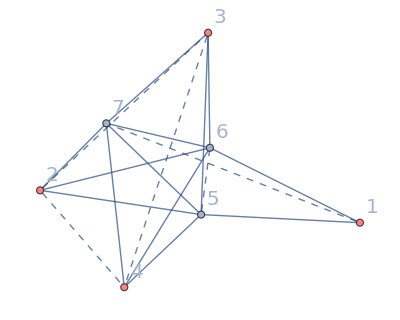

```mathematica
drawGraph[{Times@@(basis3L[[-1]]),{1,2,3,4}(*four external points*)}](*the last most complicated integral*)
```

```mathematica
result3L[[-1]](*its result in svmpls*)
```

(2 z zz (-2+z+zz+z zz) ⅈ[z,0,0,0,1,0,0,0])/((z-zz) (-1+z+zz) (-1+z zz))+(2 z (8-4 z-8 zz-2 z zz+5 z^2 zz+2 zz^2+6 z zz^2-7 z^2 zz^2-zz^3-z zz^3+2 z^2 zz^3) ⅈ[z,0,0,0,1,0,1,0])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))+(2 z zz (8-7 z-2 z^2-9 zz-8 z zz+9 z^2 zz+2 zz^2+7 z zz^2) ⅈ[z,0,0,0,1,1,0,0])/((z-zz)^2 (-1+z+zz) (-1+z zz))-(4 z (-1+zz) (-2+4 z+3 zz-2 z zz-5 z^2 zz-zz^2-3 z zz^2+4 z^2 zz^2) ⅈ[z,0,0,0,1,1,1,0])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))-(2 z zz (-2+z+zz+z zz) ⅈ[z,0,0,1,0,0,0,0])/((z-zz) (-1+z+zz) (-1+z zz))-(2 z zz (1-2 z-2 zz+z zz) ⅈ[z,0,0,1,0,0,1,0])/((z-zz) (-1+z+zz) (-1+z zz))-(2 z (8-4 z-8 zz-2 z zz+5 z^2 zz+2 zz^2+6 z zz^2-7 z^2 zz^2-zz^3-z zz^3+2 z^2 zz^3) ⅈ[z,0,0,1,0,1,0,0])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))-(4 z (-1+zz) (2+zz-2 z zz+z^2 zz+zz^2-z zz^2) ⅈ[z,0,0,1,0,1,1,0])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))-(16 z zz ⅈ[z,0,0,1,1,0,0,0])/(z-zz)^2+(2 z (4-4 z-6 zz-6 z zz+5 z^2 zz+2 z^3 zz-2 zz^2+18 z zz^2+3 z^2 zz^2-5 z^3 zz^2+7 zz^3-7 z zz^3-12 z^2 zz^3+3 z^3 zz^3-2 zz^4-3 z zz^4+5 z^2 zz^4) ⅈ[z,0,0,1,1,0,1,0])/((z-zz)^2 (-1+z+zz) (-1+z zz) (-z-zz+z zz))+(2 z (-4+12 z-8 z^2+14 zz-26 z zz+3 z^2 zz+6 z^3 zz-14 zz^2+6 z zz^2+21 z^2 zz^2-11 z^3 zz^2+zz^3+15 z zz^3-20 z^2 zz^3+5 z^3 zz^3+2 zz^4-5 z zz^4+3 z^2 zz^4) ⅈ[z,0,0,1,1,1,0,0])/((z-zz)^2 (-1+z+zz) (-1+z zz) (-z-zz+z zz))-(2 z (-8+12 z-4 z^2+16 zz-10 z zz-6 z^2 zz+3 z^3 zz-10 zz^2-6 z zz^2+15 z^2 zz^2-4 z^3 zz^2+2 zz^3+9 z zz^3-10 z^2 zz^3+z^3 zz^3+zz^4-4 z zz^4+3 z^2 zz^4) ⅈ[z,0,1,0,0,0,1,0])/((z-zz)^2 (-1+z+zz) (-1+z zz) (-z-zz+z zz))-(8 (2-z-zz+z zz) ⅈ[z,0,1,0,0,1,0,0])/(z-zz)^2+(2 (-1+z) (12 z-13 z^2+8 zz-38 z zz+10 z^2 zz+11 z^3 zz-11 zz^2+21 z zz^2+27 z^2 zz^2-20 z^3 zz^2+3 zz^3+6 z zz^3-31 z^2 zz^3+9 z^3 zz^3-5 z zz^4+7 z^2 zz^4) ⅈ[z,0,1,0,0,1,1,0])/((z-zz)^2 (-1+z+zz) (-1+z zz) (-z-zz+z zz))+(2 z (8-4 z-8 zz-2 z zz+5 z^2 zz+2 zz^2+6 z zz^2-7 z^2 zz^2-zz^3-z zz^3+2 z^2 zz^3) ⅈ[z,0,1,0,1,0,0,0])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))+(4 z (-1+zz) (2+zz-2 z zz+z^2 zz+zz^2-z zz^2) ⅈ[z,0,1,0,1,0,1,0])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))-(4 z (2-zz+z^2 zz+2 zz^2-z zz^2-3 z^2 zz^2-zz^3-z zz^3+2 z^2 zz^3) ⅈ[z,0,1,0,1,1,0,0])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))+(2 (-1+zz) (-3 z-z^2-zz-z zz+z^2 zz-3 z^3 zz-3 z zz^2+z^2 zz^2+2 z^3 zz^2) ⅈ[z,0,1,0,1,1,1,0])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))+(2 (8-12 z+4 z^2-12 zz+4 z zz+7 z^2 zz-2 z^3 zz+4 zz^2+9 z zz^2-12 z^2 zz^2+3 z^3 zz^2-6 z zz^3+5 z^2 zz^3) ⅈ[z,0,1,1,0,0,0,0])/((z-zz)^2 (-1+z+zz) (-1+z zz))-(2 (4 z-5 z^2+8 zz-14 z zz+5 z^2 zz+3 z^3 zz-3 zz^2-z zz^2+10 z^2 zz^2-7 z^3 zz^2+5 z zz^3-9 z^2 zz^3+4 z^3 zz^3) ⅈ[z,0,1,1,0,0,1,0])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))-(4 z (-1+zz) (2+zz-2 z zz+z^2 zz+zz^2-z zz^2) ⅈ[z,0,1,1,0,1,0,0])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))+(2 (-1+z) (-1+zz) (-2+z+zz+z zz) ⅈ[z,0,1,1,0,1,1,0])/((z-zz) (-1+z+zz) (-z-zz+z zz))-(2 z (-4+12 z-8 z^2+14 zz-22 z zz-z^2 zz+6 z^3 zz-10 zz^2-6 z zz^2+21 z^2 zz^2-7 z^3 zz^2-3 zz^3+15 z zz^3-8 z^2 zz^3+z^3 zz^3+2 zz^4-z zz^4-z^2 zz^4) ⅈ[z,0,1,1,1,0,0,0])/((z-zz)^2 (-1+z+zz) (-1+z zz) (-z-zz+z zz))-(2 (-1+zz) (z+z^2-2 z^3+3 zz-5 z zz-2 z^4 zz-2 zz^2-5 z^3 zz^2+3 z^4 zz^2-2 z zz^3+z^2 zz^3+z^3 zz^3) ⅈ[z,0,1,1,1,0,1,0])/((z-zz)^2 (-1+z+zz) (-1+z zz) (-z-zz+z zz))-(8 (2-z-zz+z zz) ⅈ[z,0,zz,0,0,1,1,0])/(z-zz)^2+(8 (2-z-zz+z zz) ⅈ[z,0,zz,0,1,1,0,0])/(z-zz)^2+(8 (2-z-zz+z zz) ⅈ[z,0,zz,1,0,0,1,0])/(z-zz)^2-(8 (2-z-zz+z zz) ⅈ[z,0,zz,1,1,0,0,0])/(z-zz)^2-(2 zz (-8+16 z-10 z^2+2 z^3+z^4+12 zz-10 z zz-6 z^2 zz+9 z^3 zz-4 z^4 zz-4 zz^2-6 z zz^2+15 z^2 zz^2-10 z^3 zz^2+3 z^4 zz^2+3 z zz^3-4 z^2 zz^3+z^3 zz^3) ⅈ[z,1,0,0,0,1,0,0])/((z-zz)^2 (-1+z+zz) (-1+z zz) (-z-zz+z zz))-(2 (-1+z) (-4 z+3 z^2-8 zz+18 z zz+2 z^2 zz-5 z^3 zz+13 zz^2-3 z zz^2-21 z^2 zz^2+4 z^3 zz^2-5 zz^3-10 z zz^3+9 z^2 zz^3+z^3 zz^3+3 z zz^4-z^2 zz^4) ⅈ[z,1,0,0,0,1,1,0])/((z-zz)^2 (-1+z+zz) (-1+z zz) (-z-zz+z zz))+(2 z zz (1-2 z-2 zz+z zz) ⅈ[z,1,0,0,1,0,0,0])/((z-zz) (-1+z+zz) (-1+z zz))+(4 (-1+z) zz (-2-z-z^2+2 z zz+z^2 zz-z zz^2) ⅈ[z,1,0,0,1,0,1,0])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))-(2 (4 z+z^2-2 z zz-z^2 zz+z^3 zz-zz^2+5 z zz^2-2 z^2 zz^2-5 z^3 zz^2-z zz^3-3 z^2 zz^3+4 z^3 zz^3) ⅈ[z,1,0,0,1,1,0,0])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))+(2 (6 z-7 z^2+z^3+2 zz-12 z zz+10 z^2 zz-4 z^3 zz-zz^2+6 z zz^2-12 z^2 zz^2+3 z^3 zz^2-zz^3-4 z zz^3+5 z^2 zz^3) ⅈ[z,1,0,0,1,1,1,0])/((z-zz)^2 (-1+z+zz) (-z-zz+z zz))+(2 zz (8-8 z+2 z^2-z^3-4 zz-2 z zz+6 z^2 zz-z^3 zz+5 z zz^2-7 z^2 zz^2+2 z^3 zz^2) ⅈ[z,1,0,1,0,0,0,0])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))-(4 (-1+z) (-2 z-4 zz+3 z zz+z^2 zz+2 zz^2+2 z zz^2-3 z^2 zz^2-3 z zz^3+2 z^2 zz^3) ⅈ[z,1,0,1,0,0,1,0])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))-(4 (-1+z) zz (-2-z-z^2+2 z zz+z^2 zz-z zz^2) ⅈ[z,1,0,1,0,1,0,0])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))+(2 (-1+z) (-z-3 zz-z zz-3 z^2 zz-zz^2+z zz^2+z^2 zz^2-3 z zz^3+2 z^2 zz^3) ⅈ[z,1,0,1,0,1,1,0])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))+(2 z (-4+4 z+6 zz-6 z zz+7 z^2 zz-2 z^3 zz-10 zz^2+18 z zz^2-3 z^2 zz^2-7 z^3 zz^2+5 zz^3+7 z zz^3-24 z^2 zz^3+9 z^3 zz^3+2 zz^4-9 z zz^4+7 z^2 zz^4) ⅈ[z,1,0,1,1,0,0,0])/((z-zz)^2 (-1+z+zz) (-1+z zz) (-z-zz+z zz))-(8 (1+z zz) ⅈ[z,1,0,1,1,0,1,0])/(z-zz)^2-(2 (-1+z) (3 z-2 z^2+zz-5 z zz-2 z^3 zz+zz^2+z^3 zz^2-2 zz^3-5 z^2 zz^3+z^3 zz^3-2 z zz^4+3 z^2 zz^4) ⅈ[z,1,0,1,1,1,0,0])/((z-zz)^2 (-1+z+zz) (-1+z zz) (-z-zz+z zz))+(2 (-1+z) (-z^2-4 zz+2 z zz+6 z^2 zz-z^3 zz+5 zz^2+9 z zz^2-9 z^2 zz^2-4 z^3 zz^2-zz^3-6 z zz^3-7 z^2 zz^3+5 z^3 zz^3-z zz^4+3 z^2 zz^4) ⅈ[z,1,1,0,0,0,1,0])/((z-zz)^2 (-1+z+zz) (-1+z zz) (-z-zz+z zz))+(2 (-1+z) (z^2+4 zz-10 z zz+2 z^2 zz+z^3 zz-13 zz^2+15 z zz^2+9 z^2 zz^2-4 z^3 zz^2+9 zz^3+6 z zz^3-17 z^2 zz^3+3 z^3 zz^3-7 z zz^4+5 z^2 zz^4) ⅈ[z,1,1,0,0,1,0,0])/((z-zz)^2 (-1+z+zz) (-1+z zz) (-z-zz+z zz))-(16 (-1+z) (-1+zz) ⅈ[z,1,1,0,0,1,1,0])/(z-zz)^2+(4 (-1+z) zz (-2-z-z^2+2 z zz+z^2 zz-z zz^2) ⅈ[z,1,1,0,1,0,0,0])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))-(2 (-1+z) (-z-3 zz-z zz-3 z^2 zz-zz^2+z zz^2+z^2 zz^2-3 z zz^3+2 z^2 zz^3) ⅈ[z,1,1,0,1,0,1,0])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))-(2 (-1+z) (-1+zz) (-2+z+zz+z zz) ⅈ[z,1,1,0,1,1,0,0])/((z-zz) (-1+z+zz) (-z-zz+z zz))-(2 (-1+z) (-1+zz) (1-2 z-2 zz+z zz) ⅈ[z,1,1,0,1,1,1,0])/((z-zz) (-1+z+zz) (-z-zz+z zz))-(4 (-1+z) zz (-2+3 z-z^2+4 zz-2 z zz-3 z^2 zz-5 z zz^2+4 z^2 zz^2) ⅈ[z,1,1,1,0,0,0,0])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))+(2 (-1+z) (-1+zz) (6 z-7 z^2+10 zz-24 z zz+9 z^2 zz-9 zz^2+7 z zz^2) ⅈ[z,1,1,1,0,0,1,0])/((z-zz)^2 (-1+z+zz) (-z-zz+z zz))+(2 (-1+z) (-z-3 zz-z zz-3 z^2 zz-zz^2+z zz^2+z^2 zz^2-3 z zz^3+2 z^2 zz^3) ⅈ[z,1,1,1,0,1,0,0])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))+(2 (-1+z) (-1+zz) (1-2 z-2 zz+z zz) ⅈ[z,1,1,1,0,1,1,0])/((z-zz) (-1+z+zz) (-z-zz+z zz))-(8 (1+z zz) ⅈ[z,1,zz,0,0,1,1,0])/(z-zz)^2+(8 (1+z zz) ⅈ[z,1,zz,0,1,1,0,0])/(z-zz)^2+(8 (1+z zz) ⅈ[z,1,zz,1,0,0,1,0])/(z-zz)^2-(8 (1+z zz) ⅈ[z,1,zz,1,1,0,0,0])/(z-zz)^2+(8 (-2+z+zz+z zz) ⅈ[z,zz,0,0,0,1,1,0])/(z-zz)^2-(8 (2-z-zz+z zz) ⅈ[z,zz,0,0,1,0,1,0])/(z-zz)^2+(8 (2-z-zz+z zz) ⅈ[z,zz,0,0,1,1,0,0])/(z-zz)^2+(8 (1-2 z-2 zz+z zz) ⅈ[z,zz,0,0,1,1,1,0])/(z-zz)^2+(8 (2-z-zz+z zz) ⅈ[z,zz,0,1,0,0,1,0])/(z-zz)^2+(8 (2-z-zz+z zz) ⅈ[z,zz,0,1,0,1,0,0])/(z-zz)^2-(8 (1+z zz) ⅈ[z,zz,0,1,0,1,1,0])/(z-zz)^2-(8 (2-z-zz+3 z zz) ⅈ[z,zz,0,1,1,0,0,0])/(z-zz)^2+(8 (1+z zz) ⅈ[z,zz,0,1,1,0,1,0])/(z-zz)^2-(8 (1-2 z-2 zz+z zz) ⅈ[z,zz,0,1,1,1,0,0])/(z-zz)^2-(8 (-2+z+zz+z zz) ⅈ[z,zz,1,0,0,0,1,0])/(z-zz)^2+(8 (2-z-zz+z zz) ⅈ[z,zz,1,0,0,1,0,0])/(z-zz)^2-(8 (3-2 z-2 zz+3 z zz) ⅈ[z,zz,1,0,0,1,1,0])/(z-zz)^2-(8 (2-z-zz+z zz) ⅈ[z,zz,1,0,1,0,0,0])/(z-zz)^2+(8 (1+z zz) ⅈ[z,zz,1,0,1,0,1,0])/(z-zz)^2+(8 (1+z zz) ⅈ[z,zz,1,0,1,1,0,0])/(z-zz)^2+(8 (-2+z+zz+z zz) ⅈ[z,zz,1,1,0,0,0,0])/(z-zz)^2+(8 (1+z zz) ⅈ[z,zz,1,1,0,0,1,0])/(z-zz)^2-(8 (1+z zz) ⅈ[z,zz,1,1,0,1,0,0])/(z-zz)^2+(8 (1-2 z-2 zz+z zz) ⅈ[z,zz,1,1,1,0,0,0])/(z-zz)^2+(16 (2-z-zz+2 z zz) ⅈ[z,zz,zz,0,0,1,1,0])/(z-zz)^2-(16 (2-z-zz+2 z zz) ⅈ[z,zz,zz,0,1,1,0,0])/(z-zz)^2-(16 (2-z-zz+2 z zz) ⅈ[z,zz,zz,1,0,0,1,0])/(z-zz)^2+(16 (2-z-zz+2 z zz) ⅈ[z,zz,zz,1,1,0,0,0])/(z-zz)^2-(12 ⅈ[z,0,1,0] f[3])/(z-zz)+(12 ⅈ[z,1,0,0] f[3])/(z-zz)-(16 z zz (-2+z+zz+z zz) ⅈ[z,0,0,1,0] f[3])/((z-zz) (-1+z+zz) (-1+z zz))-(16 (4-6 z+2 z^2-6 zz+2 z zz+5 z^2 zz-4 z^3 zz+2 zz^2+3 z zz^2-6 z^2 zz^2+3 z^3 zz^2+z^2 zz^3) ⅈ[z,0,1,1,0] f[3])/((z-zz)^2 (-1+z+zz) (-1+z zz))-(4 (6 z-3 z^2+10 zz-16 z zz+z^2 zz+7 z^3 zz-5 zz^2-z zz^2+12 z^2 zz^2-11 z^3 zz^2+z zz^3-5 z^2 zz^3+4 z^3 zz^3) ⅈ[z,1,0,1,0] f[3])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))+(4 (-1+z) (-3 z-5 zz+15 z zz+11 z^2 zz+13 zz^2+z zz^2-15 z^2 zz^2-5 z zz^3+4 z^2 zz^3) ⅈ[z,1,1,1,0] f[3])/((z-zz)^2 (-1+z zz) (-z-zz+z zz))+(32 (2-z-zz+2 z zz) ⅈ[z,zz,1,1,0] f[3])/(z-zz)^2

#### Magic identities & symmetries

```mathematica
sysmagic3L=GenMagicId[basis3L,I3](*magic identities*)
```

{I3[2][{2,1,3,4}]-I3[3][{1,2,3,4}],I3[2][{3,1,2,4}]-I3[3][{1,3,2,4}],I3[2][{1,2,3,4}]-I3[3][{2,1,3,4}],I3[2][{3,2,1,4}]-I3[3][{2,3,1,4}],I3[2][{1,3,2,4}]-I3[3][{3,1,2,4}],I3[2][{2,3,1,4}]-I3[3][{3,2,1,4}],-I3[9][{1,2,3,4}]+I3[11][{2,3,1,4}],-I3[9][{1,3,2,4}]+I3[11][{3,2,1,4}],-I3[9][{2,1,3,4}]+I3[11][{1,3,2,4}],-I3[9][{2,3,1,4}]+I3[11][{3,1,2,4}],-I3[9][{3,1,2,4}]+I3[11][{1,2,3,4}],-I3[9][{3,2,1,4}]+I3[11][{2,1,3,4}],I3[9][{3,2,1,4}]-I3[11][{1,2,3,4}],I3[9][{2,3,1,4}]-I3[11][{1,3,2,4}],I3[9][{3,1,2,4}]-I3[11][{2,1,3,4}],I3[9][{1,3,2,4}]-I3[11][{2,3,1,4}],I3[9][{2,1,3,4}]-I3[11][{3,1,2,4}],I3[9][{1,2,3,4}]-I3[11][{3,2,1,4}]}

```mathematica
syssym3L=GenSymId[basis3L,I3](*symmetries of integrals*)
```

No symmetry identity found for basis integral 3

{-I3[1][{2,3,1,4}]+I3[1][{3,2,1,4}],-I3[1][{1,3,2,4}]+I3[1][{3,1,2,4}],-I3[1][{1,2,3,4}]+I3[1][{2,1,3,4}],-I3[4][{3,1,2,4}]+I3[4][{3,2,1,4}],-I3[4][{2,1,3,4}]+I3[4][{2,3,1,4}],-I3[4][{1,2,3,4}]+I3[4][{1,3,2,4}],-I3[5][{2,3,1,4}]+I3[5][{3,2,1,4}],-I3[5][{1,3,2,4}]+I3[5][{3,1,2,4}],-I3[5][{1,2,3,4}]+I3[5][{2,1,3,4}],-z zz I3[6][{2,3,1,4}]+I3[6][{3,2,1,4}],-(z zz I3[6][{1,3,2,4}])/((-1+z) (-1+zz))+I3[6][{3,1,2,4}],-(I3[6][{1,2,3,4}])/((-1+z) (-1+zz))+I3[6][{2,1,3,4}],-I3[7][{1,2,3,4}]+I3[7][{3,2,1,4}],-I3[7][{1,2,3,4}]+I3[7][{3,1,2,4}],-I3[7][{1,2,3,4}]+I3[7][{2,3,1,4}],-I3[7][{1,2,3,4}]+I3[7][{2,1,3,4}],-I3[7][{1,2,3,4}]+I3[7][{1,3,2,4}],-(z zz I3[8][{1,2,3,4}])/((-1+z) (-1+zz))+I3[8][{3,2,1,4}],-z zz I3[8][{1,2,3,4}]+I3[8][{3,1,2,4}],-(z zz I3[8][{1,2,3,4}])/((-1+z) (-1+zz))+I3[8][{2,3,1,4}],-I3[8][{1,2,3,4}]+I3[8][{2,1,3,4}],-z zz I3[8][{1,2,3,4}]+I3[8][{1,3,2,4}],-I3[9][{3,1,2,4}]+I3[9][{3,2,1,4}],-I3[9][{2,1,3,4}]+I3[9][{2,3,1,4}],-I3[9][{1,2,3,4}]+I3[9][{1,3,2,4}],-I3[10][{2,3,1,4}]+I3[10][{3,2,1,4}],-I3[10][{1,3,2,4}]+I3[10][{3,1,2,4}],-I3[10][{1,2,3,4}]+I3[10][{2,1,3,4}],-I3[11][{2,3,1,4}]+I3[11][{3,2,1,4}],-I3[11][{1,3,2,4}]+I3[11][{3,1,2,4}],-I3[11][{1,2,3,4}]+I3[11][{2,1,3,4}],-z zz I3[12][{2,3,1,4}]+I3[12][{3,2,1,4}],-(z zz I3[12][{1,3,2,4}])/((-1+z) (-1+zz))+I3[12][{3,1,2,4}],-(I3[12][{1,2,3,4}])/((-1+z) (-1+zz))+I3[12][{2,1,3,4}],-I3[13][{2,3,1,4}]+I3[13][{3,2,1,4}],-I3[13][{1,3,2,4}]+I3[13][{3,1,2,4}],-I3[13][{1,2,3,4}]+I3[13][{2,1,3,4}],-I3[14][{3,1,2,4}]+I3[14][{3,2,1,4}],-I3[14][{2,1,3,4}]+I3[14][{2,3,1,4}],-I3[14][{1,2,3,4}]+I3[14][{1,3,2,4}],-I3[15][{1,2,3,4}]+I3[15][{3,2,1,4}],-I3[15][{1,2,3,4}]+I3[15][{3,1,2,4}],-I3[15][{1,2,3,4}]+I3[15][{2,3,1,4}],-I3[15][{1,2,3,4}]+I3[15][{2,1,3,4}],-I3[15][{1,2,3,4}]+I3[15][{1,3,2,4}]}

```mathematica
sol3L=Solve[Join[Thread@Equal[Join[sysmagic3L,syssym3L],0],{z!=0,zz!=0,I3[8][{1,2,3,4}]!=0,I3[6][{1,3,2,4}]!=0}]][[1]]
```

{I3[1][{2,1,3,4}]→I3[1][{1,2,3,4}],I3[1][{3,1,2,4}]→I3[1][{1,3,2,4}],I3[1][{3,2,1,4}]→I3[1][{2,3,1,4}],I3[3][{1,2,3,4}]→I3[2][{2,1,3,4}],I3[3][{1,3,2,4}]→I3[2][{3,1,2,4}],I3[3][{2,1,3,4}]→I3[2][{1,2,3,4}],I3[3][{2,3,1,4}]→I3[2][{3,2,1,4}],I3[3][{3,1,2,4}]→I3[2][{1,3,2,4}],I3[3][{3,2,1,4}]→I3[2][{2,3,1,4}],I3[4][{1,3,2,4}]→I3[4][{1,2,3,4}],I3[4][{2,3,1,4}]→I3[4][{2,1,3,4}],I3[4][{3,2,1,4}]→I3[4][{3,1,2,4}],I3[5][{2,1,3,4}]→I3[5][{1,2,3,4}],I3[5][{3,1,2,4}]→I3[5][{1,3,2,4}],I3[5][{3,2,1,4}]→I3[5][{2,3,1,4}],I3[6][{1,2,3,4}]→(-1+z) (-1+zz) I3[6][{2,1,3,4}],I3[6][{1,3,2,4}]→((-1+z) (-1+zz) I3[6][{3,1,2,4}])/(z zz),I3[6][{3,2,1,4}]→z zz I3[6][{2,3,1,4}],I3[7][{1,3,2,4}]→I3[7][{1,2,3,4}],I3[7][{2,1,3,4}]→I3[7][{1,2,3,4}],I3[7][{2,3,1,4}]→I3[7][{1,2,3,4}],I3[7][{3,1,2,4}]→I3[7][{1,2,3,4}],I3[7][{3,2,1,4}]→I3[7][{1,2,3,4}],I3[8][{1,3,2,4}]→z zz I3[8][{1,2,3,4}],I3[8][{2,1,3,4}]→I3[8][{1,2,3,4}],I3[8][{2,3,1,4}]→(z zz I3[8][{1,2,3,4}])/((-1+z) (-1+zz)),I3[8][{3,1,2,4}]→z zz I3[8][{1,2,3,4}],I3[8][{3,2,1,4}]→(z zz I3[8][{1,2,3,4}])/((-1+z) (-1+zz)),I3[9][{1,2,3,4}]→I3[11][{2,3,1,4}],I3[9][{1,3,2,4}]→I3[11][{2,3,1,4}],I3[9][{2,1,3,4}]→I3[11][{1,3,2,4}],I3[9][{2,3,1,4}]→I3[11][{1,3,2,4}],I3[9][{3,1,2,4}]→I3[11][{1,2,3,4}],I3[9][{3,2,1,4}]→I3[11][{1,2,3,4}],I3[10][{2,1,3,4}]→I3[10][{1,2,3,4}],I3[10][{3,1,2,4}]→I3[10][{1,3,2,4}],I3[10][{3,2,1,4}]→I3[10][{2,3,1,4}],I3[11][{2,1,3,4}]→I3[11][{1,2,3,4}],I3[11][{3,1,2,4}]→I3[11][{1,3,2,4}],I3[11][{3,2,1,4}]→I3[11][{2,3,1,4}],I3[12][{1,2,3,4}]→(-1+z) (-1+zz) I3[12][{2,1,3,4}],I3[12][{1,3,2,4}]→((-1+z) (-1+zz) I3[12][{3,1,2,4}])/(z zz),I3[12][{3,2,1,4}]→z zz I3[12][{2,3,1,4}],I3[13][{2,1,3,4}]→I3[13][{1,2,3,4}],I3[13][{3,1,2,4}]→I3[13][{1,3,2,4}],I3[13][{3,2,1,4}]→I3[13][{2,3,1,4}],I3[14][{1,3,2,4}]→I3[14][{1,2,3,4}],I3[14][{2,3,1,4}]→I3[14][{2,1,3,4}],I3[14][{3,2,1,4}]→I3[14][{3,1,2,4}],I3[15][{1,3,2,4}]→I3[15][{1,2,3,4}],I3[15][{2,1,3,4}]→I3[15][{1,2,3,4}],I3[15][{2,3,1,4}]→I3[15][{1,2,3,4}],I3[15][{3,1,2,4}]→I3[15][{1,2,3,4}],I3[15][{3,2,1,4}]→I3[15][{1,2,3,4}]}

#### Gram identity

Now we consider the Gram identity for three loop, and we can see that it can be used to solve the last unknown integral above

```mathematica
den=Times@@((CompleteGraph[7]//EdgeList)/.{UndirectedEdge->x})
```

x[1,2] x[1,3] x[1,4] x[1,5] x[1,6] x[1,7] x[2,3] x[2,4] x[2,5] x[2,6] x[2,7] x[3,4] x[3,5] x[3,6] x[3,7] x[4,5] x[4,6] x[4,7] x[5,6] x[5,7] x[6,7]

```mathematica
gram=Det[Table[x[i,j],{i,1,7},{j,1,7}]]/den//Expand;
```

```mathematica
sysGram3L=CanonicalExp[gram*x[1,3]^3x[2,4]^3,basis3L,I3];
```

```mathematica
(*the solution we get*)
```

```mathematica
solgram3L=Solve[(sysGram3L/.sol3L)==0,I3[15][{1,2,3,4}]][[1]]//Collect[#,I3[_][_],Factor]&
```

{I3[15][{1,2,3,4}]→I3[1][{1,2,3,4}]+I3[1][{1,3,2,4}]+I3[1][{2,3,1,4}]-3 I3[2][{1,2,3,4}]-3 I3[2][{1,3,2,4}]-3 I3[2][{2,1,3,4}]-3 I3[2][{2,3,1,4}]-3 I3[2][{3,1,2,4}]-3 I3[2][{3,2,1,4}]+2 I3[4][{1,2,3,4}]+2 I3[4][{2,1,3,4}]+2 I3[4][{3,1,2,4}]+((-2+z+zz+z zz) I3[5][{1,2,3,4}])/(z zz)+(1+z+zz-2 z zz) I3[5][{1,3,2,4}]+((1-2 z-2 zz+z zz) I3[5][{2,3,1,4}])/((-1+z) (-1+zz))+(-2+z+zz) I3[6][{2,1,3,4}]+(-z-zz) I3[6][{2,3,1,4}]-((-z-zz+2 z zz) I3[6][{3,1,2,4}])/(z zz)+2 I3[7][{1,2,3,4}]-((z-zz)^2 I3[8][{1,2,3,4}])/(12 (-1+z) (-1+zz))+2 I3[10][{1,2,3,4}]+2 I3[10][{1,3,2,4}]+2 I3[10][{2,3,1,4}]+3 I3[11][{1,2,3,4}]+3 I3[11][{1,3,2,4}]+3 I3[11][{2,3,1,4}]+1/2 (2-z-zz) I3[12][{2,1,3,4}]+1/2 (z+zz) I3[12][{2,3,1,4}]+((-z-zz+2 z zz) I3[12][{3,1,2,4}])/(2 z zz)-I3[13][{1,2,3,4}]-I3[13][{1,3,2,4}]-I3[13][{2,3,1,4}]-I3[14][{1,2,3,4}]-I3[14][{2,1,3,4}]-I3[14][{3,1,2,4}]}

```mathematica
solgram3L//TransformArg[#,"head"->I3]&(*transform the arguments*)
```

{I3[15][z,zz]→I3[1][1-1/z,1-1/zz]+I3[1][1/z,1/zz]+I3[1][z,zz]-3 I3[2][1-1/z,1-1/zz]-3 I3[2][1/(1-z),1/(1-zz)]-3 I3[2][1-z,1-zz]-3 I3[2][1/z,1/zz]-3 I3[2][z,zz]-3 I3[2][z/(-1+z),zz/(-1+zz)]+2 I3[4][1/(1-z),1/(1-zz)]+2 I3[4][z,zz]+2 I3[4][z/(-1+z),zz/(-1+zz)]+((1-2 z-2 zz+z zz) I3[5][1-1/z,1-1/zz])/((-1+z) (-1+zz))+(1+z+zz-2 z zz) I3[5][1/z,1/zz]+((-2+z+zz+z zz) I3[5][z,zz])/(z zz)+(-z-zz) I3[6][1-1/z,1-1/zz]-((-z-zz+2 z zz) I3[6][1/(1-z),1/(1-zz)])/(z zz)+(-2+z+zz) I3[6][z/(-1+z),zz/(-1+zz)]+2 I3[7][z,zz]-((z-zz)^2 I3[8][z,zz])/(12 (-1+z) (-1+zz))+2 I3[10][1-1/z,1-1/zz]+2 I3[10][1/z,1/zz]+2 I3[10][z,zz]+3 I3[11][1-1/z,1-1/zz]+3 I3[11][1/z,1/zz]+3 I3[11][z,zz]+1/2 (z+zz) I3[12][1-1/z,1-1/zz]+((-z-zz+2 z zz) I3[12][1/(1-z),1/(1-zz)])/(2 z zz)+1/2 (2-z-zz) I3[12][z/(-1+z),zz/(-1+zz)]-I3[13][1-1/z,1-1/zz]-I3[13][1/z,1/zz]-I3[13][z,zz]-I3[14][1/(1-z),1/(1-zz)]-I3[14][z,zz]-I3[14][z/(-1+z),zz/(-1+zz)]}

### four loop

#### integrand basis and partial results

```mathematica
basis4L=Import["/Users/windfolgen/Documents/AntiGravity/correlator/nonplanar/4Loop_int_basis.m"];
```

For the package HyperlogProcedures, please see https://www.physik.uni-hamburg.de/th2/ag-moch/personen/schnetz-oliver.html

```mathematica
Length[basis4L]
```

412

```mathematica
result4Lbyhp=Import["./4Loop_integral_results_by_hyperlog.m"];
```

```mathematica
result4Lbyhp[[173]](*integrals can not be calculated by HyperlogProcedures show FAIL*)
```

FAIL

```mathematica
knownbyhl=Position[result4Lbyhp,_?(#=!=FAIL&),1]//Flatten//DeleteCases[#,0]&
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,27,28,30,31,32,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,60,61,64,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,91,92,94,95,96,99,100,101,102,103,104,106,109,114,115,119,121,122,124,125,126,128,133,136,138,139,140,141,149,150,151,152,153,157,159,160,161,162,164,165,172,174,175,179,185,186,187,188,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,220,225,235,236,242,251,255,256,268,271,276,277,278,281,287,309,314,317,348,370,372}

```mathematica
(*relation between an integrand given and the basis we defined*)
```

```mathematica
CanonicalExp[(x[1,2]^2 x[3,4]^2)/(x[1,5] x[1,6] x[1,7] x[2,5] x[2,6] x[2,8] x[3,5] x[3,7] x[3,8] x[4,6] x[4,7] x[4,8] x[5,6] x[7,8]),basis4L,I4]
```

(z^2 zz^2 I4[49][{3,1,2,4}])/((-1+z) (-1+zz))

#### Magic identities & symmetries

```mathematica
sysmagic4L=GenMagicId[basis4L,I4](*magic identities*)
```

{I4[11][{3,1,2,4}]-I4[13][{1,2,3,4}],I4[11][{2,1,3,4}]-I4[13][{1,3,2,4}],I4[11][{3,2,1,4}]-I4[13][{2,1,3,4}],I4[11][{1,2,3,4}]-I4[13][{2,3,1,4}],I4[11][{2,3,1,4}]-I4[13][{3,1,2,4}],I4[11][{1,3,2,4}]-I4[13][{3,2,1,4}],I4[15][{1,3,2,4}]-I4[18][{1,2,3,4}],I4[15][{1,2,3,4}]-I4[18][{1,3,2,4}],I4[15][{2,3,1,4}]-I4[18][{2,1,3,4}],I4[15][{2,1,3,4}]-I4[18][{2,3,1,4}],I4[15][{3,2,1,4}]-I4[18][{3,1,2,4}],I4[15][{3,1,2,4}]-I4[18][{3,2,1,4}],-I4[19][{1,2,3,4}]+I4[103][{2,3,1,4}],-I4[19][{1,3,2,4}]+I4[103][{3,2,1,4}],-I4[19][{2,1,3,4}]+I4[103][{1,3,2,4}],-I4[19][{2,3,1,4}]+I4[103][{3,1,2,4}],-I4[19][{3,1,2,4}]+I4[103][{1,2,3,4}],-I4[19][{3,2,1,4}]+I4[103][{2,1,3,4}],-I4[21][{1,2,3,4}]+I4[72][{2,1,3,4}],-I4[21][{1,3,2,4}]+I4[72][{3,1,2,4}],-I4[21][{2,1,3,4}]+I4[72][{1,2,3,4}],-I4[21][{2,3,1,4}]+I4[72][{3,2,1,4}],-I4[21][{3,1,2,4}]+I4[72][{1,3,2,4}],-I4[21][{3,2,1,4}]+I4[72][{2,3,1,4}],-I4[21][{1,2,3,4}]+I4[72][{1,2,3,4}],-I4[21][{1,3,2,4}]+I4[72][{1,3,2,4}],-I4[21][{2,1,3,4}]+I4[72][{2,1,3,4}],-I4[21][{2,3,1,4}]+I4[72][{2,3,1,4}],-I4[21][{3,1,2,4}]+I4[72][{3,1,2,4}],-I4[21][{3,2,1,4}]+I4[72][{3,2,1,4}],-I4[27][{1,2,3,4}]+I4[89][{1,2,3,4}],-I4[27][{1,3,2,4}]+I4[89][{1,3,2,4}],-I4[27][{2,1,3,4}]+I4[89][{2,1,3,4}],-I4[27][{2,3,1,4}]+I4[89][{2,3,1,4}],-I4[27][{3,1,2,4}]+I4[89][{3,1,2,4}],-I4[27][{3,2,1,4}]+I4[89][{3,2,1,4}],(-1+z) (-1+zz) I4[24][{1,2,3,4}]-z zz I4[28][{1,2,3,4}],(-1+z) (-1+zz) I4[24][{1,3,2,4}]-I4[28][{1,3,2,4}],I4[24][{2,1,3,4}]-z zz I4[28][{2,1,3,4}],I4[24][{2,3,1,4}]-(-1+z) (-1+zz) I4[28][{2,3,1,4}],z zz I4[24][{3,1,2,4}]-I4[28][{3,1,2,4}],z zz I4[24][{3,2,1,4}]-(-1+z) (-1+zz) I4[28][{3,2,1,4}],-I4[35][{1,2,3,4}]+I4[35][{1,3,2,4}],-I4[35][{2,1,3,4}]+I4[35][{2,3,1,4}],-I4[35][{3,1,2,4}]+I4[35][{3,2,1,4}],-z zz I4[37][{1,2,3,4}]+(-1+z) (-1+zz) I4[122][{1,2,3,4}],-I4[37][{1,3,2,4}]+(-1+z) (-1+zz) I4[122][{1,3,2,4}],-z zz I4[37][{2,1,3,4}]+I4[122][{2,1,3,4}],-((-1+z) (-1+zz) I4[37][{2,3,1,4}])+I4[122][{2,3,1,4}],-I4[37][{3,1,2,4}]+z zz I4[122][{3,1,2,4}],-((-1+z) (-1+zz) I4[37][{3,2,1,4}])+z zz I4[122][{3,2,1,4}],I4[23][{2,1,3,4}]-I4[44][{1,2,3,4}],I4[23][{3,1,2,4}]-I4[44][{1,3,2,4}],I4[23][{1,2,3,4}]-I4[44][{2,1,3,4}],I4[23][{3,2,1,4}]-I4[44][{2,3,1,4}],I4[23][{1,3,2,4}]-I4[44][{3,1,2,4}],I4[23][{2,3,1,4}]-I4[44][{3,2,1,4}],(-1+z) (-1+zz) I4[39][{2,1,3,4}]-I4[46][{1,2,3,4}],(-1+z) (-1+zz) I4[39][{3,1,2,4}]-z zz I4[46][{1,3,2,4}],I4[39][{1,2,3,4}]-(-1+z) (-1+zz) I4[46][{2,1,3,4}],I4[39][{3,2,1,4}]-z zz I4[46][{2,3,1,4}],z zz I4[39][{1,3,2,4}]-(-1+z) (-1+zz) I4[46][{3,1,2,4}],z zz I4[39][{2,3,1,4}]-I4[46][{3,2,1,4}],-I4[51][{1,2,3,4}]+I4[114][{2,3,1,4}],-I4[51][{1,3,2,4}]+I4[114][{3,2,1,4}],-I4[51][{2,1,3,4}]+I4[114][{1,3,2,4}],-I4[51][{2,3,1,4}]+I4[114][{3,1,2,4}],-I4[51][{3,1,2,4}]+I4[114][{1,2,3,4}],-I4[51][{3,2,1,4}]+I4[114][{2,1,3,4}],-I4[60][{1,2,3,4}]+I4[70][{1,2,3,4}],-I4[60][{1,3,2,4}]+I4[70][{1,3,2,4}],-I4[60][{2,1,3,4}]+I4[70][{2,1,3,4}],-I4[60][{2,3,1,4}]+I4[70][{2,3,1,4}],-I4[60][{3,1,2,4}]+I4[70][{3,1,2,4}],-I4[60][{3,2,1,4}]+I4[70][{3,2,1,4}],I4[8][{2,3,1,4}]-I4[61][{1,2,3,4}],I4[8][{3,2,1,4}]-I4[61][{1,3,2,4}],I4[8][{1,3,2,4}]-I4[61][{2,1,3,4}],I4[8][{3,1,2,4}]-I4[61][{2,3,1,4}],I4[8][{1,2,3,4}]-I4[61][{3,1,2,4}],I4[8][{2,1,3,4}]-I4[61][{3,2,1,4}],-I4[70][{1,2,3,4}]+I4[78][{1,2,3,4}],-I4[70][{1,3,2,4}]+I4[78][{1,3,2,4}],-I4[70][{2,1,3,4}]+I4[78][{2,1,3,4}],-I4[70][{2,3,1,4}]+I4[78][{2,3,1,4}],-I4[70][{3,1,2,4}]+I4[78][{3,1,2,4}],-I4[70][{3,2,1,4}]+I4[78][{3,2,1,4}],I4[3][{1,2,3,4}]-I4[74][{1,2,3,4}],I4[3][{1,3,2,4}]-I4[74][{1,3,2,4}],I4[3][{2,1,3,4}]-I4[74][{2,1,3,4}],I4[3][{2,3,1,4}]-I4[74][{2,3,1,4}],I4[3][{3,1,2,4}]-I4[74][{3,1,2,4}],I4[3][{3,2,1,4}]-I4[74][{3,2,1,4}],I4[5][{2,1,3,4}]-I4[75][{1,2,3,4}],I4[5][{3,1,2,4}]-I4[75][{1,3,2,4}],I4[5][{1,2,3,4}]-I4[75][{2,1,3,4}],I4[5][{3,2,1,4}]-I4[75][{2,3,1,4}],I4[5][{1,3,2,4}]-I4[75][{3,1,2,4}],I4[5][{2,3,1,4}]-I4[75][{3,2,1,4}],-I4[76][{1,2,3,4}]+I4[77][{3,1,2,4}],-I4[76][{1,3,2,4}]+I4[77][{2,1,3,4}],-I4[76][{2,1,3,4}]+I4[77][{3,2,1,4}],-I4[76][{2,3,1,4}]+I4[77][{1,2,3,4}],-I4[76][{3,1,2,4}]+I4[77][{2,3,1,4}],-I4[76][{3,2,1,4}]+I4[77][{1,3,2,4}],I4[3][{1,3,2,4}]-I4[79][{1,2,3,4}],I4[3][{1,2,3,4}]-I4[79][{1,3,2,4}],I4[3][{2,3,1,4}]-I4[79][{2,1,3,4}],I4[3][{2,1,3,4}]-I4[79][{2,3,1,4}],I4[3][{3,2,1,4}]-I4[79][{3,1,2,4}],I4[3][{3,1,2,4}]-I4[79][{3,2,1,4}],I4[5][{3,2,1,4}]-I4[80][{1,2,3,4}],I4[5][{2,3,1,4}]-I4[80][{1,3,2,4}],I4[5][{3,1,2,4}]-I4[80][{2,1,3,4}],I4[5][{1,3,2,4}]-I4[80][{2,3,1,4}],I4[5][{2,1,3,4}]-I4[80][{3,1,2,4}],I4[5][{1,2,3,4}]-I4[80][{3,2,1,4}],-I4[81][{1,2,3,4}]+I4[119][{1,3,2,4}],-I4[81][{1,3,2,4}]+I4[119][{1,2,3,4}],-I4[81][{2,1,3,4}]+I4[119][{2,3,1,4}],-I4[81][{2,3,1,4}]+I4[119][{2,1,3,4}],-I4[81][{3,1,2,4}]+I4[119][{3,2,1,4}],-I4[81][{3,2,1,4}]+I4[119][{3,1,2,4}],-I4[84][{1,2,3,4}]+I4[104][{1,2,3,4}],-I4[84][{1,3,2,4}]+I4[104][{1,3,2,4}],-I4[84][{2,1,3,4}]+I4[104][{2,1,3,4}],-I4[84][{2,3,1,4}]+I4[104][{2,3,1,4}],-I4[84][{3,1,2,4}]+I4[104][{3,1,2,4}],-I4[84][{3,2,1,4}]+I4[104][{3,2,1,4}],-I4[84][{1,2,3,4}]+I4[106][{1,3,2,4}],-I4[84][{1,3,2,4}]+I4[106][{1,2,3,4}],-I4[84][{2,1,3,4}]+I4[106][{2,3,1,4}],-I4[84][{2,3,1,4}]+I4[106][{2,1,3,4}],-I4[84][{3,1,2,4}]+I4[106][{3,2,1,4}],-I4[84][{3,2,1,4}]+I4[106][{3,1,2,4}],-I4[85][{1,2,3,4}]+I4[95][{3,1,2,4}],-I4[85][{1,3,2,4}]+I4[95][{2,1,3,4}],-I4[85][{2,1,3,4}]+I4[95][{3,2,1,4}],-I4[85][{2,3,1,4}]+I4[95][{1,2,3,4}],-I4[85][{3,1,2,4}]+I4[95][{2,3,1,4}],-I4[85][{3,2,1,4}]+I4[95][{1,3,2,4}],I4[1][{1,2,3,4}]-I4[86][{1,2,3,4}],I4[1][{1,3,2,4}]-I4[86][{1,3,2,4}],I4[1][{2,1,3,4}]-I4[86][{2,1,3,4}],I4[1][{2,3,1,4}]-I4[86][{2,3,1,4}],I4[1][{3,1,2,4}]-I4[86][{3,1,2,4}],I4[1][{3,2,1,4}]-I4[86][{3,2,1,4}],-I4[100][{1,2,3,4}]+I4[100][{2,1,3,4}],-I4[100][{1,3,2,4}]+I4[100][{3,1,2,4}],-I4[100][{2,3,1,4}]+I4[100][{3,2,1,4}],-z zz I4[117][{1,2,3,4}]+I4[117][{1,3,2,4}],-z zz I4[117][{2,1,3,4}]+(-1+z) (-1+zz) I4[117][{2,3,1,4}],-I4[117][{3,1,2,4}]+(-1+z) (-1+zz) I4[117][{3,2,1,4}],z zz I4[49][{3,1,2,4}]-I4[126][{1,2,3,4}],I4[49][{2,1,3,4}]-z zz I4[126][{1,3,2,4}],z zz I4[49][{3,2,1,4}]-(-1+z) (-1+zz) I4[126][{2,1,3,4}],(-1+z) (-1+zz) I4[49][{1,2,3,4}]-z zz I4[126][{2,3,1,4}],I4[49][{2,3,1,4}]-(-1+z) (-1+zz) I4[126][{3,1,2,4}],(-1+z) (-1+zz) I4[49][{1,3,2,4}]-I4[126][{3,2,1,4}],I4[96][{1,2,3,4}]-I4[128][{1,2,3,4}],I4[96][{1,3,2,4}]-I4[128][{1,3,2,4}],I4[96][{2,1,3,4}]-I4[128][{2,1,3,4}],I4[96][{2,3,1,4}]-I4[128][{2,3,1,4}],I4[96][{3,1,2,4}]-I4[128][{3,1,2,4}],I4[96][{3,2,1,4}]-I4[128][{3,2,1,4}],-I4[133][{1,2,3,4}]+I4[140][{3,1,2,4}],-I4[133][{1,3,2,4}]+I4[140][{2,1,3,4}],-I4[133][{2,1,3,4}]+I4[140][{3,2,1,4}],-I4[133][{2,3,1,4}]+I4[140][{1,2,3,4}],-I4[133][{3,1,2,4}]+I4[140][{2,3,1,4}],-I4[133][{3,2,1,4}]+I4[140][{1,3,2,4}],-I4[133][{1,2,3,4}]+(-1+z) (-1+zz) I4[140][{3,2,1,4}],-z zz I4[133][{1,3,2,4}]+(-1+z) (-1+zz) I4[140][{2,3,1,4}],-((-1+z) (-1+zz) I4[133][{2,1,3,4}])+I4[140][{3,1,2,4}],-z zz I4[133][{2,3,1,4}]+I4[140][{1,3,2,4}],-((-1+z) (-1+zz) I4[133][{3,1,2,4}])+z zz I4[140][{2,1,3,4}],-I4[133][{3,2,1,4}]+z zz I4[140][{1,2,3,4}],I4[1][{1,2,3,4}]-I4[149][{1,2,3,4}],I4[1][{1,3,2,4}]-I4[149][{1,3,2,4}],I4[1][{2,1,3,4}]-I4[149][{2,1,3,4}],I4[1][{2,3,1,4}]-I4[149][{2,3,1,4}],I4[1][{3,1,2,4}]-I4[149][{3,1,2,4}],I4[1][{3,2,1,4}]-I4[149][{3,2,1,4}],I4[43][{1,2,3,4}]-I4[151][{1,2,3,4}],I4[43][{1,3,2,4}]-I4[151][{1,3,2,4}],I4[43][{2,1,3,4}]-I4[151][{2,1,3,4}],I4[43][{2,3,1,4}]-I4[151][{2,3,1,4}],I4[43][{3,1,2,4}]-I4[151][{3,1,2,4}],I4[43][{3,2,1,4}]-I4[151][{3,2,1,4}],-I4[160][{1,2,3,4}]+I4[175][{1,2,3,4}],-I4[160][{1,3,2,4}]+I4[175][{1,3,2,4}],-I4[160][{2,1,3,4}]+I4[175][{2,1,3,4}],-I4[160][{2,3,1,4}]+I4[175][{2,3,1,4}],-I4[160][{3,1,2,4}]+I4[175][{3,1,2,4}],-I4[160][{3,2,1,4}]+I4[175][{3,2,1,4}],-I4[160][{1,2,3,4}]+I4[175][{1,3,2,4}],-I4[160][{1,3,2,4}]+I4[175][{1,2,3,4}],-I4[160][{2,1,3,4}]+I4[175][{2,3,1,4}],-I4[160][{2,3,1,4}]+I4[175][{2,1,3,4}],-I4[160][{3,1,2,4}]+I4[175][{3,2,1,4}],-I4[160][{3,2,1,4}]+I4[175][{3,1,2,4}],-I4[162][{1,2,3,4}]+I4[187][{2,1,3,4}],-I4[162][{1,3,2,4}]+I4[187][{3,1,2,4}],-I4[162][{2,1,3,4}]+I4[187][{1,2,3,4}],-I4[162][{2,3,1,4}]+I4[187][{3,2,1,4}],-I4[162][{3,1,2,4}]+I4[187][{1,3,2,4}],-I4[162][{3,2,1,4}]+I4[187][{2,3,1,4}],-I4[164][{1,2,3,4}]+I4[174][{1,2,3,4}],-I4[164][{1,3,2,4}]+I4[174][{1,3,2,4}],-I4[164][{2,1,3,4}]+I4[174][{2,1,3,4}],-I4[164][{2,3,1,4}]+I4[174][{2,3,1,4}],-I4[164][{3,1,2,4}]+I4[174][{3,1,2,4}],-I4[164][{3,2,1,4}]+I4[174][{3,2,1,4}],-I4[164][{1,2,3,4}]+I4[174][{2,1,3,4}],-I4[164][{1,3,2,4}]+I4[174][{3,1,2,4}],-I4[164][{2,1,3,4}]+I4[174][{1,2,3,4}],-I4[164][{2,3,1,4}]+I4[174][{3,2,1,4}],-I4[164][{3,1,2,4}]+I4[174][{1,3,2,4}],-I4[164][{3,2,1,4}]+I4[174][{2,3,1,4}],-I4[164][{1,2,3,4}]+I4[208][{1,2,3,4}],-I4[164][{1,3,2,4}]+I4[208][{1,3,2,4}],-I4[164][{2,1,3,4}]+I4[208][{2,1,3,4}],-I4[164][{2,3,1,4}]+I4[208][{2,3,1,4}],-I4[164][{3,1,2,4}]+I4[208][{3,1,2,4}],-I4[164][{3,2,1,4}]+I4[208][{3,2,1,4}],-I4[167][{1,2,3,4}]+I4[246][{1,2,3,4}],-I4[167][{1,3,2,4}]+I4[246][{1,3,2,4}],-I4[167][{2,1,3,4}]+I4[246][{2,1,3,4}],-I4[167][{2,3,1,4}]+I4[246][{2,3,1,4}],-I4[167][{3,1,2,4}]+I4[246][{3,1,2,4}],-I4[167][{3,2,1,4}]+I4[246][{3,2,1,4}],I4[207][{3,1,2,4}]-I4[210][{1,2,3,4}],I4[207][{2,1,3,4}]-I4[210][{1,3,2,4}],I4[207][{3,2,1,4}]-I4[210][{2,1,3,4}],I4[207][{1,2,3,4}]-I4[210][{2,3,1,4}],I4[207][{2,3,1,4}]-I4[210][{3,1,2,4}],I4[207][{1,3,2,4}]-I4[210][{3,2,1,4}],-I4[270][{1,2,3,4}]+I4[270][{2,1,3,4}],-I4[270][{1,3,2,4}]+I4[270][{3,1,2,4}],-I4[270][{2,3,1,4}]+I4[270][{3,2,1,4}],-I4[271][{1,2,3,4}]+I4[281][{2,3,1,4}],-I4[271][{1,3,2,4}]+I4[281][{3,2,1,4}],-I4[271][{2,1,3,4}]+I4[281][{1,3,2,4}],-I4[271][{2,3,1,4}]+I4[281][{3,1,2,4}],-I4[271][{3,1,2,4}]+I4[281][{1,2,3,4}],-I4[271][{3,2,1,4}]+I4[281][{2,1,3,4}]}

```mathematica
syssym4L=GenSymId[basis4L,I4];(*symmetries of integrals*)
```

No symmetry identity found for basis integral 5

No symmetry identity found for basis integral 6

No symmetry identity found for basis integral 7

No symmetry identity found for basis integral 9

No symmetry identity found for basis integral 10

No symmetry identity found for basis integral 15

No symmetry identity found for basis integral 18

No symmetry identity found for basis integral 23

No symmetry identity found for basis integral 27

No symmetry identity found for basis integral 32

No symmetry identity found for basis integral 40

No symmetry identity found for basis integral 44

No symmetry identity found for basis integral 46

No symmetry identity found for basis integral 57

No symmetry identity found for basis integral 58

No symmetry identity found for basis integral 59

No symmetry identity found for basis integral 60

No symmetry identity found for basis integral 64

No symmetry identity found for basis integral 65

No symmetry identity found for basis integral 66

No symmetry identity found for basis integral 68

No symmetry identity found for basis integral 69

No symmetry identity found for basis integral 70

No symmetry identity found for basis integral 71

No symmetry identity found for basis integral 72

No symmetry identity found for basis integral 74

No symmetry identity found for basis integral 75

No symmetry identity found for basis integral 76

No symmetry identity found for basis integral 77

No symmetry identity found for basis integral 78

No symmetry identity found for basis integral 80

No symmetry identity found for basis integral 81

No symmetry identity found for basis integral 84

No symmetry identity found for basis integral 85

No symmetry identity found for basis integral 87

No symmetry identity found for basis integral 89

No symmetry identity found for basis integral 90

No symmetry identity found for basis integral 91

No symmetry identity found for basis integral 92

No symmetry identity found for basis integral 93

No symmetry identity found for basis integral 95

No symmetry identity found for basis integral 96

No symmetry identity found for basis integral 97

No symmetry identity found for basis integral 98

No symmetry identity found for basis integral 101

No symmetry identity found for basis integral 104

No symmetry identity found for basis integral 105

No symmetry identity found for basis integral 106

No symmetry identity found for basis integral 111

No symmetry identity found for basis integral 112

No symmetry identity found for basis integral 119

No symmetry identity found for basis integral 120

No symmetry identity found for basis integral 123

No symmetry identity found for basis integral 124

No symmetry identity found for basis integral 127

No symmetry identity found for basis integral 128

No symmetry identity found for basis integral 132

No symmetry identity found for basis integral 134

No symmetry identity found for basis integral 144

No symmetry identity found for basis integral 152

No symmetry identity found for basis integral 162

No symmetry identity found for basis integral 175

No symmetry identity found for basis integral 176

No symmetry identity found for basis integral 178

No symmetry identity found for basis integral 179

No symmetry identity found for basis integral 180

No symmetry identity found for basis integral 183

No symmetry identity found for basis integral 184

No symmetry identity found for basis integral 186

No symmetry identity found for basis integral 187

No symmetry identity found for basis integral 188

No symmetry identity found for basis integral 189

No symmetry identity found for basis integral 190

No symmetry identity found for basis integral 192

No symmetry identity found for basis integral 194

No symmetry identity found for basis integral 195

No symmetry identity found for basis integral 197

No symmetry identity found for basis integral 198

No symmetry identity found for basis integral 199

No symmetry identity found for basis integral 200

No symmetry identity found for basis integral 201

No symmetry identity found for basis integral 202

No symmetry identity found for basis integral 203

No symmetry identity found for basis integral 204

No symmetry identity found for basis integral 205

No symmetry identity found for basis integral 206

No symmetry identity found for basis integral 207

No symmetry identity found for basis integral 209

No symmetry identity found for basis integral 210

No symmetry identity found for basis integral 211

No symmetry identity found for basis integral 216

No symmetry identity found for basis integral 217

No symmetry identity found for basis integral 218

No symmetry identity found for basis integral 219

No symmetry identity found for basis integral 220

No symmetry identity found for basis integral 221

No symmetry identity found for basis integral 222

No symmetry identity found for basis integral 223

No symmetry identity found for basis integral 224

No symmetry identity found for basis integral 225

No symmetry identity found for basis integral 226

No symmetry identity found for basis integral 227

No symmetry identity found for basis integral 228

No symmetry identity found for basis integral 231

No symmetry identity found for basis integral 232

No symmetry identity found for basis integral 233

No symmetry identity found for basis integral 235

No symmetry identity found for basis integral 237

No symmetry identity found for basis integral 238

No symmetry identity found for basis integral 241

No symmetry identity found for basis integral 245

No symmetry identity found for basis integral 248

No symmetry identity found for basis integral 249

No symmetry identity found for basis integral 250

No symmetry identity found for basis integral 258

No symmetry identity found for basis integral 259

No symmetry identity found for basis integral 262

No symmetry identity found for basis integral 264

No symmetry identity found for basis integral 265

No symmetry identity found for basis integral 272

No symmetry identity found for basis integral 273

No symmetry identity found for basis integral 274

No symmetry identity found for basis integral 276

No symmetry identity found for basis integral 290

No symmetry identity found for basis integral 294

No symmetry identity found for basis integral 298

No symmetry identity found for basis integral 299

No symmetry identity found for basis integral 302

No symmetry identity found for basis integral 303

No symmetry identity found for basis integral 304

No symmetry identity found for basis integral 306

No symmetry identity found for basis integral 307

No symmetry identity found for basis integral 308

No symmetry identity found for basis integral 310

No symmetry identity found for basis integral 313

No symmetry identity found for basis integral 314

No symmetry identity found for basis integral 315

No symmetry identity found for basis integral 316

No symmetry identity found for basis integral 317

No symmetry identity found for basis integral 318

No symmetry identity found for basis integral 320

No symmetry identity found for basis integral 321

No symmetry identity found for basis integral 322

No symmetry identity found for basis integral 323

No symmetry identity found for basis integral 325

No symmetry identity found for basis integral 326

No symmetry identity found for basis integral 328

No symmetry identity found for basis integral 329

No symmetry identity found for basis integral 333

No symmetry identity found for basis integral 334

No symmetry identity found for basis integral 335

No symmetry identity found for basis integral 336

No symmetry identity found for basis integral 337

No symmetry identity found for basis integral 338

No symmetry identity found for basis integral 339

No symmetry identity found for basis integral 340

No symmetry identity found for basis integral 341

No symmetry identity found for basis integral 342

No symmetry identity found for basis integral 346

No symmetry identity found for basis integral 353

No symmetry identity found for basis integral 355

No symmetry identity found for basis integral 363

No symmetry identity found for basis integral 364

No symmetry identity found for basis integral 366

No symmetry identity found for basis integral 368

No symmetry identity found for basis integral 369

No symmetry identity found for basis integral 375

No symmetry identity found for basis integral 376

No symmetry identity found for basis integral 387

No symmetry identity found for basis integral 388

No symmetry identity found for basis integral 390

No symmetry identity found for basis integral 391

No symmetry identity found for basis integral 393

No symmetry identity found for basis integral 394

No symmetry identity found for basis integral 398

No symmetry identity found for basis integral 399

No symmetry identity found for basis integral 400

No symmetry identity found for basis integral 401

No symmetry identity found for basis integral 408

```mathematica
sysmagic1=sysmagic4L/.{I4[a_][b_]:>I4[a][o[b]]}/.{o[{1,2,3,4}]->o1,o[{2,1,3,4}]->o2,o[{1,3,2,4}]->o3,o[{2,3,1,4}]->o4,o[{3,1,2,4}]->o5,o[{3,2,1,4}]->o6}//Sort;
syssym1=syssym4L/.{I4[a_][b_]:>I4[a][o[b]]}/.{o[{1,2,3,4}]->o1,o[{2,1,3,4}]->o2,o[{1,3,2,4}]->o3,o[{2,3,1,4}]->o4,o[{3,1,2,4}]->o5,o[{3,2,1,4}]->o6}//Sort;
```

```mathematica
sol1=(Solve[Thread@Equal[#,0]][[1]]&/@(syssym1//GatherBy[#,Cases[#,I4[a_][b_]:>I4[a],Infinity]&//DeleteDuplicates]&)//Flatten);
```

```mathematica
sol2=((Solve[Join[Thread@Equal[#,0],If[Not@FreeQ[#,z],{z!=0,z!=1,zz!=0,zz!=1},{}]]]//DeleteCases[#,_?(Not@FreeQ[#,_->0]&)]&)&/@((sysmagic1//GatherBy[#,Cases[#,I4[a_][b_]:>I4[a],Infinity]&//DeleteDuplicates]&)/.sol1//Collect[#,I4[_][_],Factor]&//DeleteCases[#,{0..}]&//DeleteDuplicates))//Flatten;
```

```mathematica
sol2f=Thread@Rule[Keys[sol2],Values[sol2]//.sol2];
Intersection[sol2f[[All,1]],sol2f[[All,2]]](*make sure solved by a minial basis*)
sol3=Join[sol1,sol2f];
sol3f=Thread@Rule[Keys[sol3],Values[sol3]//.sol3]//DeleteDuplicates;
Intersection[sol3f[[All,1]],sol3f[[All,2]]](*make sure solved by a minial basis*)
```

{}

{}

```mathematica
sol3f//Length
```

851

#### Gram identities

```mathematica
den=Times@@((CompleteGraph[8]//EdgeList)/.{UndirectedEdge->x})(*denominator is a complete graph*)
```

x[1,2] x[1,3] x[1,4] x[1,5] x[1,6] x[1,7] x[1,8] x[2,3] x[2,4] x[2,5] x[2,6] x[2,7] x[2,8] x[3,4] x[3,5] x[3,6] x[3,7] x[3,8] x[4,5] x[4,6] x[4,7] x[4,8] x[5,6] x[5,7] x[5,8] x[6,7] x[6,8] x[7,8]

```mathematica
permAll=Thread@Rule[Range[8],#]&/@Permutations[Range[8]];
gramids=Join[Table[Sort[Sort/@({{1,2,3,4,5,6,7},{1,2,3,4,5,6,7}}/.permAll[[i]])],{i,1,Length[permAll]}],Table[Sort[Sort/@({{1,2,3,4,5,6,7},{1,2,3,4,5,6,8}}/.permAll[[i]])],{i,1,Length[permAll]}]]//DeleteDuplicates;
Length[gramids]
```

36

The following functions are used to generate the numerator which compensate the conformal weight besides the gram identities generated above

```mathematica
ClearAll[GenerateGraphs];(*this function is written by Gemini-3.5-flash*)
GenerateGraphs[degrees_List]:=Module[{stubs,pairings,corePairing},(*1. Generate stubs (half-edges) based on degrees*)stubs=Flatten[Table[i,{i,Length[degrees]},{j,degrees[[i]]}]];
(*Handshake lemma check:sum of degrees must be even*)If[OddQ[Length[stubs]],Return[{}]];
(*2. Recursive pairing function with tadpole filtering and memoization*)corePairing[{}]={{}};
corePairing[list_List]:=corePairing[list]=Join@@Table[If[list[[1]]==list[[i]],Nothing,(*Skip tadpoles:do not pair a vertex with itself*)Prepend[#,Sort@{list[[1]],list[[i]]}]&/@corePairing[Delete[list,{{1},{i}}]]],{i,2,Length[list]}];
(*3. Generate all valid stub matchings*)pairings=corePairing[stubs];
(*4. Remove isomorphic labeled multigraphs by sorting and unioning*)Union[Sort/@pairings]];
ClearAll[RemainingP];
(*generate the remaining polynomials we should add according to the gram generated*)
RemainingP[list_,n_]:=Module[{tt,deg,dl,tem},
tt=Range[n];
deg=n-5;(*degree of each points*)
dl=deg-(Count[Flatten[list],#]&/@Range[n]);
Return[(Times@@x@@@#)&/@GenerateGraphs[dl]]
];
ClearAll[GenGramIds];
GenGramIds[gramids_,den_,basis_,n_]:=Module[{gram,remainP,test},
DistributeDefinitions[x,RemainingP,CanonicalExp,$dir];
ParallelDo[
Print["performing for gramid: ",i];
gram=Det[Table[x[k,j],{k,gramids[[i,1]]},{j,gramids[[i,2]]}]]//Expand;
remainP=RemainingP[gramids[[i]],n];
Print["totally ",Length[remainP]," remaining polynomial generated!"];
Export[FileNameJoin[{$dir,"fourloopgramid_"<>ToString[i]<>"_.m"}],
Reap[
Do[
Sow[CanonicalExp[gram*remainP[[l]]*x[1,3]^3*x[2,4]^3/den,basis,I4]];
,{l,1,Length[remainP]}]
][[2,1]]];
,{i,1,Length[gramids]}];
];
```

```mathematica
gramsidsys=GenGramIds[gramids,den,basis4L,8(*number of vertices*)];(*this step can be skipped since it has already been runned, it takes a long time, about 8 hours*)
(*This step can be skipped since the temp files are already calculated, and we combine them into the following sysgram, we directly store sysgram instead of these intermediate files*)
```

performing for gramid: 1

performing for gramid: 3

performing for gramid: 5

performing for gramid: 7

performing for gramid: 9

performing for gramid: 11

performing for gramid: 13

performing for gramid: 15

performing for gramid: 17

performing for gramid: 19

totally 105 remaining polynomial generated!

totally 105 remaining polynomial generated!

totally 105 remaining polynomial generated!

«1 more identical outputs»

totally 195 remaining polynomial generated!

totally 195 remaining polynomial generated!

totally 195 remaining polynomial generated!

«3 more identical outputs»

performing for gramid: 6

totally 105 remaining polynomial generated!

performing for gramid: 8

totally 105 remaining polynomial generated!

performing for gramid: 4

totally 105 remaining polynomial generated!

performing for gramid: 2

totally 105 remaining polynomial generated!

performing for gramid: 21

totally 195 remaining polynomial generated!

performing for gramid: 23

totally 195 remaining polynomial generated!

performing for gramid: 25

totally 195 remaining polynomial generated!

performing for gramid: 27

totally 195 remaining polynomial generated!

performing for gramid: 16

totally 195 remaining polynomial generated!

performing for gramid: 20

totally 195 remaining polynomial generated!

performing for gramid: 18

totally 195 remaining polynomial generated!

performing for gramid: 10

totally 195 remaining polynomial generated!

performing for gramid: 14

totally 195 remaining polynomial generated!

performing for gramid: 12

totally 195 remaining polynomial generated!

performing for gramid: 22

totally 195 remaining polynomial generated!

performing for gramid: 24

totally 195 remaining polynomial generated!

performing for gramid: 26

totally 195 remaining polynomial generated!

performing for gramid: 28

totally 195 remaining polynomial generated!

performing for gramid: 29

totally 195 remaining polynomial generated!

performing for gramid: 31

totally 195 remaining polynomial generated!

performing for gramid: 33

totally 195 remaining polynomial generated!

performing for gramid: 34

totally 195 remaining polynomial generated!

performing for gramid: 35

totally 195 remaining polynomial generated!

performing for gramid: 36

totally 195 remaining polynomial generated!

performing for gramid: 30

totally 195 remaining polynomial generated!

performing for gramid: 32

totally 195 remaining polynomial generated!

```mathematica
sysgram=Join@@Table[((-1+z)*z*(-1+zz)*zz*(Import[FileNameJoin[{$dir,"fourloopgramid_"<>ToString[i]<>"_.m"}]]//DeleteDuplicates)//Collect[#,I4[_][_],Factor]&)//DeleteDuplicates,{i,1,Length[gramids]}]//DeleteDuplicates;
```

```mathematica
sysgram//Length
```

710

```mathematica
Export["./sysgram.m",sysgram];
```

```mathematica
sysgram=Import["./sysgram.m"];
```

```mathematica
sysgram1=sysgram/.{I4[a_][b_]:>I4[a][o[b]]}/.{o[{1,2,3,4}]->o1,o[{2,1,3,4}]->o2,o[{1,3,2,4}]->o3,o[{2,3,1,4}]->o4,o[{3,1,2,4}]->o5,o[{3,2,1,4}]->o6}//Sort;
sysgram2=sysgram1/.sol3f//Collect[#,I4[_][_],Factor]&//DeleteDuplicates//SortBy[#,LeafCount]&;
```

give an order to the variables remaining to be solved

```mathematica
var=Cases[sysgram2,I4[_][_],Infinity]//DeleteDuplicates;
varknown={I4[#][o1],I4[#][o2],I4[#][o3],I4[#][o4],I4[#][o5],I4[#][o6]}&/@knownbyhl//Flatten;(*integrals which are already calculated by hyperlog are assumed to be known*)
var=Join[Complement[var,varknown]//Sort,Intersection[var,varknown]//Sort];
(*var=Complement[Cases[sysgram1,I4[_],Infinity]//DeleteDuplicates,I4/@knownbyhl];*)
```

```mathematica
var//Length
varknown//Length
```

1620

984

```mathematica
ClearAll[ComplexitySort];
ComplexitySort[var_,basis_]:=Module[{list},
list=Table[{Numerator[basis[[var[[i,0,1]],1]]],var[[i]]},{i,1,Length[var]}]//ReverseSortBy[#,{First,Last}]&;
list[[All,2]]
];
```

```mathematica
var=Join[ComplexitySort[Complement[var,varknown]//Sort,basis4L],ComplexitySort[Intersection[var,varknown]//Sort,basis4L]];
Length[var]
```

1620

```mathematica
Complement[var,varknown]//Length
```

1080

```mathematica
Intersection[var,varknown]//Length
```

540

In the above we have give an order to all the variables

```mathematica
temsys=CoefficientArrays[sysgram2,var][[2]]//Normal//DeleteCases[#,{0..}]&//DeleteDuplicates//SortBy[#,LengthWhile[#,(#===0)&]&]&;
```

```mathematica
temsys//Dimensions
```

{226,1620}

The system has been greatly reduced.

Try to solve the system using FiniteFlow

```mathematica
<<FiniteFlow`
```

```mathematica
Options[FFSparseSolve]
```

{Parameters→Automatic,IndepVarsOnly→False,MarkAndSweep→True,SparseOutput→False,Checks→Automatic,UChecks→Automatic,MaxSingularPoints→Automatic,StartingPrimeNo→Automatic,MaxPrimes→Automatic,MaxDegree→Automatic,PrintDebugInfo→Automatic,PolyRecMethod→Automatic,NThreads→Automatic,MinPrimes→1,Degrees→Automatic,NeededVars→Automatic,ApplyFunction→Identity,VarsPattern→Automatic}

```mathematica
indvar=FFSparseSolve[Thread@Equal[temsys.(x/@Range[1620]),0],x/@Range[1620],
              "Parameters"->{z,zz},"IndepVarsOnly"->True,
            (*  "NeededVars"->x/@Range[1488] (* here I only care about x[1] and not x[2] *),*)
              "VarsPattern"->(Union[Cases[{#},_x,Infinity]]&) (*finds the list of unknowns in a expression*)
              ];
```

```mathematica
indvar//Length
```

1551

```mathematica
Length[var]-Length[indvar]
```

69

#### results for new results and their numerical checks with trillo

We thank Shun-Qing Zhang for providing us a private version of trillo program that can run on linux. We refer to https://let-me-trillo-that-for-you.pages.dev for the trillo program (Chen-Yu Wang & Shun-Qing Zhang).

Note that the integrand we use in the following is a representative under the permutation of external vertices, it may differ from the basis defined in basis4L by a permutation of external legs or a normalization factor.

```mathematica
(*easy type I176*)
```

```mathematica
expI176=Import["./fourloopI176.txt"]//ToExpression
```

1/((z-zz) (1-z zz))(ⅈ[z,0,0,0,0,1,0,0,0,0]-2 ⅈ[z,0,0,0,0,1,0,0,1,0]+ⅈ[z,0,0,0,0,1,0,1,1,0]-ⅈ[z,0,0,0,0,1,1,0,0,0]+3 ⅈ[z,0,0,0,0,1,1,0,1,0]-2 ⅈ[z,0,0,0,0,1,1,1,1,0]-ⅈ[z,0,0,0,1,0,0,0,0,0]+2 ⅈ[z,0,0,0,1,0,0,0,1,0]-2 ⅈ[z,0,0,0,1,0,0,1,1,0]+ⅈ[z,0,0,0,1,0,1,0,0,0]-2 ⅈ[z,0,0,0,1,0,1,0,1,0]+2 ⅈ[z,0,0,0,1,0,1,1,1,0]+2 ⅈ[z,0,0,0,1,1,0,1,1,0]-2 ⅈ[z,0,0,0,1,1,1,0,1,0]-ⅈ[z,0,0,1,0,1,0,0,0,0]+2 ⅈ[z,0,0,1,0,1,0,0,1,0]-2 ⅈ[z,0,0,1,0,1,0,1,1,0]+ⅈ[z,0,0,1,0,1,1,0,0,0]-2 ⅈ[z,0,0,1,0,1,1,0,1,0]+2 ⅈ[z,0,0,1,0,1,1,1,1,0]+ⅈ[z,0,0,1,1,0,0,0,0,0]-2 ⅈ[z,0,0,1,1,0,0,0,1,0]+2 ⅈ[z,0,0,1,1,0,0,1,1,0]-ⅈ[z,0,0,1,1,0,1,0,0,0]+2 ⅈ[z,0,0,1,1,0,1,0,1,0]-2 ⅈ[z,0,0,1,1,0,1,1,1,0]-2 ⅈ[z,0,0,1,1,1,0,1,1,0]+2 ⅈ[z,0,0,1,1,1,1,0,1,0]+ⅈ[z,0,1,0,0,0,0,1,1,0]-ⅈ[z,0,1,0,0,0,1,0,1,0]-ⅈ[z,0,1,0,0,0,1,1,0,0]+2 ⅈ[z,0,1,0,0,1,0,0,1,0]-2 ⅈ[z,0,1,0,0,1,0,1,1,0]-2 ⅈ[z,0,1,0,0,1,1,0,1,0]+2 ⅈ[z,0,1,0,0,1,1,1,0,0]+2 ⅈ[z,0,1,0,0,1,1,1,1,0]-ⅈ[z,0,1,0,1,0,0,0,1,0]+2 ⅈ[z,0,1,0,1,0,0,1,1,0]+2 ⅈ[z,0,1,0,1,0,1,0,1,0]-4 ⅈ[z,0,1,0,1,0,1,1,1,0]-2 ⅈ[z,0,1,0,1,1,0,0,1,0]+4 ⅈ[z,0,1,0,1,1,1,0,1,0]-2 ⅈ[z,0,1,0,1,1,1,1,0,0]-ⅈ[z,0,1,1,0,0,0,0,1,0]+ⅈ[z,0,1,1,0,0,0,1,0,0]-2 ⅈ[z,0,1,1,0,0,0,1,1,0]+2 ⅈ[z,0,1,1,0,0,1,0,1,0]+2 ⅈ[z,0,1,1,0,0,1,1,1,0]-2 ⅈ[z,0,1,1,0,1,0,0,1,0]+4 ⅈ[z,0,1,1,0,1,0,1,1,0]-2 ⅈ[z,0,1,1,0,1,1,1,0,0]-4 ⅈ[z,0,1,1,0,1,1,1,1,0]+4 ⅈ[z,0,1,1,1,0,0,0,1,0]-2 ⅈ[z,0,1,1,1,0,0,1,0,0]-2 ⅈ[z,0,1,1,1,0,0,1,1,0]-4 ⅈ[z,0,1,1,1,0,1,0,1,0]+2 ⅈ[z,0,1,1,1,0,1,1,0,0]-2 ⅈ[z,0,1,1,1,1,0,0,1,0]+2 ⅈ[z,0,1,1,1,1,0,1,0,0]+4 ⅈ[z,0,1,1,1,1,0,1,1,0]-ⅈ[z,0,1/zz,0,0,0,1,0,0,0]+ⅈ[z,0,1/zz,0,0,0,1,0,1,0]+2 ⅈ[z,0,1/zz,0,0,0,1,1,0,0]-2 ⅈ[z,0,1/zz,0,0,0,1,1,1,0]+ⅈ[z,0,1/zz,0,0,1,0,0,0,0]-2 ⅈ[z,0,1/zz,0,0,1,0,0,1,0]-ⅈ[z,0,1/zz,0,0,1,0,1,0,0]+2 ⅈ[z,0,1/zz,0,0,1,0,1,1,0]+2 ⅈ[z,0,1/zz,0,0,1,1,0,1,0]-2 ⅈ[z,0,1/zz,0,0,1,1,1,0,0]+ⅈ[z,0,1/zz,0,1,0,0,0,1,0]-2 ⅈ[z,0,1/zz,0,1,0,0,1,1,0]+ⅈ[z,0,1/zz,0,1,0,1,0,0,0]-2 ⅈ[z,0,1/zz,0,1,0,1,0,1,0]-2 ⅈ[z,0,1/zz,0,1,0,1,1,0,0]+4 ⅈ[z,0,1/zz,0,1,0,1,1,1,0]-2 ⅈ[z,0,1/zz,0,1,1,0,0,0,0]+2 ⅈ[z,0,1/zz,0,1,1,0,0,1,0]+2 ⅈ[z,0,1/zz,0,1,1,0,1,0,0]+2 ⅈ[z,0,1/zz,0,1,1,1,0,0,0]-4 ⅈ[z,0,1/zz,0,1,1,1,0,1,0]-ⅈ[z,0,1/zz,1,0,0,0,1,0,0]+2 ⅈ[z,0,1/zz,1,0,0,0,1,1,0]+2 ⅈ[z,0,1/zz,1,0,0,1,0,0,0]-2 ⅈ[z,0,1/zz,1,0,0,1,0,1,0]-2 ⅈ[z,0,1/zz,1,0,0,1,1,0,0]-ⅈ[z,0,1/zz,1,0,1,0,0,0,0]+2 ⅈ[z,0,1/zz,1,0,1,0,0,1,0]+2 ⅈ[z,0,1/zz,1,0,1,0,1,0,0]-4 ⅈ[z,0,1/zz,1,0,1,0,1,1,0]-2 ⅈ[z,0,1/zz,1,0,1,1,0,0,0]+4 ⅈ[z,0,1/zz,1,0,1,1,1,0,0]-2 ⅈ[z,0,1/zz,1,1,0,0,0,1,0]+2 ⅈ[z,0,1/zz,1,1,0,0,1,0,0]-2 ⅈ[z,0,1/zz,1,1,0,1,0,0,0]+4 ⅈ[z,0,1/zz,1,1,0,1,0,1,0]+2 ⅈ[z,0,1/zz,1,1,1,0,0,0,0]-4 ⅈ[z,0,1/zz,1,1,1,0,1,0,0]+ⅈ[z,1,0,0,0,0,1,0,1,0]+ⅈ[z,1,0,0,0,0,1,1,0,0]-2 ⅈ[z,1,0,0,0,0,1,1,1,0]-2 ⅈ[z,1,0,0,0,1,0,0,0,0]+2 ⅈ[z,1,0,0,0,1,0,0,1,0]+2 ⅈ[z,1,0,0,0,1,1,0,0,0]-4 ⅈ[z,1,0,0,0,1,1,0,1,0]-2 ⅈ[z,1,0,0,0,1,1,1,0,0]+4 ⅈ[z,1,0,0,0,1,1,1,1,0]+2 ⅈ[z,1,0,0,1,0,0,0,0,0]-4 ⅈ[z,1,0,0,1,0,0,0,1,0]+4 ⅈ[z,1,0,0,1,0,0,1,1,0]-2 ⅈ[z,1,0,0,1,0,1,0,0,0]+2 ⅈ[z,1,0,0,1,0,1,0,1,0]-2 ⅈ[z,1,0,0,1,0,1,1,1,0]+2 ⅈ[z,1,0,0,1,1,0,0,1,0]-6 ⅈ[z,1,0,0,1,1,0,1,1,0]+2 ⅈ[z,1,0,0,1,1,1,0,1,0]+2 ⅈ[z,1,0,0,1,1,1,1,0,0]+ⅈ[z,1,0,1,0,0,0,0,1,0]-4 ⅈ[z,1,0,1,0,0,0,1,1,0]+6 ⅈ[z,1,0,1,0,0,1,1,1,0]+2 ⅈ[z,1,0,1,0,1,0,0,0,0]-4 ⅈ[z,1,0,1,0,1,0,0,1,0]+4 ⅈ[z,1,0,1,0,1,0,1,1,0]-2 ⅈ[z,1,0,1,0,1,1,0,0,0]+4 ⅈ[z,1,0,1,0,1,1,0,1,0]-8 ⅈ[z,1,0,1,0,1,1,1,1,0]-3 ⅈ[z,1,0,1,1,0,0,0,0,0]+6 ⅈ[z,1,0,1,1,0,0,0,1,0]-2 ⅈ[z,1,0,1,1,0,0,1,1,0]+2 ⅈ[z,1,0,1,1,0,1,0,0,0]-4 ⅈ[z,1,0,1,1,0,1,0,1,0]-4 ⅈ[z,1,0,1,1,0,1,1,1,0]+2 ⅈ[z,1,0,1,1,1,0,0,0,0]-6 ⅈ[z,1,0,1,1,1,0,0,1,0]+8 ⅈ[z,1,0,1,1,1,0,1,1,0]-2 ⅈ[z,1,0,1,1,1,1,0,0,0]+4 ⅈ[z,1,0,1,1,1,1,0,1,0]-ⅈ[z,1,1,0,0,0,0,1,0,0]+2 ⅈ[z,1,1,0,0,0,0,1,1,0]-2 ⅈ[z,1,1,0,0,0,1,0,1,0]+2 ⅈ[z,1,1,0,0,1,0,0,0,0]-2 ⅈ[z,1,1,0,0,1,0,1,1,0]-2 ⅈ[z,1,1,0,0,1,1,0,0,0]+2 ⅈ[z,1,1,0,0,1,1,0,1,0]+2 ⅈ[z,1,1,0,0,1,1,1,0,0]-ⅈ[z,1,1,0,1,0,0,0,0,0]+2 ⅈ[z,1,1,0,1,0,0,0,1,0]-2 ⅈ[z,1,1,0,1,0,0,1,1,0]+2 ⅈ[z,1,1,0,1,0,1,0,0,0]-2 ⅈ[z,1,1,0,1,1,0,0,0,0]-2 ⅈ[z,1,1,0,1,1,0,0,1,0]+4 ⅈ[z,1,1,0,1,1,0,1,1,0]+2 ⅈ[z,1,1,0,1,1,1,0,0,0]-4 ⅈ[z,1,1,0,1,1,1,1,0,0]-2 ⅈ[z,1,1,1,0,0,0,0,1,0]+2 ⅈ[z,1,1,1,0,0,0,1,0,0]+2 ⅈ[z,1,1,1,0,0,1,0,1,0]-2 ⅈ[z,1,1,1,0,0,1,1,0,0]-2 ⅈ[z,1,1,1,0,1,0,0,0,0]+2 ⅈ[z,1,1,1,0,1,0,0,1,0]+2 ⅈ[z,1,1,1,0,1,1,0,0,0]-4 ⅈ[z,1,1,1,0,1,1,0,1,0]+2 ⅈ[z,1,1,1,1,0,0,0,0,0]-2 ⅈ[z,1,1,1,1,0,0,1,0,0]-2 ⅈ[z,1,1,1,1,0,1,0,0,0]+4 ⅈ[z,1,1,1,1,0,1,1,0,0]-2 ⅈ[z,1,1/zz,0,0,0,1,0,0,0]+2 ⅈ[z,1,1/zz,0,0,0,1,0,1,0]+4 ⅈ[z,1,1/zz,0,0,0,1,1,0,0]-4 ⅈ[z,1,1/zz,0,0,0,1,1,1,0]+2 ⅈ[z,1,1/zz,0,0,1,0,0,0,0]-4 ⅈ[z,1,1/zz,0,0,1,0,0,1,0]-2 ⅈ[z,1,1/zz,0,0,1,0,1,0,0]+4 ⅈ[z,1,1/zz,0,0,1,0,1,1,0]+4 ⅈ[z,1,1/zz,0,0,1,1,0,1,0]-4 ⅈ[z,1,1/zz,0,0,1,1,1,0,0]+2 ⅈ[z,1,1/zz,0,1,0,0,0,1,0]-4 ⅈ[z,1,1/zz,0,1,0,0,1,1,0]+2 ⅈ[z,1,1/zz,0,1,0,1,0,0,0]-4 ⅈ[z,1,1/zz,0,1,0,1,0,1,0]-4 ⅈ[z,1,1/zz,0,1,0,1,1,0,0]+8 ⅈ[z,1,1/zz,0,1,0,1,1,1,0]-4 ⅈ[z,1,1/zz,0,1,1,0,0,0,0]+4 ⅈ[z,1,1/zz,0,1,1,0,0,1,0]+4 ⅈ[z,1,1/zz,0,1,1,0,1,0,0]+4 ⅈ[z,1,1/zz,0,1,1,1,0,0,0]-8 ⅈ[z,1,1/zz,0,1,1,1,0,1,0]-2 ⅈ[z,1,1/zz,1,0,0,0,1,0,0]+4 ⅈ[z,1,1/zz,1,0,0,0,1,1,0]+4 ⅈ[z,1,1/zz,1,0,0,1,0,0,0]-4 ⅈ[z,1,1/zz,1,0,0,1,0,1,0]-4 ⅈ[z,1,1/zz,1,0,0,1,1,0,0]-2 ⅈ[z,1,1/zz,1,0,1,0,0,0,0]+4 ⅈ[z,1,1/zz,1,0,1,0,0,1,0]+4 ⅈ[z,1,1/zz,1,0,1,0,1,0,0]-8 ⅈ[z,1,1/zz,1,0,1,0,1,1,0]-4 ⅈ[z,1,1/zz,1,0,1,1,0,0,0]+8 ⅈ[z,1,1/zz,1,0,1,1,1,0,0]-4 ⅈ[z,1,1/zz,1,1,0,0,0,1,0]+4 ⅈ[z,1,1/zz,1,1,0,0,1,0,0]-4 ⅈ[z,1,1/zz,1,1,0,1,0,0,0]+8 ⅈ[z,1,1/zz,1,1,0,1,0,1,0]+4 ⅈ[z,1,1/zz,1,1,1,0,0,0,0]-8 ⅈ[z,1,1/zz,1,1,1,0,1,0,0]+2 ⅈ[z,1/zz,0,0,0,0,1,0,0,0]-2 ⅈ[z,1/zz,0,0,0,0,1,0,1,0]-4 ⅈ[z,1/zz,0,0,0,0,1,1,0,0]+4 ⅈ[z,1/zz,0,0,0,0,1,1,1,0]+2 ⅈ[z,1/zz,0,0,0,1,0,1,0,0]-2 ⅈ[z,1/zz,0,0,0,1,0,1,1,0]-2 ⅈ[z,1/zz,0,0,0,1,1,0,0,0]+2 ⅈ[z,1/zz,0,0,0,1,1,0,1,0]+4 ⅈ[z,1/zz,0,0,0,1,1,1,0,0]-4 ⅈ[z,1/zz,0,0,0,1,1,1,1,0]-2 ⅈ[z,1/zz,0,0,1,0,0,0,0,0]+4 ⅈ[z,1/zz,0,0,1,0,0,0,1,0]-4 ⅈ[z,1/zz,0,0,1,0,0,1,1,0]+2 ⅈ[z,1/zz,0,0,1,0,1,1,0,0]+2 ⅈ[z,1/zz,0,0,1,1,0,0,0,0]-4 ⅈ[z,1/zz,0,0,1,1,0,0,1,0]-2 ⅈ[z,1/zz,0,0,1,1,0,1,0,0]+8 ⅈ[z,1/zz,0,0,1,1,0,1,1,0]-4 ⅈ[z,1/zz,0,0,1,1,1,1,0,0]-2 ⅈ[z,1/zz,0,1,0,0,0,0,1,0]+6 ⅈ[z,1/zz,0,1,0,0,0,1,1,0]-8 ⅈ[z,1/zz,0,1,0,0,1,1,1,0]-2 ⅈ[z,1/zz,0,1,0,1,0,0,0,0]+4 ⅈ[z,1/zz,0,1,0,1,0,0,1,0]-4 ⅈ[z,1/zz,0,1,0,1,0,1,1,0]+2 ⅈ[z,1/zz,0,1,0,1,1,0,0,0]-4 ⅈ[z,1/zz,0,1,0,1,1,0,1,0]+8 ⅈ[z,1/zz,0,1,0,1,1,1,1,0]+4 ⅈ[z,1/zz,0,1,1,0,0,0,0,0]-6 ⅈ[z,1/zz,0,1,1,0,0,0,1,0]-2 ⅈ[z,1/zz,0,1,1,0,1,0,0,0]+4 ⅈ[z,1/zz,0,1,1,0,1,0,1,0]+8 ⅈ[z,1/zz,0,1,1,0,1,1,1,0]-4 ⅈ[z,1/zz,0,1,1,1,0,0,0,0]+8 ⅈ[z,1/zz,0,1,1,1,0,0,1,0]-8 ⅈ[z,1/zz,0,1,1,1,0,1,1,0]+4 ⅈ[z,1/zz,0,1,1,1,1,0,0,0]-8 ⅈ[z,1/zz,0,1,1,1,1,0,1,0]+2 ⅈ[z,1/zz,1,0,0,0,0,1,0,0]-4 ⅈ[z,1/zz,1,0,0,0,0,1,1,0]-4 ⅈ[z,1/zz,1,0,0,0,1,0,0,0]+6 ⅈ[z,1/zz,1,0,0,0,1,0,1,0]+6 ⅈ[z,1/zz,1,0,0,0,1,1,0,0]-4 ⅈ[z,1/zz,1,0,0,0,1,1,1,0]-4 ⅈ[z,1/zz,1,0,0,1,0,0,1,0]-4 ⅈ[z,1/zz,1,0,0,1,0,1,0,0]+8 ⅈ[z,1/zz,1,0,0,1,0,1,1,0]+4 ⅈ[z,1/zz,1,0,0,1,1,0,0,0]-8 ⅈ[z,1/zz,1,0,0,1,1,1,0,0]+2 ⅈ[z,1/zz,1,0,1,0,0,0,0,0]-2 ⅈ[z,1/zz,1,0,1,0,0,0,1,0]-4 ⅈ[z,1/zz,1,0,1,0,1,0,1,0]-4 ⅈ[z,1/zz,1,0,1,0,1,1,0,0]+8 ⅈ[z,1/zz,1,0,1,0,1,1,1,0]-2 ⅈ[z,1/zz,1,0,1,1,0,0,0,0]+8 ⅈ[z,1/zz,1,0,1,1,0,0,1,0]+4 ⅈ[z,1/zz,1,0,1,1,0,1,0,0]-8 ⅈ[z,1/zz,1,0,1,1,0,1,1,0]-8 ⅈ[z,1/zz,1,0,1,1,1,0,1,0]+8 ⅈ[z,1/zz,1,0,1,1,1,1,0,0]+4 ⅈ[z,1/zz,1,1,0,0,0,0,1,0]-6 ⅈ[z,1/zz,1,1,0,0,0,1,0,0]+4 ⅈ[z,1/zz,1,1,0,0,0,1,1,0]+4 ⅈ[z,1/zz,1,1,0,0,1,0,0,0]-8 ⅈ[z,1/zz,1,1,0,0,1,0,1,0]+2 ⅈ[z,1/zz,1,1,0,1,0,0,0,0]+4 ⅈ[z,1/zz,1,1,0,1,0,1,0,0]-8 ⅈ[z,1/zz,1,1,0,1,0,1,1,0]-8 ⅈ[z,1/zz,1,1,0,1,1,0,0,0]+8 ⅈ[z,1/zz,1,1,0,1,1,0,1,0]+8 ⅈ[z,1/zz,1,1,0,1,1,1,0,0]-4 ⅈ[z,1/zz,1,1,1,0,0,0,0,0]-4 ⅈ[z,1/zz,1,1,1,0,0,0,1,0]+8 ⅈ[z,1/zz,1,1,1,0,0,1,0,0]+8 ⅈ[z,1/zz,1,1,1,0,1,0,1,0]-8 ⅈ[z,1/zz,1,1,1,0,1,1,0,0]+4 ⅈ[z,1/zz,1,1,1,1,0,0,0,0]-8 ⅈ[z,1/zz,1,1,1,1,0,1,0,0]+4 ⅈ[z,1/zz,1/zz,0,0,0,1,0,0,0]-4 ⅈ[z,1/zz,1/zz,0,0,0,1,0,1,0]-8 ⅈ[z,1/zz,1/zz,0,0,0,1,1,0,0]+8 ⅈ[z,1/zz,1/zz,0,0,0,1,1,1,0]-4 ⅈ[z,1/zz,1/zz,0,0,1,0,0,0,0]+8 ⅈ[z,1/zz,1/zz,0,0,1,0,0,1,0]+4 ⅈ[z,1/zz,1/zz,0,0,1,0,1,0,0]-8 ⅈ[z,1/zz,1/zz,0,0,1,0,1,1,0]-8 ⅈ[z,1/zz,1/zz,0,0,1,1,0,1,0]+8 ⅈ[z,1/zz,1/zz,0,0,1,1,1,0,0]-4 ⅈ[z,1/zz,1/zz,0,1,0,0,0,1,0]+8 ⅈ[z,1/zz,1/zz,0,1,0,0,1,1,0]-4 ⅈ[z,1/zz,1/zz,0,1,0,1,0,0,0]+8 ⅈ[z,1/zz,1/zz,0,1,0,1,0,1,0]+8 ⅈ[z,1/zz,1/zz,0,1,0,1,1,0,0]-16 ⅈ[z,1/zz,1/zz,0,1,0,1,1,1,0]+8 ⅈ[z,1/zz,1/zz,0,1,1,0,0,0,0]-8 ⅈ[z,1/zz,1/zz,0,1,1,0,0,1,0]-8 ⅈ[z,1/zz,1/zz,0,1,1,0,1,0,0]-8 ⅈ[z,1/zz,1/zz,0,1,1,1,0,0,0]+16 ⅈ[z,1/zz,1/zz,0,1,1,1,0,1,0]+4 ⅈ[z,1/zz,1/zz,1,0,0,0,1,0,0]-8 ⅈ[z,1/zz,1/zz,1,0,0,0,1,1,0]-8 ⅈ[z,1/zz,1/zz,1,0,0,1,0,0,0]+8 ⅈ[z,1/zz,1/zz,1,0,0,1,0,1,0]+8 ⅈ[z,1/zz,1/zz,1,0,0,1,1,0,0]+4 ⅈ[z,1/zz,1/zz,1,0,1,0,0,0,0]-8 ⅈ[z,1/zz,1/zz,1,0,1,0,0,1,0]-8 ⅈ[z,1/zz,1/zz,1,0,1,0,1,0,0]+16 ⅈ[z,1/zz,1/zz,1,0,1,0,1,1,0]+8 ⅈ[z,1/zz,1/zz,1,0,1,1,0,0,0]-16 ⅈ[z,1/zz,1/zz,1,0,1,1,1,0,0]+8 ⅈ[z,1/zz,1/zz,1,1,0,0,0,1,0]-8 ⅈ[z,1/zz,1/zz,1,1,0,0,1,0,0]+8 ⅈ[z,1/zz,1/zz,1,1,0,1,0,0,0]-16 ⅈ[z,1/zz,1/zz,1,1,0,1,0,1,0]-8 ⅈ[z,1/zz,1/zz,1,1,1,0,0,0,0]+16 ⅈ[z,1/zz,1/zz,1,1,1,0,1,0,0]+10 ⅈ[z,0,0,0,0,1,0] f[3]-4 ⅈ[z,0,0,0,1,0,0] f[3]-12 ⅈ[z,0,0,0,1,1,0] f[3]-4 ⅈ[z,0,0,1,0,1,0] f[3]+4 ⅈ[z,0,0,1,1,0,0] f[3]+12 ⅈ[z,0,0,1,1,1,0] f[3]-10 ⅈ[z,0,1,0,0,1,0] f[3]+6 ⅈ[z,0,1,0,1,0,0] f[3]+16 ⅈ[z,0,1,0,1,1,0] f[3]+4 ⅈ[z,0,1,1,0,1,0] f[3]-20 ⅈ[z,0,1,1,1,1,0] f[3]+8 ⅈ[z,0,1/zz,0,0,1,0] f[3]-16 ⅈ[z,0,1/zz,0,1,1,0] f[3]-8 ⅈ[z,0,1/zz,1,0,1,0] f[3]+16 ⅈ[z,0,1/zz,1,1,1,0] f[3]-16 ⅈ[z,1,0,0,0,1,0] f[3]+2 ⅈ[z,1,0,0,1,0,0] f[3]+20 ⅈ[z,1,0,0,1,1,0] f[3]+20 ⅈ[z,1,0,1,0,1,0] f[3]-16 ⅈ[z,1,0,1,1,1,0] f[3]+4 ⅈ[z,1,1,0,0,1,0] f[3]-4 ⅈ[z,1,1,0,1,0,0] f[3]-8 ⅈ[z,1,1,1,0,1,0] f[3]-4 ⅈ[z,1,1,1,1,0,0] f[3]+16 ⅈ[z,1,1/zz,0,0,1,0] f[3]-32 ⅈ[z,1,1/zz,0,1,1,0] f[3]-16 ⅈ[z,1,1/zz,1,0,1,0] f[3]+32 ⅈ[z,1,1/zz,1,1,1,0] f[3]+4 ⅈ[z,1/zz,0,0,0,1,0] f[3]+4 ⅈ[z,1/zz,0,0,1,0,0] f[3]-8 ⅈ[z,1/zz,0,0,1,1,0] f[3]-20 ⅈ[z,1/zz,0,1,0,1,0] f[3]-8 ⅈ[z,1/zz,0,1,1,0,0] f[3]+8 ⅈ[z,1/zz,0,1,1,1,0] f[3]+16 ⅈ[z,1/zz,1,0,0,1,0] f[3]-4 ⅈ[z,1/zz,1,0,1,0,0] f[3]-32 ⅈ[z,1/zz,1,0,1,1,0] f[3]+8 ⅈ[z,1/zz,1,1,1,0,0] f[3]+32 ⅈ[z,1/zz,1,1,1,1,0] f[3]-32 ⅈ[z,1/zz,1/zz,0,0,1,0] f[3]+64 ⅈ[z,1/zz,1/zz,0,1,1,0] f[3]+32 ⅈ[z,1/zz,1/zz,1,0,1,0] f[3]-64 ⅈ[z,1/zz,1/zz,1,1,1,0] f[3])+1/(z-zz)(-ⅈ[z,0,0,0,0,1,0,0,0,0]+2 ⅈ[z,0,0,0,0,1,0,0,1,0]-ⅈ[z,0,0,0,0,1,0,1,1,0]+ⅈ[z,0,0,0,0,1,1,0,0,0]-3 ⅈ[z,0,0,0,0,1,1,0,1,0]+2 ⅈ[z,0,0,0,0,1,1,1,1,0]+ⅈ[z,0,0,0,1,0,0,0,0,0]-2 ⅈ[z,0,0,0,1,0,0,0,1,0]+2 ⅈ[z,0,0,0,1,0,0,1,1,0]-ⅈ[z,0,0,0,1,0,1,0,0,0]+2 ⅈ[z,0,0,0,1,0,1,0,1,0]-2 ⅈ[z,0,0,0,1,0,1,1,1,0]-2 ⅈ[z,0,0,0,1,1,0,1,1,0]+2 ⅈ[z,0,0,0,1,1,1,0,1,0]+ⅈ[z,0,0,1,0,0,0,1,1,0]-ⅈ[z,0,0,1,0,0,1,0,1,0]-ⅈ[z,0,0,1,0,0,1,1,1,0]+ⅈ[z,0,0,1,0,1,0,0,0,0]-ⅈ[z,0,0,1,0,1,0,0,1,0]+2 ⅈ[z,0,0,1,0,1,0,1,1,0]-ⅈ[z,0,0,1,0,1,1,1,0,0]-ⅈ[z,0,0,1,1,0,0,0,0,0]+ⅈ[z,0,0,1,1,0,0,0,1,0]-ⅈ[z,0,0,1,1,0,0,1,1,0]+ⅈ[z,0,0,1,1,0,1,1,0,0]+2 ⅈ[z,0,0,1,1,0,1,1,1,0]-ⅈ[z,0,0,1,1,1,0,1,1,0]-ⅈ[z,0,0,1,1,1,1,0,1,0]-2 ⅈ[z,0,1,0,0,0,0,1,1,0]+3 ⅈ[z,0,1,0,0,0,1,0,1,0]+2 ⅈ[z,0,1,0,0,0,1,1,0,0]-2 ⅈ[z,0,1,0,0,0,1,1,1,0]-4 ⅈ[z,0,1,0,0,1,0,0,1,0]-ⅈ[z,0,1,0,0,1,0,1,0,0]+4 ⅈ[z,0,1,0,0,1,0,1,1,0]+3 ⅈ[z,0,1,0,0,1,1,0,1,0]-2 ⅈ[z,0,1,0,0,1,1,1,0,0]-2 ⅈ[z,0,1,0,0,1,1,1,1,0]+ⅈ[z,0,1,0,1,0,0,0,1,0]+ⅈ[z,0,1,0,1,0,0,1,0,0]-3 ⅈ[z,0,1,0,1,0,0,1,1,0]-4 ⅈ[z,0,1,0,1,0,1,0,1,0]+7 ⅈ[z,0,1,0,1,0,1,1,1,0]+4 ⅈ[z,0,1,0,1,1,0,0,1,0]-6 ⅈ[z,0,1,0,1,1,1,0,1,0]+ⅈ[z,0,1,0,1,1,1,1,0,0]+2 ⅈ[z,0,1,1,0,0,0,0,1,0]-2 ⅈ[z,0,1,1,0,0,0,1,0,0]+3 ⅈ[z,0,1,1,0,0,0,1,1,0]-3 ⅈ[z,0,1,1,0,0,1,0,1,0]-ⅈ[z,0,1,1,0,0,1,1,1,0]+3 ⅈ[z,0,1,1,0,1,0,0,1,0]-6 ⅈ[z,0,1,1,0,1,0,1,1,0]-ⅈ[z,0,1,1,0,1,1,0,0,0]+ⅈ[z,0,1,1,0,1,1,0,1,0]+4 ⅈ[z,0,1,1,0,1,1,1,0,0]+2 ⅈ[z,0,1,1,0,1,1,1,1,0]-5 ⅈ[z,0,1,1,1,0,0,0,1,0]+2 ⅈ[z,0,1,1,1,0,0,1,0,0]+ⅈ[z,0,1,1,1,0,0,1,1,0]+ⅈ[z,0,1,1,1,0,1,0,0,0]+4 ⅈ[z,0,1,1,1,0,1,0,1,0]-4 ⅈ[z,0,1,1,1,0,1,1,0,0]+2 ⅈ[z,0,1,1,1,1,0,0,1,0]-ⅈ[z,0,1,1,1,1,0,1,0,0]-2 ⅈ[z,0,1,1,1,1,0,1,1,0]+2 ⅈ[z,0,1/zz,0,0,0,1,0,0,0]-2 ⅈ[z,0,1/zz,0,0,0,1,0,1,0]-4 ⅈ[z,0,1/zz,0,0,0,1,1,0,0]+4 ⅈ[z,0,1/zz,0,0,0,1,1,1,0]-2 ⅈ[z,0,1/zz,0,0,1,0,0,0,0]+4 ⅈ[z,0,1/zz,0,0,1,0,0,1,0]+2 ⅈ[z,0,1/zz,0,0,1,0,1,0,0]-4 ⅈ[z,0,1/zz,0,0,1,0,1,1,0]-4 ⅈ[z,0,1/zz,0,0,1,1,0,1,0]+4 ⅈ[z,0,1/zz,0,0,1,1,1,0,0]-2 ⅈ[z,0,1/zz,0,1,0,0,0,1,0]+4 ⅈ[z,0,1/zz,0,1,0,0,1,1,0]-2 ⅈ[z,0,1/zz,0,1,0,1,0,0,0]+4 ⅈ[z,0,1/zz,0,1,0,1,0,1,0]+4 ⅈ[z,0,1/zz,0,1,0,1,1,0,0]-8 ⅈ[z,0,1/zz,0,1,0,1,1,1,0]+4 ⅈ[z,0,1/zz,0,1,1,0,0,0,0]-4 ⅈ[z,0,1/zz,0,1,1,0,0,1,0]-4 ⅈ[z,0,1/zz,0,1,1,0,1,0,0]-4 ⅈ[z,0,1/zz,0,1,1,1,0,0,0]+8 ⅈ[z,0,1/zz,0,1,1,1,0,1,0]+2 ⅈ[z,0,1/zz,1,0,0,0,1,0,0]-4 ⅈ[z,0,1/zz,1,0,0,0,1,1,0]-4 ⅈ[z,0,1/zz,1,0,0,1,0,0,0]+4 ⅈ[z,0,1/zz,1,0,0,1,0,1,0]+4 ⅈ[z,0,1/zz,1,0,0,1,1,0,0]+2 ⅈ[z,0,1/zz,1,0,1,0,0,0,0]-4 ⅈ[z,0,1/zz,1,0,1,0,0,1,0]-4 ⅈ[z,0,1/zz,1,0,1,0,1,0,0]+8 ⅈ[z,0,1/zz,1,0,1,0,1,1,0]+4 ⅈ[z,0,1/zz,1,0,1,1,0,0,0]-8 ⅈ[z,0,1/zz,1,0,1,1,1,0,0]+4 ⅈ[z,0,1/zz,1,1,0,0,0,1,0]-4 ⅈ[z,0,1/zz,1,1,0,0,1,0,0]+4 ⅈ[z,0,1/zz,1,1,0,1,0,0,0]-8 ⅈ[z,0,1/zz,1,1,0,1,0,1,0]-4 ⅈ[z,0,1/zz,1,1,1,0,0,0,0]+8 ⅈ[z,0,1/zz,1,1,1,0,1,0,0]-ⅈ[z,1,0,0,0,0,1,0,1,0]-2 ⅈ[z,1,0,0,0,0,1,1,0,0]+3 ⅈ[z,1,0,0,0,0,1,1,1,0]+2 ⅈ[z,1,0,0,0,1,0,0,0,0]-ⅈ[z,1,0,0,0,1,0,0,1,0]+ⅈ[z,1,0,0,0,1,0,1,0,0]-2 ⅈ[z,1,0,0,0,1,0,1,1,0]-ⅈ[z,1,0,0,0,1,1,0,0,0]+ⅈ[z,1,0,0,0,1,1,0,1,0]+ⅈ[z,1,0,0,0,1,1,1,0,0]-ⅈ[z,1,0,0,0,1,1,1,1,0]-2 ⅈ[z,1,0,0,1,0,0,0,0,0]+3 ⅈ[z,1,0,0,1,0,0,0,1,0]-3 ⅈ[z,1,0,0,1,0,0,1,1,0]+ⅈ[z,1,0,0,1,0,1,0,0,0]+ⅈ[z,1,0,0,1,0,1,1,0,0]-ⅈ[z,1,0,0,1,1,0,0,1,0]+5 ⅈ[z,1,0,0,1,1,0,1,1,0]-2 ⅈ[z,1,0,0,1,1,1,0,1,0]-2 ⅈ[z,1,0,0,1,1,1,1,0,0]-ⅈ[z,1,0,1,0,0,0,0,1,0]-ⅈ[z,1,0,1,0,0,0,1,0,0]+4 ⅈ[z,1,0,1,0,0,0,1,1,0]+ⅈ[z,1,0,1,0,0,1,0,0,0]-ⅈ[z,1,0,1,0,0,1,0,1,0]-ⅈ[z,1,0,1,0,0,1,1,0,0]-3 ⅈ[z,1,0,1,0,0,1,1,1,0]-2 ⅈ[z,1,0,1,0,1,0,0,0,0]+3 ⅈ[z,1,0,1,0,1,0,0,1,0]-3 ⅈ[z,1,0,1,0,1,0,1,1,0]+4 ⅈ[z,1,0,1,0,1,1,1,0,0]+3 ⅈ[z,1,0,1,1,0,0,0,0,0]-4 ⅈ[z,1,0,1,1,0,0,0,1,0]+ⅈ[z,1,0,1,1,0,0,1,0,0]+ⅈ[z,1,0,1,1,0,1,0,1,0]-ⅈ[z,1,0,1,1,0,1,1,0,0]+4 ⅈ[z,1,0,1,1,0,1,1,1,0]-2 ⅈ[z,1,0,1,1,1,0,0,0,0]+3 ⅈ[z,1,0,1,1,1,0,0,1,0]-2 ⅈ[z,1,0,1,1,1,0,1,0,0]-3 ⅈ[z,1,0,1,1,1,0,1,1,0]+ⅈ[z,1,0,1,1,1,1,0,0,0]-ⅈ[z,1,0,1,1,1,1,0,1,0]+2 ⅈ[z,1,1,0,0,0,0,1,0,0]-2 ⅈ[z,1,1,0,0,0,0,1,1,0]-ⅈ[z,1,1,0,0,0,1,0,0,0]+2 ⅈ[z,1,1,0,0,0,1,0,1,0]+ⅈ[z,1,1,0,0,0,1,1,0,0]-2 ⅈ[z,1,1,0,0,0,1,1,1,0]-2 ⅈ[z,1,1,0,0,1,0,0,0,0]-ⅈ[z,1,1,0,0,1,0,1,0,0]+3 ⅈ[z,1,1,0,0,1,0,1,1,0]+ⅈ[z,1,1,0,0,1,1,0,0,0]-ⅈ[z,1,1,0,0,1,1,1,0,0]+ⅈ[z,1,1,0,1,0,0,0,0,0]-ⅈ[z,1,1,0,1,0,0,0,1,0]-2 ⅈ[z,1,1,0,1,0,1,0,0,0]-2 ⅈ[z,1,1,0,1,0,1,1,0,0]+4 ⅈ[z,1,1,0,1,0,1,1,1,0]+2 ⅈ[z,1,1,0,1,1,0,0,0,0]+ⅈ[z,1,1,0,1,1,0,0,1,0]-3 ⅈ[z,1,1,0,1,1,0,1,1,0]+ⅈ[z,1,1,0,1,1,1,0,0,0]-3 ⅈ[z,1,1,0,1,1,1,0,1,0]+2 ⅈ[z,1,1,0,1,1,1,1,0,0]+ⅈ[z,1,1,1,0,0,0,0,1,0]-2 ⅈ[z,1,1,1,0,0,0,1,0,0]+ⅈ[z,1,1,1,0,0,0,1,1,0]+ⅈ[z,1,1,1,0,0,1,0,0,0]-2 ⅈ[z,1,1,1,0,0,1,0,1,0]+ⅈ[z,1,1,1,0,0,1,1,0,0]+2 ⅈ[z,1,1,1,0,1,0,0,0,0]-ⅈ[z,1,1,1,0,1,0,0,1,0]+ⅈ[z,1,1,1,0,1,0,1,0,0]-2 ⅈ[z,1,1,1,0,1,0,1,1,0]-2 ⅈ[z,1,1,1,0,1,1,0,0,0]+2 ⅈ[z,1,1,1,0,1,1,0,1,0]-2 ⅈ[z,1,1,1,1,0,0,0,0,0]+2 ⅈ[z,1,1,1,1,0,0,1,0,0]+2 ⅈ[z,1,1,1,1,0,1,0,1,0]-2 ⅈ[z,1,1,1,1,0,1,1,0,0]+2 ⅈ[z,1,1/zz,0,0,0,1,0,0,0]-2 ⅈ[z,1,1/zz,0,0,0,1,0,1,0]-4 ⅈ[z,1,1/zz,0,0,0,1,1,0,0]+4 ⅈ[z,1,1/zz,0,0,0,1,1,1,0]-2 ⅈ[z,1,1/zz,0,0,1,0,0,0,0]+4 ⅈ[z,1,1/zz,0,0,1,0,0,1,0]+2 ⅈ[z,1,1/zz,0,0,1,0,1,0,0]-4 ⅈ[z,1,1/zz,0,0,1,0,1,1,0]-4 ⅈ[z,1,1/zz,0,0,1,1,0,1,0]+4 ⅈ[z,1,1/zz,0,0,1,1,1,0,0]-2 ⅈ[z,1,1/zz,0,1,0,0,0,1,0]+4 ⅈ[z,1,1/zz,0,1,0,0,1,1,0]-2 ⅈ[z,1,1/zz,0,1,0,1,0,0,0]+4 ⅈ[z,1,1/zz,0,1,0,1,0,1,0]+4 ⅈ[z,1,1/zz,0,1,0,1,1,0,0]-8 ⅈ[z,1,1/zz,0,1,0,1,1,1,0]+4 ⅈ[z,1,1/zz,0,1,1,0,0,0,0]-4 ⅈ[z,1,1/zz,0,1,1,0,0,1,0]-4 ⅈ[z,1,1/zz,0,1,1,0,1,0,0]-4 ⅈ[z,1,1/zz,0,1,1,1,0,0,0]+8 ⅈ[z,1,1/zz,0,1,1,1,0,1,0]+2 ⅈ[z,1,1/zz,1,0,0,0,1,0,0]-4 ⅈ[z,1,1/zz,1,0,0,0,1,1,0]-4 ⅈ[z,1,1/zz,1,0,0,1,0,0,0]+4 ⅈ[z,1,1/zz,1,0,0,1,0,1,0]+4 ⅈ[z,1,1/zz,1,0,0,1,1,0,0]+2 ⅈ[z,1,1/zz,1,0,1,0,0,0,0]-4 ⅈ[z,1,1/zz,1,0,1,0,0,1,0]-4 ⅈ[z,1,1/zz,1,0,1,0,1,0,0]+8 ⅈ[z,1,1/zz,1,0,1,0,1,1,0]+4 ⅈ[z,1,1/zz,1,0,1,1,0,0,0]-8 ⅈ[z,1,1/zz,1,0,1,1,1,0,0]+4 ⅈ[z,1,1/zz,1,1,0,0,0,1,0]-4 ⅈ[z,1,1/zz,1,1,0,0,1,0,0]+4 ⅈ[z,1,1/zz,1,1,0,1,0,0,0]-8 ⅈ[z,1,1/zz,1,1,0,1,0,1,0]-4 ⅈ[z,1,1/zz,1,1,1,0,0,0,0]+8 ⅈ[z,1,1/zz,1,1,1,0,1,0,0]-2 ⅈ[z,1/zz,0,0,0,0,1,0,0,0]+2 ⅈ[z,1/zz,0,0,0,0,1,0,1,0]+4 ⅈ[z,1/zz,0,0,0,0,1,1,0,0]-4 ⅈ[z,1/zz,0,0,0,0,1,1,1,0]-3 ⅈ[z,1/zz,0,0,0,1,0,1,0,0]+3 ⅈ[z,1/zz,0,0,0,1,0,1,1,0]+ⅈ[z,1/zz,0,0,0,1,1,0,0,0]-ⅈ[z,1/zz,0,0,0,1,1,0,1,0]-ⅈ[z,1/zz,0,0,0,1,1,1,0,0]+ⅈ[z,1/zz,0,0,0,1,1,1,1,0]+2 ⅈ[z,1/zz,0,0,1,0,0,0,0,0]-4 ⅈ[z,1/zz,0,0,1,0,0,0,1,0]+ⅈ[z,1/zz,0,0,1,0,0,1,0,0]+3 ⅈ[z,1/zz,0,0,1,0,0,1,1,0]-ⅈ[z,1/zz,0,0,1,0,1,0,1,0]-2 ⅈ[z,1/zz,0,0,1,0,1,1,0,0]+ⅈ[z,1/zz,0,0,1,0,1,1,1,0]-ⅈ[z,1/zz,0,0,1,1,0,0,0,0]+2 ⅈ[z,1/zz,0,0,1,1,0,0,1,0]+ⅈ[z,1/zz,0,0,1,1,0,1,0,0]-6 ⅈ[z,1/zz,0,0,1,1,0,1,1,0]+3 ⅈ[z,1/zz,0,0,1,1,1,0,1,0]+ⅈ[z,1/zz,0,0,1,1,1,1,0,0]+2 ⅈ[z,1/zz,0,1,0,0,0,0,1,0]-6 ⅈ[z,1/zz,0,1,0,0,0,1,1,0]-ⅈ[z,1/zz,0,1,0,0,1,0,0,0]+2 ⅈ[z,1/zz,0,1,0,0,1,0,1,0]+2 ⅈ[z,1/zz,0,1,0,0,1,1,0,0]+5 ⅈ[z,1/zz,0,1,0,0,1,1,1,0]+3 ⅈ[z,1/zz,0,1,0,1,0,0,0,0]-5 ⅈ[z,1/zz,0,1,0,1,0,0,1,0]+3 ⅈ[z,1/zz,0,1,0,1,0,1,1,0]-ⅈ[z,1/zz,0,1,0,1,1,0,0,0]+3 ⅈ[z,1/zz,0,1,0,1,1,0,1,0]-5 ⅈ[z,1/zz,0,1,0,1,1,1,0,0]-2 ⅈ[z,1/zz,0,1,0,1,1,1,1,0]-4 ⅈ[z,1/zz,0,1,1,0,0,0,0,0]+7 ⅈ[z,1/zz,0,1,1,0,0,0,1,0]-2 ⅈ[z,1/zz,0,1,1,0,0,1,0,0]+2 ⅈ[z,1/zz,0,1,1,0,1,0,0,0]-5 ⅈ[z,1/zz,0,1,1,0,1,0,1,0]-6 ⅈ[z,1/zz,0,1,1,0,1,1,1,0]+ⅈ[z,1/zz,0,1,1,1,0,0,0,0]-5 ⅈ[z,1/zz,0,1,1,1,0,0,1,0]+5 ⅈ[z,1/zz,0,1,1,1,0,1,0,0]+6 ⅈ[z,1/zz,0,1,1,1,0,1,1,0]-ⅈ[z,1/zz,0,1,1,1,1,0,0,0]+2 ⅈ[z,1/zz,0,1,1,1,1,0,1,0]-2 ⅈ[z,1/zz,1,0,0,0,0,1,0,0]+4 ⅈ[z,1/zz,1,0,0,0,0,1,1,0]+4 ⅈ[z,1/zz,1,0,0,0,1,0,0,0]-7 ⅈ[z,1/zz,1,0,0,0,1,0,1,0]-7 ⅈ[z,1/zz,1,0,0,0,1,1,0,0]+7 ⅈ[z,1/zz,1,0,0,0,1,1,1,0]+5 ⅈ[z,1/zz,1,0,0,1,0,0,1,0]+5 ⅈ[z,1/zz,1,0,0,1,0,1,0,0]-9 ⅈ[z,1/zz,1,0,0,1,0,1,1,0]-2 ⅈ[z,1/zz,1,0,0,1,1,0,0,0]-2 ⅈ[z,1/zz,1,0,0,1,1,0,1,0]+5 ⅈ[z,1/zz,1,0,0,1,1,1,0,0]-2 ⅈ[z,1/zz,1,0,1,0,0,0,0,0]+2 ⅈ[z,1/zz,1,0,1,0,0,0,1,0]-2 ⅈ[z,1/zz,1,0,1,0,0,1,0,0]+3 ⅈ[z,1/zz,1,0,1,0,0,1,1,0]+ⅈ[z,1/zz,1,0,1,0,1,0,0,0]+5 ⅈ[z,1/zz,1,0,1,0,1,0,1,0]+5 ⅈ[z,1/zz,1,0,1,0,1,1,0,0]-14 ⅈ[z,1/zz,1,0,1,0,1,1,1,0]+ⅈ[z,1/zz,1,0,1,1,0,0,0,0]-8 ⅈ[z,1/zz,1,0,1,1,0,0,1,0]-3 ⅈ[z,1/zz,1,0,1,1,0,1,0,0]+6 ⅈ[z,1/zz,1,0,1,1,0,1,1,0]-3 ⅈ[z,1/zz,1,0,1,1,1,0,0,0]+10 ⅈ[z,1/zz,1,0,1,1,1,0,1,0]-2 ⅈ[z,1/zz,1,0,1,1,1,1,0,0]-4 ⅈ[z,1/zz,1,1,0,0,0,0,1,0]+6 ⅈ[z,1/zz,1,1,0,0,0,1,0,0]-5 ⅈ[z,1/zz,1,1,0,0,0,1,1,0]-3 ⅈ[z,1/zz,1,1,0,0,1,0,0,0]+7 ⅈ[z,1/zz,1,1,0,0,1,0,1,0]-3 ⅈ[z,1/zz,1,1,0,1,0,0,0,0]-ⅈ[z,1/zz,1,1,0,1,0,0,1,0]-3 ⅈ[z,1/zz,1,1,0,1,0,1,0,0]+10 ⅈ[z,1/zz,1,1,0,1,0,1,1,0]+6 ⅈ[z,1/zz,1,1,0,1,1,0,0,0]-6 ⅈ[z,1/zz,1,1,0,1,1,0,1,0]-6 ⅈ[z,1/zz,1,1,0,1,1,1,0,0]+4 ⅈ[z,1/zz,1,1,1,0,0,0,0,0]+3 ⅈ[z,1/zz,1,1,1,0,0,0,1,0]-5 ⅈ[z,1/zz,1,1,1,0,0,1,0,0]-ⅈ[z,1/zz,1,1,1,0,1,0,0,0]-6 ⅈ[z,1/zz,1,1,1,0,1,0,1,0]+6 ⅈ[z,1/zz,1,1,1,0,1,1,0,0]-ⅈ[z,1/zz,1,1,1,1,0,0,0,0]+2 ⅈ[z,1/zz,1,1,1,1,0,1,0,0]-5 ⅈ[z,1/zz,1/zz,0,0,0,1,0,0,0]+5 ⅈ[z,1/zz,1/zz,0,0,0,1,0,1,0]+10 ⅈ[z,1/zz,1/zz,0,0,0,1,1,0,0]-10 ⅈ[z,1/zz,1/zz,0,0,0,1,1,1,0]+5 ⅈ[z,1/zz,1/zz,0,0,1,0,0,0,0]-10 ⅈ[z,1/zz,1/zz,0,0,1,0,0,1,0]-5 ⅈ[z,1/zz,1/zz,0,0,1,0,1,0,0]+10 ⅈ[z,1/zz,1/zz,0,0,1,0,1,1,0]+10 ⅈ[z,1/zz,1/zz,0,0,1,1,0,1,0]-10 ⅈ[z,1/zz,1/zz,0,0,1,1,1,0,0]+5 ⅈ[z,1/zz,1/zz,0,1,0,0,0,1,0]-10 ⅈ[z,1/zz,1/zz,0,1,0,0,1,1,0]+5 ⅈ[z,1/zz,1/zz,0,1,0,1,0,0,0]-10 ⅈ[z,1/zz,1/zz,0,1,0,1,0,1,0]-10 ⅈ[z,1/zz,1/zz,0,1,0,1,1,0,0]+20 ⅈ[z,1/zz,1/zz,0,1,0,1,1,1,0]-10 ⅈ[z,1/zz,1/zz,0,1,1,0,0,0,0]+10 ⅈ[z,1/zz,1/zz,0,1,1,0,0,1,0]+10 ⅈ[z,1/zz,1/zz,0,1,1,0,1,0,0]+10 ⅈ[z,1/zz,1/zz,0,1,1,1,0,0,0]-20 ⅈ[z,1/zz,1/zz,0,1,1,1,0,1,0]-5 ⅈ[z,1/zz,1/zz,1,0,0,0,1,0,0]+10 ⅈ[z,1/zz,1/zz,1,0,0,0,1,1,0]+10 ⅈ[z,1/zz,1/zz,1,0,0,1,0,0,0]-10 ⅈ[z,1/zz,1/zz,1,0,0,1,0,1,0]-10 ⅈ[z,1/zz,1/zz,1,0,0,1,1,0,0]-5 ⅈ[z,1/zz,1/zz,1,0,1,0,0,0,0]+10 ⅈ[z,1/zz,1/zz,1,0,1,0,0,1,0]+10 ⅈ[z,1/zz,1/zz,1,0,1,0,1,0,0]-20 ⅈ[z,1/zz,1/zz,1,0,1,0,1,1,0]-10 ⅈ[z,1/zz,1/zz,1,0,1,1,0,0,0]+20 ⅈ[z,1/zz,1/zz,1,0,1,1,1,0,0]-10 ⅈ[z,1/zz,1/zz,1,1,0,0,0,1,0]+10 ⅈ[z,1/zz,1/zz,1,1,0,0,1,0,0]-10 ⅈ[z,1/zz,1/zz,1,1,0,1,0,0,0]+20 ⅈ[z,1/zz,1/zz,1,1,0,1,0,1,0]+10 ⅈ[z,1/zz,1/zz,1,1,1,0,0,0,0]-20 ⅈ[z,1/zz,1/zz,1,1,1,0,1,0,0]-10 ⅈ[z,0,0,0,0,1,0] f[3]+4 ⅈ[z,0,0,0,1,0,0] f[3]+12 ⅈ[z,0,0,0,1,1,0] f[3]-6 ⅈ[z,0,0,1,0,0,0] f[3]-2 ⅈ[z,0,0,1,1,0,0] f[3]-2 ⅈ[z,0,0,1,1,1,0] f[3]+14 ⅈ[z,0,1,0,0,1,0] f[3]-12 ⅈ[z,0,1,0,1,0,0] f[3]-18 ⅈ[z,0,1,0,1,1,0] f[3]+6 ⅈ[z,0,1,1,0,0,0] f[3]-6 ⅈ[z,0,1,1,0,1,0] f[3]+4 ⅈ[z,0,1,1,1,0,0] f[3]+12 ⅈ[z,0,1,1,1,1,0] f[3]-16 ⅈ[z,0,1/zz,0,0,1,0] f[3]+32 ⅈ[z,0,1/zz,0,1,1,0] f[3]+16 ⅈ[z,0,1/zz,1,0,1,0] f[3]-32 ⅈ[z,0,1/zz,1,1,1,0] f[3]+12 ⅈ[z,1,0,0,0,1,0] f[3]-16 ⅈ[z,1,0,0,1,1,0] f[3]+6 ⅈ[z,1,0,1,0,0,0] f[3]-18 ⅈ[z,1,0,1,0,1,0] f[3]-10 ⅈ[z,1,0,1,1,0,0] f[3]+18 ⅈ[z,1,0,1,1,1,0] f[3]-2 ⅈ[z,1,1,0,0,1,0] f[3]+8 ⅈ[z,1,1,0,1,0,0] f[3]-6 ⅈ[z,1,1,0,1,1,0] f[3]-6 ⅈ[z,1,1,1,0,0,0] f[3]+10 ⅈ[z,1,1,1,0,1,0] f[3]+8 ⅈ[z,1,1,1,1,0,0] f[3]-16 ⅈ[z,1,1/zz,0,0,1,0] f[3]+32 ⅈ[z,1,1/zz,0,1,1,0] f[3]+16 ⅈ[z,1,1/zz,1,0,1,0] f[3]-32 ⅈ[z,1,1/zz,1,1,1,0] f[3]-8 ⅈ[z,1/zz,0,0,0,1,0] f[3]-6 ⅈ[z,1/zz,0,0,1,0,0] f[3]+22 ⅈ[z,1/zz,0,0,1,1,0] f[3]+32 ⅈ[z,1/zz,0,1,0,1,0] f[3]+12 ⅈ[z,1/zz,0,1,1,0,0] f[3]-36 ⅈ[z,1/zz,0,1,1,1,0] f[3]-14 ⅈ[z,1/zz,1,0,0,1,0] f[3]+6 ⅈ[z,1/zz,1,0,1,0,0] f[3]+22 ⅈ[z,1/zz,1,0,1,1,0] f[3]-10 ⅈ[z,1/zz,1,1,0,1,0] f[3]-12 ⅈ[z,1/zz,1,1,1,0,0] f[3]-8 ⅈ[z,1/zz,1,1,1,1,0] f[3]+40 ⅈ[z,1/zz,1/zz,0,0,1,0] f[3]-80 ⅈ[z,1/zz,1/zz,0,1,1,0] f[3]-40 ⅈ[z,1/zz,1/zz,1,0,1,0] f[3]+80 ⅈ[z,1/zz,1/zz,1,1,1,0] f[3]+6 ⅈ[z,0,1,0] f[3]^2-6 ⅈ[z,1,1,0] f[3]^2+20 ⅈ[z,0,0,1,0] f[5]-35 ⅈ[z,0,1,1,0] f[5]+15 ⅈ[z,1,0,1,0] f[5]-441/8 ⅈ[z,1,0] f[7])

```mathematica
intI176=(x[1,8] x[2,4] x[3,4] x[3,7])/(x[1,5] x[1,7] x[2,6] x[2,7] x[3,5] x[3,6] x[3,8] x[4,5] x[4,7] x[4,8] x[5,8] x[6,7] x[6,8] x[7,8]);
CanonicalExp[intI176,basis4L,I4]
```

I4[176][{1,3,2,4}]

kinematic point | precise value from analytic result | numerical value from trillo
z=(9+Sqrt[39]*I)/20,zz=(9-Sqrt[39]*I)/20 | 175.964490542285058736657405233444445880151721521 | 175.979 +- 0.011694
z=2/5,zz=1/2 | 236.466624750900304981903257592452528608594192301 | 236.494 +- 0.034272

```mathematica
(*easy type I117*)
```

```mathematica
expI117=Import["./fourloopI117.txt"]//ToExpression
```

1/((z-zz) (1-z zz))(ⅈ[z,0,0,0,0,1,0,0,0,0]-2 ⅈ[z,0,0,0,0,1,0,0,1,0]+ⅈ[z,0,0,0,0,1,0,1,1,0]-ⅈ[z,0,0,0,0,1,1,0,0,0]+3 ⅈ[z,0,0,0,0,1,1,0,1,0]-2 ⅈ[z,0,0,0,0,1,1,1,1,0]-ⅈ[z,0,0,0,1,0,0,0,0,0]+2 ⅈ[z,0,0,0,1,0,0,0,1,0]-2 ⅈ[z,0,0,0,1,0,0,1,1,0]+ⅈ[z,0,0,0,1,0,1,0,0,0]-2 ⅈ[z,0,0,0,1,0,1,0,1,0]+2 ⅈ[z,0,0,0,1,0,1,1,1,0]+2 ⅈ[z,0,0,0,1,1,0,1,1,0]-2 ⅈ[z,0,0,0,1,1,1,0,1,0]-ⅈ[z,0,0,1,0,1,0,0,0,0]+2 ⅈ[z,0,0,1,0,1,0,0,1,0]-2 ⅈ[z,0,0,1,0,1,0,1,1,0]+ⅈ[z,0,0,1,0,1,1,0,0,0]-2 ⅈ[z,0,0,1,0,1,1,0,1,0]+2 ⅈ[z,0,0,1,0,1,1,1,1,0]+ⅈ[z,0,0,1,1,0,0,0,0,0]-2 ⅈ[z,0,0,1,1,0,0,0,1,0]+2 ⅈ[z,0,0,1,1,0,0,1,1,0]-ⅈ[z,0,0,1,1,0,1,0,0,0]+2 ⅈ[z,0,0,1,1,0,1,0,1,0]-2 ⅈ[z,0,0,1,1,0,1,1,1,0]-2 ⅈ[z,0,0,1,1,1,0,1,1,0]+2 ⅈ[z,0,0,1,1,1,1,0,1,0]+ⅈ[z,0,1,0,0,0,0,1,1,0]-ⅈ[z,0,1,0,0,0,1,0,1,0]-ⅈ[z,0,1,0,0,0,1,1,0,0]+2 ⅈ[z,0,1,0,0,1,0,0,1,0]-2 ⅈ[z,0,1,0,0,1,0,1,1,0]-2 ⅈ[z,0,1,0,0,1,1,0,1,0]+2 ⅈ[z,0,1,0,0,1,1,1,0,0]+2 ⅈ[z,0,1,0,0,1,1,1,1,0]-ⅈ[z,0,1,0,1,0,0,0,1,0]+2 ⅈ[z,0,1,0,1,0,0,1,1,0]+2 ⅈ[z,0,1,0,1,0,1,0,1,0]-4 ⅈ[z,0,1,0,1,0,1,1,1,0]-2 ⅈ[z,0,1,0,1,1,0,0,1,0]+4 ⅈ[z,0,1,0,1,1,1,0,1,0]-2 ⅈ[z,0,1,0,1,1,1,1,0,0]-ⅈ[z,0,1,1,0,0,0,0,1,0]+ⅈ[z,0,1,1,0,0,0,1,0,0]-2 ⅈ[z,0,1,1,0,0,0,1,1,0]+2 ⅈ[z,0,1,1,0,0,1,0,1,0]+2 ⅈ[z,0,1,1,0,0,1,1,1,0]-2 ⅈ[z,0,1,1,0,1,0,0,1,0]+4 ⅈ[z,0,1,1,0,1,0,1,1,0]-2 ⅈ[z,0,1,1,0,1,1,1,0,0]-4 ⅈ[z,0,1,1,0,1,1,1,1,0]+4 ⅈ[z,0,1,1,1,0,0,0,1,0]-2 ⅈ[z,0,1,1,1,0,0,1,0,0]-2 ⅈ[z,0,1,1,1,0,0,1,1,0]-4 ⅈ[z,0,1,1,1,0,1,0,1,0]+2 ⅈ[z,0,1,1,1,0,1,1,0,0]-2 ⅈ[z,0,1,1,1,1,0,0,1,0]+2 ⅈ[z,0,1,1,1,1,0,1,0,0]+4 ⅈ[z,0,1,1,1,1,0,1,1,0]-ⅈ[z,0,1/zz,0,0,0,1,0,0,0]+ⅈ[z,0,1/zz,0,0,0,1,0,1,0]+2 ⅈ[z,0,1/zz,0,0,0,1,1,0,0]-2 ⅈ[z,0,1/zz,0,0,0,1,1,1,0]+ⅈ[z,0,1/zz,0,0,1,0,0,0,0]-2 ⅈ[z,0,1/zz,0,0,1,0,0,1,0]-ⅈ[z,0,1/zz,0,0,1,0,1,0,0]+2 ⅈ[z,0,1/zz,0,0,1,0,1,1,0]+2 ⅈ[z,0,1/zz,0,0,1,1,0,1,0]-2 ⅈ[z,0,1/zz,0,0,1,1,1,0,0]+ⅈ[z,0,1/zz,0,1,0,0,0,1,0]-2 ⅈ[z,0,1/zz,0,1,0,0,1,1,0]+ⅈ[z,0,1/zz,0,1,0,1,0,0,0]-2 ⅈ[z,0,1/zz,0,1,0,1,0,1,0]-2 ⅈ[z,0,1/zz,0,1,0,1,1,0,0]+4 ⅈ[z,0,1/zz,0,1,0,1,1,1,0]-2 ⅈ[z,0,1/zz,0,1,1,0,0,0,0]+2 ⅈ[z,0,1/zz,0,1,1,0,0,1,0]+2 ⅈ[z,0,1/zz,0,1,1,0,1,0,0]+2 ⅈ[z,0,1/zz,0,1,1,1,0,0,0]-4 ⅈ[z,0,1/zz,0,1,1,1,0,1,0]-ⅈ[z,0,1/zz,1,0,0,0,1,0,0]+2 ⅈ[z,0,1/zz,1,0,0,0,1,1,0]+2 ⅈ[z,0,1/zz,1,0,0,1,0,0,0]-2 ⅈ[z,0,1/zz,1,0,0,1,0,1,0]-2 ⅈ[z,0,1/zz,1,0,0,1,1,0,0]-ⅈ[z,0,1/zz,1,0,1,0,0,0,0]+2 ⅈ[z,0,1/zz,1,0,1,0,0,1,0]+2 ⅈ[z,0,1/zz,1,0,1,0,1,0,0]-4 ⅈ[z,0,1/zz,1,0,1,0,1,1,0]-2 ⅈ[z,0,1/zz,1,0,1,1,0,0,0]+4 ⅈ[z,0,1/zz,1,0,1,1,1,0,0]-2 ⅈ[z,0,1/zz,1,1,0,0,0,1,0]+2 ⅈ[z,0,1/zz,1,1,0,0,1,0,0]-2 ⅈ[z,0,1/zz,1,1,0,1,0,0,0]+4 ⅈ[z,0,1/zz,1,1,0,1,0,1,0]+2 ⅈ[z,0,1/zz,1,1,1,0,0,0,0]-4 ⅈ[z,0,1/zz,1,1,1,0,1,0,0]+ⅈ[z,1,0,0,0,0,1,0,1,0]+ⅈ[z,1,0,0,0,0,1,1,0,0]-2 ⅈ[z,1,0,0,0,0,1,1,1,0]-2 ⅈ[z,1,0,0,0,1,0,0,0,0]+2 ⅈ[z,1,0,0,0,1,0,0,1,0]+2 ⅈ[z,1,0,0,0,1,1,0,0,0]-4 ⅈ[z,1,0,0,0,1,1,0,1,0]-2 ⅈ[z,1,0,0,0,1,1,1,0,0]+4 ⅈ[z,1,0,0,0,1,1,1,1,0]+2 ⅈ[z,1,0,0,1,0,0,0,0,0]-4 ⅈ[z,1,0,0,1,0,0,0,1,0]+4 ⅈ[z,1,0,0,1,0,0,1,1,0]-2 ⅈ[z,1,0,0,1,0,1,0,0,0]+2 ⅈ[z,1,0,0,1,0,1,0,1,0]-2 ⅈ[z,1,0,0,1,0,1,1,1,0]+2 ⅈ[z,1,0,0,1,1,0,0,1,0]-6 ⅈ[z,1,0,0,1,1,0,1,1,0]+2 ⅈ[z,1,0,0,1,1,1,0,1,0]+2 ⅈ[z,1,0,0,1,1,1,1,0,0]+ⅈ[z,1,0,1,0,0,0,0,1,0]-4 ⅈ[z,1,0,1,0,0,0,1,1,0]+6 ⅈ[z,1,0,1,0,0,1,1,1,0]+2 ⅈ[z,1,0,1,0,1,0,0,0,0]-4 ⅈ[z,1,0,1,0,1,0,0,1,0]+4 ⅈ[z,1,0,1,0,1,0,1,1,0]-2 ⅈ[z,1,0,1,0,1,1,0,0,0]+4 ⅈ[z,1,0,1,0,1,1,0,1,0]-8 ⅈ[z,1,0,1,0,1,1,1,1,0]-3 ⅈ[z,1,0,1,1,0,0,0,0,0]+6 ⅈ[z,1,0,1,1,0,0,0,1,0]-2 ⅈ[z,1,0,1,1,0,0,1,1,0]+2 ⅈ[z,1,0,1,1,0,1,0,0,0]-4 ⅈ[z,1,0,1,1,0,1,0,1,0]-4 ⅈ[z,1,0,1,1,0,1,1,1,0]+2 ⅈ[z,1,0,1,1,1,0,0,0,0]-6 ⅈ[z,1,0,1,1,1,0,0,1,0]+8 ⅈ[z,1,0,1,1,1,0,1,1,0]-2 ⅈ[z,1,0,1,1,1,1,0,0,0]+4 ⅈ[z,1,0,1,1,1,1,0,1,0]-ⅈ[z,1,1,0,0,0,0,1,0,0]+2 ⅈ[z,1,1,0,0,0,0,1,1,0]-2 ⅈ[z,1,1,0,0,0,1,0,1,0]+2 ⅈ[z,1,1,0,0,1,0,0,0,0]-2 ⅈ[z,1,1,0,0,1,0,1,1,0]-2 ⅈ[z,1,1,0,0,1,1,0,0,0]+2 ⅈ[z,1,1,0,0,1,1,0,1,0]+2 ⅈ[z,1,1,0,0,1,1,1,0,0]-ⅈ[z,1,1,0,1,0,0,0,0,0]+2 ⅈ[z,1,1,0,1,0,0,0,1,0]-2 ⅈ[z,1,1,0,1,0,0,1,1,0]+2 ⅈ[z,1,1,0,1,0,1,0,0,0]-2 ⅈ[z,1,1,0,1,1,0,0,0,0]-2 ⅈ[z,1,1,0,1,1,0,0,1,0]+4 ⅈ[z,1,1,0,1,1,0,1,1,0]+2 ⅈ[z,1,1,0,1,1,1,0,0,0]-4 ⅈ[z,1,1,0,1,1,1,1,0,0]-2 ⅈ[z,1,1,1,0,0,0,0,1,0]+2 ⅈ[z,1,1,1,0,0,0,1,0,0]+2 ⅈ[z,1,1,1,0,0,1,0,1,0]-2 ⅈ[z,1,1,1,0,0,1,1,0,0]-2 ⅈ[z,1,1,1,0,1,0,0,0,0]+2 ⅈ[z,1,1,1,0,1,0,0,1,0]+2 ⅈ[z,1,1,1,0,1,1,0,0,0]-4 ⅈ[z,1,1,1,0,1,1,0,1,0]+2 ⅈ[z,1,1,1,1,0,0,0,0,0]-2 ⅈ[z,1,1,1,1,0,0,1,0,0]-2 ⅈ[z,1,1,1,1,0,1,0,0,0]+4 ⅈ[z,1,1,1,1,0,1,1,0,0]-2 ⅈ[z,1,1/zz,0,0,0,1,0,0,0]+2 ⅈ[z,1,1/zz,0,0,0,1,0,1,0]+4 ⅈ[z,1,1/zz,0,0,0,1,1,0,0]-4 ⅈ[z,1,1/zz,0,0,0,1,1,1,0]+2 ⅈ[z,1,1/zz,0,0,1,0,0,0,0]-4 ⅈ[z,1,1/zz,0,0,1,0,0,1,0]-2 ⅈ[z,1,1/zz,0,0,1,0,1,0,0]+4 ⅈ[z,1,1/zz,0,0,1,0,1,1,0]+4 ⅈ[z,1,1/zz,0,0,1,1,0,1,0]-4 ⅈ[z,1,1/zz,0,0,1,1,1,0,0]+2 ⅈ[z,1,1/zz,0,1,0,0,0,1,0]-4 ⅈ[z,1,1/zz,0,1,0,0,1,1,0]+2 ⅈ[z,1,1/zz,0,1,0,1,0,0,0]-4 ⅈ[z,1,1/zz,0,1,0,1,0,1,0]-4 ⅈ[z,1,1/zz,0,1,0,1,1,0,0]+8 ⅈ[z,1,1/zz,0,1,0,1,1,1,0]-4 ⅈ[z,1,1/zz,0,1,1,0,0,0,0]+4 ⅈ[z,1,1/zz,0,1,1,0,0,1,0]+4 ⅈ[z,1,1/zz,0,1,1,0,1,0,0]+4 ⅈ[z,1,1/zz,0,1,1,1,0,0,0]-8 ⅈ[z,1,1/zz,0,1,1,1,0,1,0]-2 ⅈ[z,1,1/zz,1,0,0,0,1,0,0]+4 ⅈ[z,1,1/zz,1,0,0,0,1,1,0]+4 ⅈ[z,1,1/zz,1,0,0,1,0,0,0]-4 ⅈ[z,1,1/zz,1,0,0,1,0,1,0]-4 ⅈ[z,1,1/zz,1,0,0,1,1,0,0]-2 ⅈ[z,1,1/zz,1,0,1,0,0,0,0]+4 ⅈ[z,1,1/zz,1,0,1,0,0,1,0]+4 ⅈ[z,1,1/zz,1,0,1,0,1,0,0]-8 ⅈ[z,1,1/zz,1,0,1,0,1,1,0]-4 ⅈ[z,1,1/zz,1,0,1,1,0,0,0]+8 ⅈ[z,1,1/zz,1,0,1,1,1,0,0]-4 ⅈ[z,1,1/zz,1,1,0,0,0,1,0]+4 ⅈ[z,1,1/zz,1,1,0,0,1,0,0]-4 ⅈ[z,1,1/zz,1,1,0,1,0,0,0]+8 ⅈ[z,1,1/zz,1,1,0,1,0,1,0]+4 ⅈ[z,1,1/zz,1,1,1,0,0,0,0]-8 ⅈ[z,1,1/zz,1,1,1,0,1,0,0]+2 ⅈ[z,1/zz,0,0,0,0,1,0,0,0]-2 ⅈ[z,1/zz,0,0,0,0,1,0,1,0]-4 ⅈ[z,1/zz,0,0,0,0,1,1,0,0]+4 ⅈ[z,1/zz,0,0,0,0,1,1,1,0]+2 ⅈ[z,1/zz,0,0,0,1,0,1,0,0]-2 ⅈ[z,1/zz,0,0,0,1,0,1,1,0]-2 ⅈ[z,1/zz,0,0,0,1,1,0,0,0]+2 ⅈ[z,1/zz,0,0,0,1,1,0,1,0]+4 ⅈ[z,1/zz,0,0,0,1,1,1,0,0]-4 ⅈ[z,1/zz,0,0,0,1,1,1,1,0]-2 ⅈ[z,1/zz,0,0,1,0,0,0,0,0]+4 ⅈ[z,1/zz,0,0,1,0,0,0,1,0]-4 ⅈ[z,1/zz,0,0,1,0,0,1,1,0]+2 ⅈ[z,1/zz,0,0,1,0,1,1,0,0]+2 ⅈ[z,1/zz,0,0,1,1,0,0,0,0]-4 ⅈ[z,1/zz,0,0,1,1,0,0,1,0]-2 ⅈ[z,1/zz,0,0,1,1,0,1,0,0]+8 ⅈ[z,1/zz,0,0,1,1,0,1,1,0]-4 ⅈ[z,1/zz,0,0,1,1,1,1,0,0]-2 ⅈ[z,1/zz,0,1,0,0,0,0,1,0]+6 ⅈ[z,1/zz,0,1,0,0,0,1,1,0]-8 ⅈ[z,1/zz,0,1,0,0,1,1,1,0]-2 ⅈ[z,1/zz,0,1,0,1,0,0,0,0]+4 ⅈ[z,1/zz,0,1,0,1,0,0,1,0]-4 ⅈ[z,1/zz,0,1,0,1,0,1,1,0]+2 ⅈ[z,1/zz,0,1,0,1,1,0,0,0]-4 ⅈ[z,1/zz,0,1,0,1,1,0,1,0]+8 ⅈ[z,1/zz,0,1,0,1,1,1,1,0]+4 ⅈ[z,1/zz,0,1,1,0,0,0,0,0]-6 ⅈ[z,1/zz,0,1,1,0,0,0,1,0]-2 ⅈ[z,1/zz,0,1,1,0,1,0,0,0]+4 ⅈ[z,1/zz,0,1,1,0,1,0,1,0]+8 ⅈ[z,1/zz,0,1,1,0,1,1,1,0]-4 ⅈ[z,1/zz,0,1,1,1,0,0,0,0]+8 ⅈ[z,1/zz,0,1,1,1,0,0,1,0]-8 ⅈ[z,1/zz,0,1,1,1,0,1,1,0]+4 ⅈ[z,1/zz,0,1,1,1,1,0,0,0]-8 ⅈ[z,1/zz,0,1,1,1,1,0,1,0]+2 ⅈ[z,1/zz,1,0,0,0,0,1,0,0]-4 ⅈ[z,1/zz,1,0,0,0,0,1,1,0]-4 ⅈ[z,1/zz,1,0,0,0,1,0,0,0]+6 ⅈ[z,1/zz,1,0,0,0,1,0,1,0]+6 ⅈ[z,1/zz,1,0,0,0,1,1,0,0]-4 ⅈ[z,1/zz,1,0,0,0,1,1,1,0]-4 ⅈ[z,1/zz,1,0,0,1,0,0,1,0]-4 ⅈ[z,1/zz,1,0,0,1,0,1,0,0]+8 ⅈ[z,1/zz,1,0,0,1,0,1,1,0]+4 ⅈ[z,1/zz,1,0,0,1,1,0,0,0]-8 ⅈ[z,1/zz,1,0,0,1,1,1,0,0]+2 ⅈ[z,1/zz,1,0,1,0,0,0,0,0]-2 ⅈ[z,1/zz,1,0,1,0,0,0,1,0]-4 ⅈ[z,1/zz,1,0,1,0,1,0,1,0]-4 ⅈ[z,1/zz,1,0,1,0,1,1,0,0]+8 ⅈ[z,1/zz,1,0,1,0,1,1,1,0]-2 ⅈ[z,1/zz,1,0,1,1,0,0,0,0]+8 ⅈ[z,1/zz,1,0,1,1,0,0,1,0]+4 ⅈ[z,1/zz,1,0,1,1,0,1,0,0]-8 ⅈ[z,1/zz,1,0,1,1,0,1,1,0]-8 ⅈ[z,1/zz,1,0,1,1,1,0,1,0]+8 ⅈ[z,1/zz,1,0,1,1,1,1,0,0]+4 ⅈ[z,1/zz,1,1,0,0,0,0,1,0]-6 ⅈ[z,1/zz,1,1,0,0,0,1,0,0]+4 ⅈ[z,1/zz,1,1,0,0,0,1,1,0]+4 ⅈ[z,1/zz,1,1,0,0,1,0,0,0]-8 ⅈ[z,1/zz,1,1,0,0,1,0,1,0]+2 ⅈ[z,1/zz,1,1,0,1,0,0,0,0]+4 ⅈ[z,1/zz,1,1,0,1,0,1,0,0]-8 ⅈ[z,1/zz,1,1,0,1,0,1,1,0]-8 ⅈ[z,1/zz,1,1,0,1,1,0,0,0]+8 ⅈ[z,1/zz,1,1,0,1,1,0,1,0]+8 ⅈ[z,1/zz,1,1,0,1,1,1,0,0]-4 ⅈ[z,1/zz,1,1,1,0,0,0,0,0]-4 ⅈ[z,1/zz,1,1,1,0,0,0,1,0]+8 ⅈ[z,1/zz,1,1,1,0,0,1,0,0]+8 ⅈ[z,1/zz,1,1,1,0,1,0,1,0]-8 ⅈ[z,1/zz,1,1,1,0,1,1,0,0]+4 ⅈ[z,1/zz,1,1,1,1,0,0,0,0]-8 ⅈ[z,1/zz,1,1,1,1,0,1,0,0]+4 ⅈ[z,1/zz,1/zz,0,0,0,1,0,0,0]-4 ⅈ[z,1/zz,1/zz,0,0,0,1,0,1,0]-8 ⅈ[z,1/zz,1/zz,0,0,0,1,1,0,0]+8 ⅈ[z,1/zz,1/zz,0,0,0,1,1,1,0]-4 ⅈ[z,1/zz,1/zz,0,0,1,0,0,0,0]+8 ⅈ[z,1/zz,1/zz,0,0,1,0,0,1,0]+4 ⅈ[z,1/zz,1/zz,0,0,1,0,1,0,0]-8 ⅈ[z,1/zz,1/zz,0,0,1,0,1,1,0]-8 ⅈ[z,1/zz,1/zz,0,0,1,1,0,1,0]+8 ⅈ[z,1/zz,1/zz,0,0,1,1,1,0,0]-4 ⅈ[z,1/zz,1/zz,0,1,0,0,0,1,0]+8 ⅈ[z,1/zz,1/zz,0,1,0,0,1,1,0]-4 ⅈ[z,1/zz,1/zz,0,1,0,1,0,0,0]+8 ⅈ[z,1/zz,1/zz,0,1,0,1,0,1,0]+8 ⅈ[z,1/zz,1/zz,0,1,0,1,1,0,0]-16 ⅈ[z,1/zz,1/zz,0,1,0,1,1,1,0]+8 ⅈ[z,1/zz,1/zz,0,1,1,0,0,0,0]-8 ⅈ[z,1/zz,1/zz,0,1,1,0,0,1,0]-8 ⅈ[z,1/zz,1/zz,0,1,1,0,1,0,0]-8 ⅈ[z,1/zz,1/zz,0,1,1,1,0,0,0]+16 ⅈ[z,1/zz,1/zz,0,1,1,1,0,1,0]+4 ⅈ[z,1/zz,1/zz,1,0,0,0,1,0,0]-8 ⅈ[z,1/zz,1/zz,1,0,0,0,1,1,0]-8 ⅈ[z,1/zz,1/zz,1,0,0,1,0,0,0]+8 ⅈ[z,1/zz,1/zz,1,0,0,1,0,1,0]+8 ⅈ[z,1/zz,1/zz,1,0,0,1,1,0,0]+4 ⅈ[z,1/zz,1/zz,1,0,1,0,0,0,0]-8 ⅈ[z,1/zz,1/zz,1,0,1,0,0,1,0]-8 ⅈ[z,1/zz,1/zz,1,0,1,0,1,0,0]+16 ⅈ[z,1/zz,1/zz,1,0,1,0,1,1,0]+8 ⅈ[z,1/zz,1/zz,1,0,1,1,0,0,0]-16 ⅈ[z,1/zz,1/zz,1,0,1,1,1,0,0]+8 ⅈ[z,1/zz,1/zz,1,1,0,0,0,1,0]-8 ⅈ[z,1/zz,1/zz,1,1,0,0,1,0,0]+8 ⅈ[z,1/zz,1/zz,1,1,0,1,0,0,0]-16 ⅈ[z,1/zz,1/zz,1,1,0,1,0,1,0]-8 ⅈ[z,1/zz,1/zz,1,1,1,0,0,0,0]+16 ⅈ[z,1/zz,1/zz,1,1,1,0,1,0,0]+10 ⅈ[z,0,0,0,0,1,0] f[3]-4 ⅈ[z,0,0,0,1,0,0] f[3]-12 ⅈ[z,0,0,0,1,1,0] f[3]-4 ⅈ[z,0,0,1,0,1,0] f[3]+4 ⅈ[z,0,0,1,1,0,0] f[3]+12 ⅈ[z,0,0,1,1,1,0] f[3]-10 ⅈ[z,0,1,0,0,1,0] f[3]+6 ⅈ[z,0,1,0,1,0,0] f[3]+16 ⅈ[z,0,1,0,1,1,0] f[3]+4 ⅈ[z,0,1,1,0,1,0] f[3]-20 ⅈ[z,0,1,1,1,1,0] f[3]+8 ⅈ[z,0,1/zz,0,0,1,0] f[3]-16 ⅈ[z,0,1/zz,0,1,1,0] f[3]-8 ⅈ[z,0,1/zz,1,0,1,0] f[3]+16 ⅈ[z,0,1/zz,1,1,1,0] f[3]-16 ⅈ[z,1,0,0,0,1,0] f[3]+2 ⅈ[z,1,0,0,1,0,0] f[3]+20 ⅈ[z,1,0,0,1,1,0] f[3]+20 ⅈ[z,1,0,1,0,1,0] f[3]-16 ⅈ[z,1,0,1,1,1,0] f[3]+4 ⅈ[z,1,1,0,0,1,0] f[3]-4 ⅈ[z,1,1,0,1,0,0] f[3]-8 ⅈ[z,1,1,1,0,1,0] f[3]-4 ⅈ[z,1,1,1,1,0,0] f[3]+16 ⅈ[z,1,1/zz,0,0,1,0] f[3]-32 ⅈ[z,1,1/zz,0,1,1,0] f[3]-16 ⅈ[z,1,1/zz,1,0,1,0] f[3]+32 ⅈ[z,1,1/zz,1,1,1,0] f[3]+4 ⅈ[z,1/zz,0,0,0,1,0] f[3]+4 ⅈ[z,1/zz,0,0,1,0,0] f[3]-8 ⅈ[z,1/zz,0,0,1,1,0] f[3]-20 ⅈ[z,1/zz,0,1,0,1,0] f[3]-8 ⅈ[z,1/zz,0,1,1,0,0] f[3]+8 ⅈ[z,1/zz,0,1,1,1,0] f[3]+16 ⅈ[z,1/zz,1,0,0,1,0] f[3]-4 ⅈ[z,1/zz,1,0,1,0,0] f[3]-32 ⅈ[z,1/zz,1,0,1,1,0] f[3]+8 ⅈ[z,1/zz,1,1,1,0,0] f[3]+32 ⅈ[z,1/zz,1,1,1,1,0] f[3]-32 ⅈ[z,1/zz,1/zz,0,0,1,0] f[3]+64 ⅈ[z,1/zz,1/zz,0,1,1,0] f[3]+32 ⅈ[z,1/zz,1/zz,1,0,1,0] f[3]-64 ⅈ[z,1/zz,1/zz,1,1,1,0] f[3])

```mathematica
intI117=(x[1,3] x[2,4]  x[3,7])/(x[1,5] x[1,7] x[2,6] x[2,7] x[3,5] x[3,6] x[3,8] x[4,5] x[4,7] x[5,8] x[6,7] x[6,8] x[7,8]);
CanonicalExp[intI117,basis4L,I4]
```

(I4[117][{1,3,2,4}])/(z zz)

kinematic point | precise value from analytic result | numerical value from trillo
z=(9+Sqrt[39]*I)/20,zz=(9-Sqrt[39]*I)/20 | 177.722559031766706036907262822236926570331275371 | 177.7215 +- 0.0068
z=2/5,zz=1/2 | 273.475601241288049302445115692748323534361812829 | 273.4775+- 0.0205

```mathematica
(*easy type I120*)
```

```mathematica
expI120=Import["./fourloopI120.txt"]//ToExpression
```

1/(z-zz)(ⅈ[z,0,0,0,0,1,0,0,0,0]-ⅈ[z,0,0,0,0,1,0,0,1,0]+ⅈ[z,0,0,0,0,1,1,0,1,0]-ⅈ[z,0,0,0,0,1,1,1,0,0]-ⅈ[z,0,0,0,1,0,0,0,0,0]+ⅈ[z,0,0,0,1,0,0,1,0,0]-ⅈ[z,0,0,0,1,0,1,0,1,0]+ⅈ[z,0,0,0,1,0,1,1,0,0]+ⅈ[z,0,0,0,1,1,1,0,1,0]-ⅈ[z,0,0,0,1,1,1,1,0,0]+ⅈ[z,0,0,1,0,0,0,0,1,0]-ⅈ[z,0,0,1,0,0,0,1,0,0]-ⅈ[z,0,0,1,0,1,1,0,1,0]+ⅈ[z,0,0,1,0,1,1,1,0,0]+ⅈ[z,0,1,0,0,0,1,0,0,0]-ⅈ[z,0,1,0,0,0,1,1,0,0]-ⅈ[z,0,1,0,0,1,0,0,0,0]+ⅈ[z,0,1,0,0,1,0,1,0,0]+ⅈ[z,0,1,0,1,0,0,0,1,0]-ⅈ[z,0,1,0,1,0,0,1,0,0]-ⅈ[z,0,1,0,1,1,1,0,1,0]+ⅈ[z,0,1,0,1,1,1,1,0,0]-ⅈ[z,0,1,1,0,0,0,0,1,0]+ⅈ[z,0,1,1,0,0,0,1,0,0]-ⅈ[z,0,1,1,0,1,0,0,0,0]+ⅈ[z,0,1,1,0,1,0,0,1,0]+ⅈ[z,0,1,1,1,0,0,0,0,0]-ⅈ[z,0,1,1,1,0,0,0,1,0]-ⅈ[z,0,1,1,1,0,1,0,0,0]+ⅈ[z,0,1,1,1,0,1,0,1,0]+ⅈ[z,0,1,1,1,1,0,0,0,0]-ⅈ[z,0,1,1,1,1,0,1,0,0]-ⅈ[z,1,0,0,0,0,1,0,0,0]+ⅈ[z,1,0,0,0,0,1,1,0,0]+ⅈ[z,1,0,0,0,1,0,0,1,0]-ⅈ[z,1,0,0,0,1,0,1,0,0]-ⅈ[z,1,0,0,0,1,1,0,1,0]+ⅈ[z,1,0,0,0,1,1,1,0,0]+ⅈ[z,1,0,0,1,0,0,0,0,0]-ⅈ[z,1,0,0,1,0,0,0,1,0]+ⅈ[z,1,0,0,1,0,1,0,1,0]-ⅈ[z,1,0,0,1,0,1,1,0,0]+ⅈ[z,1,0,1,0,1,0,0,0,0]-ⅈ[z,1,0,1,0,1,0,0,1,0]+ⅈ[z,1,0,1,0,1,1,0,1,0]-ⅈ[z,1,0,1,0,1,1,1,0,0]-ⅈ[z,1,0,1,1,0,0,0,0,0]+ⅈ[z,1,0,1,1,0,0,0,1,0]+ⅈ[z,1,0,1,1,0,1,0,0,0]-ⅈ[z,1,0,1,1,0,1,0,1,0]-ⅈ[z,1,0,1,1,1,0,0,0,0]+ⅈ[z,1,0,1,1,1,0,1,0,0]+8 ⅈ[z,0,0,0,0,1,0] f[3]-8 ⅈ[z,0,0,0,1,0,0] f[3]+6 ⅈ[z,0,0,0,1,1,0] f[3]-6 ⅈ[z,0,0,1,0,1,0] f[3]-4 ⅈ[z,0,1,0,0,1,0] f[3]+6 ⅈ[z,0,1,0,1,0,0] f[3]-6 ⅈ[z,0,1,0,1,1,0] f[3]-2 ⅈ[z,0,1,1,0,1,0] f[3]+2 ⅈ[z,0,1,1,1,0,0] f[3]+4 ⅈ[z,0,1,1,1,1,0] f[3]-4 ⅈ[z,1,0,0,0,1,0] f[3]+2 ⅈ[z,1,0,0,1,0,0] f[3]+8 ⅈ[z,1,0,1,0,1,0] f[3]-2 ⅈ[z,1,0,1,1,0,0] f[3]-4 ⅈ[z,1,0,1,1,1,0] f[3]+15 ⅈ[z,0,0,1,0] f[5]-15 ⅈ[z,0,1,1,0] f[5]-441/8 ⅈ[z,1,0] f[7])

```mathematica
intI120=(x[1,4] x[2,4] x[3,7])/(x[1,5] x[1,7] x[2,6] x[2,7] x[3,5] x[3,6] x[4,5] x[4,7] x[4,8] x[5,8] x[6,7] x[6,8] x[7,8]);
CanonicalExp[intI120,basis4L,I4]
```

I4[120][{1,2,3,4}]

kinematic point | precise value from analytic result | numerical value from trillo
z=(9+Sqrt[39]*I)/20,zz=(9-Sqrt[39]*I)/20 | 125.879524283353354977106159863390071051760925332 | 125.884+- 0.005316
z=2/5,zz=1/2 | 164.676568574172997159338833662017081353240105829 | 164.681+- 0.015294

```mathematica
(*easy type I181*)
```

```mathematica
expI181=Import["./fourloopI181.txt"]//ToExpression
```

1/(z-zz)(-1/2 ⅈ[z,0,0,0,0,1,0,0,1,0]+ⅈ[z,0,0,0,0,1,0,1,0,0]-1/2 ⅈ[z,0,0,0,0,1,0,1,1,0]+1/2 ⅈ[z,0,0,0,0,1,1,0,0,0]+1/2 ⅈ[z,0,0,0,0,1,1,0,1,0]-3/2 ⅈ[z,0,0,0,0,1,1,1,0,0]+1/2 ⅈ[z,0,0,0,0,1,1,1,1,0]-1/2 ⅈ[z,0,0,0,1,0,0,1,0,0]+1/2 ⅈ[z,0,0,0,1,0,0,1,1,0]-1/2 ⅈ[z,0,0,0,1,0,1,0,0,0]-1/2 ⅈ[z,0,0,0,1,0,1,0,1,0]+3/2 ⅈ[z,0,0,0,1,0,1,1,0,0]-1/2 ⅈ[z,0,0,0,1,0,1,1,1,0]+1/2 ⅈ[z,0,0,0,1,1,1,0,1,0]-1/2 ⅈ[z,0,0,0,1,1,1,1,0,0]+1/2 ⅈ[z,0,0,1,0,0,0,0,1,0]-1/2 ⅈ[z,0,0,1,0,0,0,1,0,0]-ⅈ[z,0,0,1,0,0,0,1,1,0]+ⅈ[z,0,0,1,0,0,1,0,1,0]+3/2 ⅈ[z,0,0,1,0,0,1,1,0,0]+1/2 ⅈ[z,0,0,1,0,1,0,0,0,0]-ⅈ[z,0,0,1,0,1,0,0,1,0]-ⅈ[z,0,0,1,0,1,0,1,0,0]-1/2 ⅈ[z,0,0,1,0,1,0,1,1,0]+ⅈ[z,0,0,1,0,1,1,0,1,0]-ⅈ[z,0,0,1,0,1,1,1,0,0]+1/2 ⅈ[z,0,0,1,0,1,1,1,1,0]-1/2 ⅈ[z,0,0,1,1,0,0,0,0,0]+ⅈ[z,0,0,1,1,0,0,0,1,0]-1/2 ⅈ[z,0,0,1,1,0,0,1,0,0]-1/2 ⅈ[z,0,0,1,1,0,0,1,1,0]-1/2 ⅈ[z,0,0,1,1,0,1,0,1,0]-3/2 ⅈ[z,0,0,1,1,0,1,1,0,0]-1/2 ⅈ[z,0,0,1,1,0,1,1,1,0]+3 ⅈ[z,0,0,1,1,1,0,1,0,0]+3/2 ⅈ[z,0,0,1,1,1,0,1,1,0]-3/2 ⅈ[z,0,0,1,1,1,1,0,1,0]+ⅈ[z,0,1,0,0,0,0,1,1,0]+1/2 ⅈ[z,0,1,0,0,0,1,0,0,0]-3 ⅈ[z,0,1,0,0,0,1,0,1,0]-3 ⅈ[z,0,1,0,0,0,1,1,0,0]+9/2 ⅈ[z,0,1,0,0,0,1,1,1,0]+1/2 ⅈ[z,0,1,0,0,1,0,0,0,0]+3 ⅈ[z,0,1,0,0,1,0,0,1,0]+5/2 ⅈ[z,0,1,0,0,1,0,1,0,0]-9/2 ⅈ[z,0,1,0,0,1,0,1,1,0]+1/2 ⅈ[z,0,1,0,0,1,1,0,0,0]-3 ⅈ[z,0,1,0,0,1,1,0,1,0]+1/2 ⅈ[z,0,1,0,0,1,1,1,0,0]+1/2 ⅈ[z,0,1,0,0,1,1,1,1,0]-ⅈ[z,0,1,0,1,0,0,0,0,0]+1/2 ⅈ[z,0,1,0,1,0,0,0,1,0]-5/2 ⅈ[z,0,1,0,1,0,0,1,0,0]+9/2 ⅈ[z,0,1,0,1,0,0,1,1,0]+ⅈ[z,0,1,0,1,0,1,0,0,0]+3 ⅈ[z,0,1,0,1,0,1,0,1,0]+5/2 ⅈ[z,0,1,0,1,0,1,1,0,0]-9 ⅈ[z,0,1,0,1,0,1,1,1,0]-9/2 ⅈ[z,0,1,0,1,1,0,0,1,0]-3 ⅈ[z,0,1,0,1,1,1,0,0,0]+7 ⅈ[z,0,1,0,1,1,1,0,1,0]+3/2 ⅈ[z,0,1,0,1,1,1,1,0,0]-3/2 ⅈ[z,0,1,1,0,0,0,0,1,0]+3 ⅈ[z,0,1,1,0,0,0,1,0,0]-7/2 ⅈ[z,0,1,1,0,0,0,1,1,0]-3/2 ⅈ[z,0,1,1,0,0,1,0,0,0]+4 ⅈ[z,0,1,1,0,0,1,0,1,0]-1/2 ⅈ[z,0,1,1,0,0,1,1,1,0]-3/2 ⅈ[z,0,1,1,0,1,0,0,0,0]-2 ⅈ[z,0,1,1,0,1,0,0,1,0]-5/2 ⅈ[z,0,1,1,0,1,0,1,0,0]+8 ⅈ[z,0,1,1,0,1,0,1,1,0]+3/2 ⅈ[z,0,1,1,0,1,1,0,0,0]-ⅈ[z,0,1,1,0,1,1,0,1,0]-3/2 ⅈ[z,0,1,1,0,1,1,1,0,0]-ⅈ[z,0,1,1,0,1,1,1,1,0]+3/2 ⅈ[z,0,1,1,1,0,0,0,0,0]+3/2 ⅈ[z,0,1,1,1,0,0,0,1,0]-1/2 ⅈ[z,0,1,1,1,0,0,1,0,0]-1/2 ⅈ[z,0,1,1,1,0,0,1,1,0]+ⅈ[z,0,1,1,1,0,1,0,0,0]-5 ⅈ[z,0,1,1,1,0,1,0,1,0]+3/2 ⅈ[z,0,1,1,1,0,1,1,0,0]+ⅈ[z,0,1,1,1,0,1,1,1,0]+1/2 ⅈ[z,0,1,1,1,1,0,0,0,0]+1/2 ⅈ[z,0,1,1,1,1,0,0,1,0]-3/2 ⅈ[z,0,1,1,1,1,0,1,0,0]-2 ⅈ[z,0,1/zz,0,0,0,1,0,0,0]+2 ⅈ[z,0,1/zz,0,0,0,1,0,1,0]+4 ⅈ[z,0,1/zz,0,0,0,1,1,0,0]-4 ⅈ[z,0,1/zz,0,0,0,1,1,1,0]+2 ⅈ[z,0,1/zz,0,0,1,0,0,0,0]-4 ⅈ[z,0,1/zz,0,0,1,0,0,1,0]-2 ⅈ[z,0,1/zz,0,0,1,0,1,0,0]+4 ⅈ[z,0,1/zz,0,0,1,0,1,1,0]+4 ⅈ[z,0,1/zz,0,0,1,1,0,1,0]-4 ⅈ[z,0,1/zz,0,0,1,1,1,0,0]+2 ⅈ[z,0,1/zz,0,1,0,0,0,1,0]-4 ⅈ[z,0,1/zz,0,1,0,0,1,1,0]+2 ⅈ[z,0,1/zz,0,1,0,1,0,0,0]-4 ⅈ[z,0,1/zz,0,1,0,1,0,1,0]-4 ⅈ[z,0,1/zz,0,1,0,1,1,0,0]+8 ⅈ[z,0,1/zz,0,1,0,1,1,1,0]-4 ⅈ[z,0,1/zz,0,1,1,0,0,0,0]+4 ⅈ[z,0,1/zz,0,1,1,0,0,1,0]+4 ⅈ[z,0,1/zz,0,1,1,0,1,0,0]+4 ⅈ[z,0,1/zz,0,1,1,1,0,0,0]-8 ⅈ[z,0,1/zz,0,1,1,1,0,1,0]-2 ⅈ[z,0,1/zz,1,0,0,0,1,0,0]+4 ⅈ[z,0,1/zz,1,0,0,0,1,1,0]+4 ⅈ[z,0,1/zz,1,0,0,1,0,0,0]-4 ⅈ[z,0,1/zz,1,0,0,1,0,1,0]-4 ⅈ[z,0,1/zz,1,0,0,1,1,0,0]-2 ⅈ[z,0,1/zz,1,0,1,0,0,0,0]+4 ⅈ[z,0,1/zz,1,0,1,0,0,1,0]+4 ⅈ[z,0,1/zz,1,0,1,0,1,0,0]-8 ⅈ[z,0,1/zz,1,0,1,0,1,1,0]-4 ⅈ[z,0,1/zz,1,0,1,1,0,0,0]+8 ⅈ[z,0,1/zz,1,0,1,1,1,0,0]-4 ⅈ[z,0,1/zz,1,1,0,0,0,1,0]+4 ⅈ[z,0,1/zz,1,1,0,0,1,0,0]-4 ⅈ[z,0,1/zz,1,1,0,1,0,0,0]+8 ⅈ[z,0,1/zz,1,1,0,1,0,1,0]+4 ⅈ[z,0,1/zz,1,1,1,0,0,0,0]-8 ⅈ[z,0,1/zz,1,1,1,0,1,0,0]-1/2 ⅈ[z,1,0,0,0,0,1,0,0,0]+1/2 ⅈ[z,1,0,0,0,0,1,0,1,0]+3/2 ⅈ[z,1,0,0,0,0,1,1,0,0]-3/2 ⅈ[z,1,0,0,0,0,1,1,1,0]+1/2 ⅈ[z,1,0,0,0,1,0,0,1,0]-5/2 ⅈ[z,1,0,0,0,1,0,1,0,0]+3/2 ⅈ[z,1,0,0,0,1,0,1,1,0]-ⅈ[z,1,0,0,0,1,1,0,0,0]+5/2 ⅈ[z,1,0,0,0,1,1,1,0,0]-ⅈ[z,1,0,0,0,1,1,1,1,0]+1/2 ⅈ[z,1,0,0,1,0,0,0,0,0]-ⅈ[z,1,0,0,1,0,0,0,1,0]+ⅈ[z,1,0,0,1,0,0,1,0,0]+ⅈ[z,1,0,0,1,0,1,0,0,0]-3/2 ⅈ[z,1,0,0,1,0,1,0,1,0]-2 ⅈ[z,1,0,0,1,0,1,1,0,0]+5/2 ⅈ[z,1,0,0,1,0,1,1,1,0]+1/2 ⅈ[z,1,0,0,1,1,0,0,1,0]+1/2 ⅈ[z,1,0,0,1,1,0,1,0,0]-3/2 ⅈ[z,1,0,0,1,1,0,1,1,0]+1/2 ⅈ[z,1,0,0,1,1,1,0,1,0]-1/2 ⅈ[z,1,0,0,1,1,1,1,0,0]+ⅈ[z,1,0,1,0,0,0,1,0,0]-1/2 ⅈ[z,1,0,1,0,0,0,1,1,0]-ⅈ[z,1,0,1,0,0,1,0,0,0]-1/2 ⅈ[z,1,0,1,0,0,1,0,1,0]+3/2 ⅈ[z,1,0,1,0,0,1,1,1,0]+1/2 ⅈ[z,1,0,1,0,1,0,0,0,0]+3/2 ⅈ[z,1,0,1,0,1,0,0,1,0]+ⅈ[z,1,0,1,0,1,0,1,0,0]+1/2 ⅈ[z,1,0,1,0,1,1,0,0,0]+ⅈ[z,1,0,1,0,1,1,0,1,0]-3 ⅈ[z,1,0,1,0,1,1,1,0,0]-ⅈ[z,1,0,1,0,1,1,1,1,0]-1/2 ⅈ[z,1,0,1,1,0,0,0,0,0]+1/2 ⅈ[z,1,0,1,1,0,0,0,1,0]-ⅈ[z,1,0,1,1,0,0,1,0,0]-1/2 ⅈ[z,1,0,1,1,0,0,1,1,0]-ⅈ[z,1,0,1,1,0,1,0,0,0]-ⅈ[z,1,0,1,1,0,1,0,1,0]+ⅈ[z,1,0,1,1,0,1,1,0,0]+ⅈ[z,1,0,1,1,0,1,1,1,0]-1/2 ⅈ[z,1,0,1,1,1,0,0,0,0]-3/2 ⅈ[z,1,0,1,1,1,0,0,1,0]+ⅈ[z,1,0,1,1,1,0,1,0,0]+3/2 ⅈ[z,1,0,1,1,1,1,0,0,0]-ⅈ[z,1,1,0,0,0,0,1,0,0]+1/2 ⅈ[z,1,1,0,0,0,0,1,1,0]+ⅈ[z,1,1,0,0,0,1,0,0,0]-1/2 ⅈ[z,1,1,0,0,0,1,1,0,0]-1/2 ⅈ[z,1,1,0,0,1,0,0,0,0]-1/2 ⅈ[z,1,1,0,0,1,0,1,0,0]+1/2 ⅈ[z,1,1,0,0,1,0,1,1,0]+1/2 ⅈ[z,1,1,0,0,1,1,0,0,0]+1/2 ⅈ[z,1,1,0,0,1,1,0,1,0]+1/2 ⅈ[z,1,1,0,0,1,1,1,0,0]-ⅈ[z,1,1,0,0,1,1,1,1,0]+1/2 ⅈ[z,1,1,0,1,0,0,0,0,0]-ⅈ[z,1,1,0,1,0,0,0,1,0]+1/2 ⅈ[z,1,1,0,1,0,0,1,0,0]-3/2 ⅈ[z,1,1,0,1,0,0,1,1,0]+1/2 ⅈ[z,1,1,0,1,0,1,0,0,0]+ⅈ[z,1,1,0,1,0,1,1,1,0]+3/2 ⅈ[z,1,1,0,1,1,0,0,1,0]-3/2 ⅈ[z,1,1,0,1,1,1,0,0,0]+1/2 ⅈ[z,1,1,1,0,0,0,0,1,0]-1/2 ⅈ[z,1,1,1,0,0,0,1,0,0]-1/2 ⅈ[z,1,1,1,0,0,1,0,1,0]+1/2 ⅈ[z,1,1,1,0,0,1,1,0,0]+1/2 ⅈ[z,1,1,1,0,1,0,0,0,0]-3/2 ⅈ[z,1,1,1,0,1,0,0,1,0]+ⅈ[z,1,1,1,0,1,0,1,0,0]-ⅈ[z,1,1,1,0,1,0,1,1,0]+1/2 ⅈ[z,1,1,1,0,1,1,0,0,0]-ⅈ[z,1,1,1,0,1,1,0,1,0]-ⅈ[z,1,1,1,0,1,1,1,0,0]+2 ⅈ[z,1,1,1,0,1,1,1,1,0]-1/2 ⅈ[z,1,1,1,1,0,0,0,0,0]+ⅈ[z,1,1,1,1,0,0,0,1,0]-1/2 ⅈ[z,1,1,1,1,0,0,1,0,0]+ⅈ[z,1,1,1,1,0,0,1,1,0]-1/2 ⅈ[z,1,1,1,1,0,1,0,0,0]+ⅈ[z,1,1,1,1,0,1,0,1,0]+ⅈ[z,1,1,1,1,0,1,1,0,0]-2 ⅈ[z,1,1,1,1,0,1,1,1,0]+1/2 ⅈ[z,1/zz,0,0,0,0,1,0,0,0]-1/2 ⅈ[z,1/zz,0,0,0,0,1,0,1,0]-ⅈ[z,1/zz,0,0,0,0,1,1,0,0]+ⅈ[z,1/zz,0,0,0,0,1,1,1,0]+1/2 ⅈ[z,1/zz,0,0,0,1,0,0,1,0]-1/2 ⅈ[z,1/zz,0,0,0,1,0,1,1,0]-1/2 ⅈ[z,1/zz,0,0,0,1,1,0,0,0]-1/2 ⅈ[z,1/zz,0,0,0,1,1,0,1,0]+ⅈ[z,1/zz,0,0,0,1,1,1,0,0]-1/2 ⅈ[z,1/zz,0,0,1,0,0,0,0,0]+1/2 ⅈ[z,1/zz,0,0,1,0,0,0,1,0]+1/2 ⅈ[z,1/zz,0,0,1,0,0,1,0,0]+1/2 ⅈ[z,1/zz,0,0,1,0,1,1,0,0]-ⅈ[z,1/zz,0,0,1,0,1,1,1,0]+1/2 ⅈ[z,1/zz,0,0,1,1,0,0,0,0]-ⅈ[z,1/zz,0,0,1,1,0,0,1,0]-1/2 ⅈ[z,1/zz,0,0,1,1,0,1,0,0]+ⅈ[z,1/zz,0,0,1,1,1,0,1,0]-1/2 ⅈ[z,1/zz,0,1,0,0,0,0,1,0]+1/2 ⅈ[z,1/zz,0,1,0,0,0,1,1,0]-1/2 ⅈ[z,1/zz,0,1,0,0,1,0,0,0]+ⅈ[z,1/zz,0,1,0,0,1,0,1,0]+ⅈ[z,1/zz,0,1,0,0,1,1,0,0]-ⅈ[z,1/zz,0,1,0,0,1,1,1,0]+1/2 ⅈ[z,1/zz,0,1,0,1,1,0,0,0]-ⅈ[z,1/zz,0,1,0,1,1,1,0,0]+ⅈ[z,1/zz,0,1,1,0,0,0,0,0]-1/2 ⅈ[z,1/zz,0,1,1,0,0,0,1,0]-ⅈ[z,1/zz,0,1,1,0,0,1,0,0]-1/2 ⅈ[z,1/zz,0,1,1,0,1,0,0,0]-ⅈ[z,1/zz,0,1,1,1,0,0,0,0]+ⅈ[z,1/zz,0,1,1,1,0,0,1,0]+ⅈ[z,1/zz,0,1,1,1,0,1,0,0]+1/2 ⅈ[z,1/zz,1,0,0,0,0,1,0,0]-ⅈ[z,1/zz,1,0,0,0,0,1,1,0]-1/2 ⅈ[z,1/zz,1,0,0,0,1,0,0,0]+1/2 ⅈ[z,1/zz,1,0,0,0,1,0,1,0]+1/2 ⅈ[z,1/zz,1,0,0,0,1,1,0,0]-1/2 ⅈ[z,1/zz,1,0,0,1,0,0,0,0]+ⅈ[z,1/zz,1,0,0,1,0,1,1,0]+ⅈ[z,1/zz,1,0,0,1,1,0,0,0]-ⅈ[z,1/zz,1,0,0,1,1,1,0,0]+1/2 ⅈ[z,1/zz,1,0,1,0,0,0,0,0]-1/2 ⅈ[z,1/zz,1,0,1,0,0,0,1,0]-ⅈ[z,1/zz,1,0,1,0,0,1,0,0]+ⅈ[z,1/zz,1,0,1,0,0,1,1,0]+1/2 ⅈ[z,1/zz,1,0,1,1,0,0,0,0]-ⅈ[z,1/zz,1,0,1,1,1,0,0,0]+ⅈ[z,1/zz,1,1,0,0,0,0,1,0]-1/2 ⅈ[z,1/zz,1,1,0,0,0,1,0,0]-ⅈ[z,1/zz,1,1,0,0,1,0,1,0]+1/2 ⅈ[z,1/zz,1,1,0,1,0,0,0,0]-ⅈ[z,1/zz,1,1,0,1,0,0,1,0]-ⅈ[z,1/zz,1,1,1,0,0,0,0,0]+ⅈ[z,1/zz,1,1,1,0,0,1,0,0]+ⅈ[z,1/zz,1,1,1,0,1,0,0,0]+6 ⅈ[z,0,0,0,0,1,0] f[3]-6 ⅈ[z,0,0,0,1,0,0] f[3]+3 ⅈ[z,0,0,0,1,1,0] f[3]-3 ⅈ[z,0,0,1,0,0,0] f[3]+13 ⅈ[z,0,0,1,0,1,0] f[3]+14 ⅈ[z,0,0,1,1,0,0] f[3]-21 ⅈ[z,0,0,1,1,1,0] f[3]-3 ⅈ[z,0,1,0,0,1,0] f[3]+4 ⅈ[z,0,1,0,1,0,0] f[3]+10 ⅈ[z,0,1,0,1,1,0] f[3]+6 ⅈ[z,0,1,1,0,0,0] f[3]-16 ⅈ[z,0,1,1,0,1,0] f[3]-13 ⅈ[z,0,1,1,1,0,0] f[3]+7 ⅈ[z,0,1,1,1,1,0] f[3]+16 ⅈ[z,0,1/zz,0,0,1,0] f[3]-32 ⅈ[z,0,1/zz,0,1,1,0] f[3]-16 ⅈ[z,0,1/zz,1,0,1,0] f[3]+32 ⅈ[z,0,1/zz,1,1,1,0] f[3]-7 ⅈ[z,1,0,0,0,1,0] f[3]+5 ⅈ[z,1,0,0,1,1,0] f[3]+3 ⅈ[z,1,0,1,0,0,0] f[3]+2 ⅈ[z,1,0,1,0,1,0] f[3]-4 ⅈ[z,1,0,1,1,1,0] f[3]-5 ⅈ[z,1,1,0,0,1,0] f[3]+2 ⅈ[z,1,1,0,1,0,0] f[3]-6 ⅈ[z,1,1,1,0,0,0] f[3]+10 ⅈ[z,1,1,1,0,1,0] f[3]-ⅈ[z,1,1,1,1,0,0] f[3]-3 ⅈ[z,1/zz,0,0,0,1,0] f[3]-ⅈ[z,1/zz,0,0,1,0,0] f[3]+4 ⅈ[z,1/zz,0,0,1,1,0] f[3]+3 ⅈ[z,1/zz,0,1,0,1,0] f[3]+2 ⅈ[z,1/zz,0,1,1,0,0] f[3]-2 ⅈ[z,1/zz,0,1,1,1,0] f[3]+2 ⅈ[z,1/zz,1,0,0,1,0] f[3]+ⅈ[z,1/zz,1,0,1,0,0] f[3]-2 ⅈ[z,1/zz,1,0,1,1,0] f[3]-2 ⅈ[z,1/zz,1,1,0,1,0] f[3]-2 ⅈ[z,1/zz,1,1,1,0,0] f[3]-6 ⅈ[z,0,1,0] f[3]^2+6 ⅈ[z,1,1,0] f[3]^2-45/2 ⅈ[z,0,0,1,0] f[5]+20 ⅈ[z,0,1,0,0] f[5]+10 ⅈ[z,0,1,1,0] f[5]+5/2 ⅈ[z,1,0,1,0] f[5]-20 ⅈ[z,1,1,0,0] f[5]+10 ⅈ[z,1,1,1,0] f[5])+1/(2 (z-zz) (1-z zz))(1+z zz) (ⅈ[z,0,0,0,0,1,0,0,1,0]-2 ⅈ[z,0,0,0,0,1,0,1,0,0]+ⅈ[z,0,0,0,0,1,0,1,1,0]-ⅈ[z,0,0,0,0,1,1,0,0,0]-ⅈ[z,0,0,0,0,1,1,0,1,0]+3 ⅈ[z,0,0,0,0,1,1,1,0,0]-ⅈ[z,0,0,0,0,1,1,1,1,0]+ⅈ[z,0,0,0,1,0,0,1,0,0]-ⅈ[z,0,0,0,1,0,0,1,1,0]+ⅈ[z,0,0,0,1,0,1,0,0,0]+ⅈ[z,0,0,0,1,0,1,0,1,0]-3 ⅈ[z,0,0,0,1,0,1,1,0,0]+ⅈ[z,0,0,0,1,0,1,1,1,0]-ⅈ[z,0,0,0,1,1,1,0,1,0]+ⅈ[z,0,0,0,1,1,1,1,0,0]-ⅈ[z,0,0,1,0,0,0,0,1,0]+ⅈ[z,0,0,1,0,0,0,1,0,0]+2 ⅈ[z,0,0,1,0,0,0,1,1,0]-2 ⅈ[z,0,0,1,0,0,1,0,1,0]-3 ⅈ[z,0,0,1,0,0,1,1,0,0]-ⅈ[z,0,0,1,0,1,0,0,0,0]+2 ⅈ[z,0,0,1,0,1,0,0,1,0]+2 ⅈ[z,0,0,1,0,1,0,1,0,0]+ⅈ[z,0,0,1,0,1,0,1,1,0]-2 ⅈ[z,0,0,1,0,1,1,0,1,0]+2 ⅈ[z,0,0,1,0,1,1,1,0,0]-ⅈ[z,0,0,1,0,1,1,1,1,0]+ⅈ[z,0,0,1,1,0,0,0,0,0]-2 ⅈ[z,0,0,1,1,0,0,0,1,0]+ⅈ[z,0,0,1,1,0,0,1,0,0]+ⅈ[z,0,0,1,1,0,0,1,1,0]+ⅈ[z,0,0,1,1,0,1,0,1,0]+3 ⅈ[z,0,0,1,1,0,1,1,0,0]+ⅈ[z,0,0,1,1,0,1,1,1,0]-6 ⅈ[z,0,0,1,1,1,0,1,0,0]-3 ⅈ[z,0,0,1,1,1,0,1,1,0]+3 ⅈ[z,0,0,1,1,1,1,0,1,0]-2 ⅈ[z,0,1,0,0,0,0,1,1,0]-ⅈ[z,0,1,0,0,0,1,0,0,0]+8 ⅈ[z,0,1,0,0,0,1,0,1,0]+6 ⅈ[z,0,1,0,0,0,1,1,0,0]-11 ⅈ[z,0,1,0,0,0,1,1,1,0]-ⅈ[z,0,1,0,0,1,0,0,0,0]-8 ⅈ[z,0,1,0,0,1,0,0,1,0]-5 ⅈ[z,0,1,0,0,1,0,1,0,0]+9 ⅈ[z,0,1,0,0,1,0,1,1,0]-ⅈ[z,0,1,0,0,1,1,0,0,0]+4 ⅈ[z,0,1,0,0,1,1,0,1,0]-ⅈ[z,0,1,0,0,1,1,1,0,0]+ⅈ[z,0,1,0,0,1,1,1,1,0]+2 ⅈ[z,0,1,0,1,0,0,0,0,0]-ⅈ[z,0,1,0,1,0,0,0,1,0]+5 ⅈ[z,0,1,0,1,0,0,1,0,0]-9 ⅈ[z,0,1,0,1,0,0,1,1,0]-2 ⅈ[z,0,1,0,1,0,1,0,0,0]-8 ⅈ[z,0,1,0,1,0,1,0,1,0]-ⅈ[z,0,1,0,1,0,1,1,0,0]+24 ⅈ[z,0,1,0,1,0,1,1,1,0]+11 ⅈ[z,0,1,0,1,1,0,0,1,0]-4 ⅈ[z,0,1,0,1,1,0,1,1,0]+6 ⅈ[z,0,1,0,1,1,1,0,0,0]-16 ⅈ[z,0,1,0,1,1,1,0,1,0]-5 ⅈ[z,0,1,0,1,1,1,1,0,0]+3 ⅈ[z,0,1,1,0,0,0,0,1,0]-6 ⅈ[z,0,1,1,0,0,0,1,0,0]+9 ⅈ[z,0,1,1,0,0,0,1,1,0]+3 ⅈ[z,0,1,1,0,0,1,0,0,0]-8 ⅈ[z,0,1,1,0,0,1,0,1,0]+ⅈ[z,0,1,1,0,0,1,1,1,0]+3 ⅈ[z,0,1,1,0,1,0,0,0,0]+8 ⅈ[z,0,1,1,0,1,0,0,1,0]+ⅈ[z,0,1,1,0,1,0,1,0,0]-18 ⅈ[z,0,1,1,0,1,0,1,1,0]-3 ⅈ[z,0,1,1,0,1,1,0,0,0]+6 ⅈ[z,0,1,1,0,1,1,0,1,0]+7 ⅈ[z,0,1,1,0,1,1,1,0,0]-2 ⅈ[z,0,1,1,0,1,1,1,1,0]-3 ⅈ[z,0,1,1,1,0,0,0,0,0]-5 ⅈ[z,0,1,1,1,0,0,0,1,0]+ⅈ[z,0,1,1,1,0,0,1,0,0]-ⅈ[z,0,1,1,1,0,0,1,1,0]-2 ⅈ[z,0,1,1,1,0,1,0,0,0]+8 ⅈ[z,0,1,1,1,0,1,0,1,0]-7 ⅈ[z,0,1,1,1,0,1,1,0,0]-ⅈ[z,0,1,1,1,1,0,0,0,0]-ⅈ[z,0,1,1,1,1,0,0,1,0]+5 ⅈ[z,0,1,1,1,1,0,1,0,0]+2 ⅈ[z,0,1,1,1,1,0,1,1,0]+6 ⅈ[z,0,1/zz,0,0,0,1,0,0,0]-6 ⅈ[z,0,1/zz,0,0,0,1,0,1,0]-12 ⅈ[z,0,1/zz,0,0,0,1,1,0,0]+12 ⅈ[z,0,1/zz,0,0,0,1,1,1,0]-6 ⅈ[z,0,1/zz,0,0,1,0,0,0,0]+12 ⅈ[z,0,1/zz,0,0,1,0,0,1,0]+6 ⅈ[z,0,1/zz,0,0,1,0,1,0,0]-12 ⅈ[z,0,1/zz,0,0,1,0,1,1,0]-12 ⅈ[z,0,1/zz,0,0,1,1,0,1,0]+12 ⅈ[z,0,1/zz,0,0,1,1,1,0,0]-6 ⅈ[z,0,1/zz,0,1,0,0,0,1,0]+12 ⅈ[z,0,1/zz,0,1,0,0,1,1,0]-6 ⅈ[z,0,1/zz,0,1,0,1,0,0,0]+12 ⅈ[z,0,1/zz,0,1,0,1,0,1,0]+12 ⅈ[z,0,1/zz,0,1,0,1,1,0,0]-24 ⅈ[z,0,1/zz,0,1,0,1,1,1,0]+12 ⅈ[z,0,1/zz,0,1,1,0,0,0,0]-12 ⅈ[z,0,1/zz,0,1,1,0,0,1,0]-12 ⅈ[z,0,1/zz,0,1,1,0,1,0,0]-12 ⅈ[z,0,1/zz,0,1,1,1,0,0,0]+24 ⅈ[z,0,1/zz,0,1,1,1,0,1,0]+6 ⅈ[z,0,1/zz,1,0,0,0,1,0,0]-12 ⅈ[z,0,1/zz,1,0,0,0,1,1,0]-12 ⅈ[z,0,1/zz,1,0,0,1,0,0,0]+12 ⅈ[z,0,1/zz,1,0,0,1,0,1,0]+12 ⅈ[z,0,1/zz,1,0,0,1,1,0,0]+6 ⅈ[z,0,1/zz,1,0,1,0,0,0,0]-12 ⅈ[z,0,1/zz,1,0,1,0,0,1,0]-12 ⅈ[z,0,1/zz,1,0,1,0,1,0,0]+24 ⅈ[z,0,1/zz,1,0,1,0,1,1,0]+12 ⅈ[z,0,1/zz,1,0,1,1,0,0,0]-24 ⅈ[z,0,1/zz,1,0,1,1,1,0,0]+12 ⅈ[z,0,1/zz,1,1,0,0,0,1,0]-12 ⅈ[z,0,1/zz,1,1,0,0,1,0,0]+12 ⅈ[z,0,1/zz,1,1,0,1,0,0,0]-24 ⅈ[z,0,1/zz,1,1,0,1,0,1,0]-12 ⅈ[z,0,1/zz,1,1,1,0,0,0,0]+24 ⅈ[z,0,1/zz,1,1,1,0,1,0,0]+ⅈ[z,1,0,0,0,0,1,0,0,0]-3 ⅈ[z,1,0,0,0,0,1,0,1,0]-3 ⅈ[z,1,0,0,0,0,1,1,0,0]+5 ⅈ[z,1,0,0,0,0,1,1,1,0]-ⅈ[z,1,0,0,0,1,0,0,1,0]+7 ⅈ[z,1,0,0,0,1,0,1,0,0]-7 ⅈ[z,1,0,0,0,1,0,1,1,0]+2 ⅈ[z,1,0,0,0,1,1,0,0,0]+2 ⅈ[z,1,0,0,0,1,1,0,1,0]-7 ⅈ[z,1,0,0,0,1,1,1,0,0]+4 ⅈ[z,1,0,0,0,1,1,1,1,0]-ⅈ[z,1,0,0,1,0,0,0,0,0]+4 ⅈ[z,1,0,0,1,0,0,0,1,0]-4 ⅈ[z,1,0,0,1,0,0,1,0,0]-4 ⅈ[z,1,0,0,1,0,0,1,1,0]-2 ⅈ[z,1,0,0,1,0,1,0,0,0]+3 ⅈ[z,1,0,0,1,0,1,0,1,0]+4 ⅈ[z,1,0,0,1,0,1,1,0,0]+ⅈ[z,1,0,0,1,0,1,1,1,0]+3 ⅈ[z,1,0,0,1,1,0,0,1,0]+ⅈ[z,1,0,0,1,1,0,1,0,0]+7 ⅈ[z,1,0,0,1,1,0,1,1,0]-13 ⅈ[z,1,0,0,1,1,1,0,1,0]+ⅈ[z,1,0,0,1,1,1,1,0,0]-2 ⅈ[z,1,0,1,0,0,0,1,0,0]+9 ⅈ[z,1,0,1,0,0,0,1,1,0]+2 ⅈ[z,1,0,1,0,0,1,0,0,0]-9 ⅈ[z,1,0,1,0,0,1,0,1,0]-4 ⅈ[z,1,0,1,0,0,1,1,0,0]-ⅈ[z,1,0,1,0,0,1,1,1,0]-ⅈ[z,1,0,1,0,1,0,0,0,0]+9 ⅈ[z,1,0,1,0,1,0,0,1,0]-4 ⅈ[z,1,0,1,0,1,0,1,0,0]-4 ⅈ[z,1,0,1,0,1,0,1,1,0]-ⅈ[z,1,0,1,0,1,1,0,0,0]+16 ⅈ[z,1,0,1,0,1,1,1,0,0]-8 ⅈ[z,1,0,1,0,1,1,1,1,0]+ⅈ[z,1,0,1,1,0,0,0,0,0]-11 ⅈ[z,1,0,1,1,0,0,0,1,0]+8 ⅈ[z,1,0,1,1,0,0,1,0,0]-ⅈ[z,1,0,1,1,0,0,1,1,0]+2 ⅈ[z,1,0,1,1,0,1,0,0,0]+6 ⅈ[z,1,0,1,1,0,1,0,1,0]-6 ⅈ[z,1,0,1,1,0,1,1,0,0]+10 ⅈ[z,1,0,1,1,0,1,1,1,0]+ⅈ[z,1,0,1,1,1,0,0,0,0]+ⅈ[z,1,0,1,1,1,0,0,1,0]-8 ⅈ[z,1,0,1,1,1,0,1,0,0]-8 ⅈ[z,1,0,1,1,1,0,1,1,0]-3 ⅈ[z,1,0,1,1,1,1,0,0,0]+6 ⅈ[z,1,0,1,1,1,1,0,1,0]+2 ⅈ[z,1,1,0,0,0,0,1,0,0]-3 ⅈ[z,1,1,0,0,0,0,1,1,0]-2 ⅈ[z,1,1,0,0,0,1,0,0,0]+6 ⅈ[z,1,1,0,0,0,1,0,1,0]+3 ⅈ[z,1,1,0,0,0,1,1,0,0]-6 ⅈ[z,1,1,0,0,0,1,1,1,0]+ⅈ[z,1,1,0,0,1,0,0,0,0]-2 ⅈ[z,1,1,0,0,1,0,0,1,0]-3 ⅈ[z,1,1,0,0,1,0,1,0,0]+3 ⅈ[z,1,1,0,0,1,0,1,1,0]-ⅈ[z,1,1,0,0,1,1,0,0,0]+ⅈ[z,1,1,0,0,1,1,0,1,0]+ⅈ[z,1,1,0,0,1,1,1,0,0]-ⅈ[z,1,1,0,1,0,0,0,0,0]-2 ⅈ[z,1,1,0,1,0,0,0,1,0]+3 ⅈ[z,1,1,0,1,0,0,1,0,0]-3 ⅈ[z,1,1,0,1,0,0,1,1,0]-ⅈ[z,1,1,0,1,0,1,0,0,0]-2 ⅈ[z,1,1,0,1,0,1,0,1,0]-6 ⅈ[z,1,1,0,1,0,1,1,0,0]+12 ⅈ[z,1,1,0,1,0,1,1,1,0]+5 ⅈ[z,1,1,0,1,1,0,0,1,0]+4 ⅈ[z,1,1,0,1,1,0,1,0,0]-6 ⅈ[z,1,1,0,1,1,0,1,1,0]+3 ⅈ[z,1,1,0,1,1,1,0,0,0]-4 ⅈ[z,1,1,0,1,1,1,0,1,0]-2 ⅈ[z,1,1,0,1,1,1,1,0,0]+ⅈ[z,1,1,1,0,0,0,0,1,0]-ⅈ[z,1,1,1,0,0,0,1,0,0]+ⅈ[z,1,1,1,0,0,1,0,1,0]-ⅈ[z,1,1,1,0,0,1,1,0,0]-ⅈ[z,1,1,1,0,1,0,0,0,0]-ⅈ[z,1,1,1,0,1,0,0,1,0]-ⅈ[z,1,1,1,0,1,1,0,0,0]+2 ⅈ[z,1,1,1,0,1,1,0,1,0]+ⅈ[z,1,1,1,1,0,0,0,0,0]+2 ⅈ[z,1,1,1,1,0,0,0,1,0]-ⅈ[z,1,1,1,1,0,0,1,0,0]+ⅈ[z,1,1,1,1,0,1,0,0,0]-4 ⅈ[z,1,1,1,1,0,1,0,1,0]+2 ⅈ[z,1,1,1,1,0,1,1,0,0]+6 ⅈ[z,1,1/zz,0,0,0,1,0,0,0]-6 ⅈ[z,1,1/zz,0,0,0,1,0,1,0]-12 ⅈ[z,1,1/zz,0,0,0,1,1,0,0]+12 ⅈ[z,1,1/zz,0,0,0,1,1,1,0]-6 ⅈ[z,1,1/zz,0,0,1,0,0,0,0]+12 ⅈ[z,1,1/zz,0,0,1,0,0,1,0]+6 ⅈ[z,1,1/zz,0,0,1,0,1,0,0]-12 ⅈ[z,1,1/zz,0,0,1,0,1,1,0]-12 ⅈ[z,1,1/zz,0,0,1,1,0,1,0]+12 ⅈ[z,1,1/zz,0,0,1,1,1,0,0]-6 ⅈ[z,1,1/zz,0,1,0,0,0,1,0]+12 ⅈ[z,1,1/zz,0,1,0,0,1,1,0]-6 ⅈ[z,1,1/zz,0,1,0,1,0,0,0]+12 ⅈ[z,1,1/zz,0,1,0,1,0,1,0]+12 ⅈ[z,1,1/zz,0,1,0,1,1,0,0]-24 ⅈ[z,1,1/zz,0,1,0,1,1,1,0]+12 ⅈ[z,1,1/zz,0,1,1,0,0,0,0]-12 ⅈ[z,1,1/zz,0,1,1,0,0,1,0]-12 ⅈ[z,1,1/zz,0,1,1,0,1,0,0]-12 ⅈ[z,1,1/zz,0,1,1,1,0,0,0]+24 ⅈ[z,1,1/zz,0,1,1,1,0,1,0]+6 ⅈ[z,1,1/zz,1,0,0,0,1,0,0]-12 ⅈ[z,1,1/zz,1,0,0,0,1,1,0]-12 ⅈ[z,1,1/zz,1,0,0,1,0,0,0]+12 ⅈ[z,1,1/zz,1,0,0,1,0,1,0]+12 ⅈ[z,1,1/zz,1,0,0,1,1,0,0]+6 ⅈ[z,1,1/zz,1,0,1,0,0,0,0]-12 ⅈ[z,1,1/zz,1,0,1,0,0,1,0]-12 ⅈ[z,1,1/zz,1,0,1,0,1,0,0]+24 ⅈ[z,1,1/zz,1,0,1,0,1,1,0]+12 ⅈ[z,1,1/zz,1,0,1,1,0,0,0]-24 ⅈ[z,1,1/zz,1,0,1,1,1,0,0]+12 ⅈ[z,1,1/zz,1,1,0,0,0,1,0]-12 ⅈ[z,1,1/zz,1,1,0,0,1,0,0]+12 ⅈ[z,1,1/zz,1,1,0,1,0,0,0]-24 ⅈ[z,1,1/zz,1,1,0,1,0,1,0]-12 ⅈ[z,1,1/zz,1,1,1,0,0,0,0]+24 ⅈ[z,1,1/zz,1,1,1,0,1,0,0]-3 ⅈ[z,1/zz,0,0,0,0,1,0,0,0]+3 ⅈ[z,1/zz,0,0,0,0,1,0,1,0]+6 ⅈ[z,1/zz,0,0,0,0,1,1,0,0]-6 ⅈ[z,1/zz,0,0,0,0,1,1,1,0]+3 ⅈ[z,1/zz,0,0,0,1,0,0,1,0]-12 ⅈ[z,1/zz,0,0,0,1,0,1,0,0]+9 ⅈ[z,1/zz,0,0,0,1,0,1,1,0]-3 ⅈ[z,1/zz,0,0,0,1,1,0,0,0]-3 ⅈ[z,1/zz,0,0,0,1,1,0,1,0]+12 ⅈ[z,1/zz,0,0,0,1,1,1,0,0]-6 ⅈ[z,1/zz,0,0,0,1,1,1,1,0]+3 ⅈ[z,1/zz,0,0,1,0,0,0,0,0]-9 ⅈ[z,1/zz,0,0,1,0,0,0,1,0]+9 ⅈ[z,1/zz,0,0,1,0,0,1,0,0]+6 ⅈ[z,1/zz,0,0,1,0,0,1,1,0]-6 ⅈ[z,1/zz,0,0,1,0,1,0,1,0]-3 ⅈ[z,1/zz,0,0,1,0,1,1,0,0]+3 ⅈ[z,1/zz,0,0,1,1,0,0,0,0]-6 ⅈ[z,1/zz,0,0,1,1,0,0,1,0]-3 ⅈ[z,1/zz,0,0,1,1,0,1,0,0]-12 ⅈ[z,1/zz,0,0,1,1,0,1,1,0]+24 ⅈ[z,1/zz,0,0,1,1,1,0,1,0]-6 ⅈ[z,1/zz,0,0,1,1,1,1,0,0]+3 ⅈ[z,1/zz,0,1,0,0,0,0,1,0]-15 ⅈ[z,1/zz,0,1,0,0,0,1,1,0]-9 ⅈ[z,1/zz,0,1,0,0,1,0,0,0]+18 ⅈ[z,1/zz,0,1,0,0,1,0,1,0]+18 ⅈ[z,1/zz,0,1,0,0,1,1,0,0]+12 ⅈ[z,1/zz,0,1,0,1,0,0,0,0]-18 ⅈ[z,1/zz,0,1,0,1,0,0,1,0]+6 ⅈ[z,1/zz,0,1,0,1,0,1,1,0]+3 ⅈ[z,1/zz,0,1,0,1,1,0,0,0]+6 ⅈ[z,1/zz,0,1,0,1,1,0,1,0]-36 ⅈ[z,1/zz,0,1,0,1,1,1,0,0]+12 ⅈ[z,1/zz,0,1,0,1,1,1,1,0]-6 ⅈ[z,1/zz,0,1,1,0,0,0,0,0]+21 ⅈ[z,1/zz,0,1,1,0,0,0,1,0]-18 ⅈ[z,1/zz,0,1,1,0,0,1,0,0]+3 ⅈ[z,1/zz,0,1,1,0,1,0,0,0]-18 ⅈ[z,1/zz,0,1,1,0,1,0,1,0]-12 ⅈ[z,1/zz,0,1,1,0,1,1,1,0]-12 ⅈ[z,1/zz,0,1,1,1,0,0,0,0]+36 ⅈ[z,1/zz,0,1,1,1,0,1,0,0]+12 ⅈ[z,1/zz,0,1,1,1,0,1,1,0]+6 ⅈ[z,1/zz,0,1,1,1,1,0,0,0]-12 ⅈ[z,1/zz,0,1,1,1,1,0,1,0]-3 ⅈ[z,1/zz,1,0,0,0,0,1,0,0]+6 ⅈ[z,1/zz,1,0,0,0,0,1,1,0]+9 ⅈ[z,1/zz,1,0,0,0,1,0,0,0]-21 ⅈ[z,1/zz,1,0,0,0,1,0,1,0]-21 ⅈ[z,1/zz,1,0,0,0,1,1,0,0]+30 ⅈ[z,1/zz,1,0,0,0,1,1,1,0]-3 ⅈ[z,1/zz,1,0,0,1,0,0,0,0]+18 ⅈ[z,1/zz,1,0,0,1,0,0,1,0]+18 ⅈ[z,1/zz,1,0,0,1,0,1,0,0]-24 ⅈ[z,1/zz,1,0,0,1,0,1,1,0]+6 ⅈ[z,1/zz,1,0,0,1,1,0,0,0]-12 ⅈ[z,1/zz,1,0,0,1,1,0,1,0]-3 ⅈ[z,1/zz,1,0,1,0,0,0,0,0]+3 ⅈ[z,1/zz,1,0,1,0,0,0,1,0]-18 ⅈ[z,1/zz,1,0,1,0,0,1,0,0]+24 ⅈ[z,1/zz,1,0,1,0,0,1,1,0]+6 ⅈ[z,1/zz,1,0,1,0,1,0,0,0]+18 ⅈ[z,1/zz,1,0,1,0,1,0,1,0]+18 ⅈ[z,1/zz,1,0,1,0,1,1,0,0]-60 ⅈ[z,1/zz,1,0,1,0,1,1,1,0]+3 ⅈ[z,1/zz,1,0,1,1,0,0,0,0]-24 ⅈ[z,1/zz,1,0,1,1,0,0,1,0]-6 ⅈ[z,1/zz,1,0,1,1,0,1,0,0]+12 ⅈ[z,1/zz,1,0,1,1,0,1,1,0]-24 ⅈ[z,1/zz,1,0,1,1,1,0,0,0]+36 ⅈ[z,1/zz,1,0,1,1,1,0,1,0]+12 ⅈ[z,1/zz,1,0,1,1,1,1,0,0]-6 ⅈ[z,1/zz,1,1,0,0,0,0,1,0]+15 ⅈ[z,1/zz,1,1,0,0,0,1,0,0]-18 ⅈ[z,1/zz,1,1,0,0,0,1,1,0]-6 ⅈ[z,1/zz,1,1,0,0,1,0,0,0]+12 ⅈ[z,1/zz,1,1,0,0,1,0,1,0]-9 ⅈ[z,1/zz,1,1,0,1,0,0,0,0]-12 ⅈ[z,1/zz,1,1,0,1,0,0,1,0]-6 ⅈ[z,1/zz,1,1,0,1,0,1,0,0]+36 ⅈ[z,1/zz,1,1,0,1,0,1,1,0]+12 ⅈ[z,1/zz,1,1,0,1,1,0,0,0]-12 ⅈ[z,1/zz,1,1,0,1,1,0,1,0]-12 ⅈ[z,1/zz,1,1,0,1,1,1,0,0]+6 ⅈ[z,1/zz,1,1,1,0,0,0,0,0]+6 ⅈ[z,1/zz,1,1,1,0,0,0,1,0]-12 ⅈ[z,1/zz,1,1,1,0,1,0,1,0]+12 ⅈ[z,1/zz,1,1,1,0,1,1,0,0]+6 ⅈ[z,1/zz,1,1,1,1,0,0,0,0]-12 ⅈ[z,1/zz,1,1,1,1,0,1,0,0]-18 ⅈ[z,1/zz,1/zz,0,0,0,1,0,0,0]+18 ⅈ[z,1/zz,1/zz,0,0,0,1,0,1,0]+36 ⅈ[z,1/zz,1/zz,0,0,0,1,1,0,0]-36 ⅈ[z,1/zz,1/zz,0,0,0,1,1,1,0]+18 ⅈ[z,1/zz,1/zz,0,0,1,0,0,0,0]-36 ⅈ[z,1/zz,1/zz,0,0,1,0,0,1,0]-18 ⅈ[z,1/zz,1/zz,0,0,1,0,1,0,0]+36 ⅈ[z,1/zz,1/zz,0,0,1,0,1,1,0]+36 ⅈ[z,1/zz,1/zz,0,0,1,1,0,1,0]-36 ⅈ[z,1/zz,1/zz,0,0,1,1,1,0,0]+18 ⅈ[z,1/zz,1/zz,0,1,0,0,0,1,0]-36 ⅈ[z,1/zz,1/zz,0,1,0,0,1,1,0]+18 ⅈ[z,1/zz,1/zz,0,1,0,1,0,0,0]-36 ⅈ[z,1/zz,1/zz,0,1,0,1,0,1,0]-36 ⅈ[z,1/zz,1/zz,0,1,0,1,1,0,0]+72 ⅈ[z,1/zz,1/zz,0,1,0,1,1,1,0]-36 ⅈ[z,1/zz,1/zz,0,1,1,0,0,0,0]+36 ⅈ[z,1/zz,1/zz,0,1,1,0,0,1,0]+36 ⅈ[z,1/zz,1/zz,0,1,1,0,1,0,0]+36 ⅈ[z,1/zz,1/zz,0,1,1,1,0,0,0]-72 ⅈ[z,1/zz,1/zz,0,1,1,1,0,1,0]-18 ⅈ[z,1/zz,1/zz,1,0,0,0,1,0,0]+36 ⅈ[z,1/zz,1/zz,1,0,0,0,1,1,0]+36 ⅈ[z,1/zz,1/zz,1,0,0,1,0,0,0]-36 ⅈ[z,1/zz,1/zz,1,0,0,1,0,1,0]-36 ⅈ[z,1/zz,1/zz,1,0,0,1,1,0,0]-18 ⅈ[z,1/zz,1/zz,1,0,1,0,0,0,0]+36 ⅈ[z,1/zz,1/zz,1,0,1,0,0,1,0]+36 ⅈ[z,1/zz,1/zz,1,0,1,0,1,0,0]-72 ⅈ[z,1/zz,1/zz,1,0,1,0,1,1,0]-36 ⅈ[z,1/zz,1/zz,1,0,1,1,0,0,0]+72 ⅈ[z,1/zz,1/zz,1,0,1,1,1,0,0]-36 ⅈ[z,1/zz,1/zz,1,1,0,0,0,1,0]+36 ⅈ[z,1/zz,1/zz,1,1,0,0,1,0,0]-36 ⅈ[z,1/zz,1/zz,1,1,0,1,0,0,0]+72 ⅈ[z,1/zz,1/zz,1,1,0,1,0,1,0]+36 ⅈ[z,1/zz,1/zz,1,1,1,0,0,0,0]-72 ⅈ[z,1/zz,1/zz,1,1,1,0,1,0,0]-12 ⅈ[z,0,0,0,0,1,0] f[3]+12 ⅈ[z,0,0,0,1,0,0] f[3]-6 ⅈ[z,0,0,0,1,1,0] f[3]+6 ⅈ[z,0,0,1,0,0,0] f[3]-26 ⅈ[z,0,0,1,0,1,0] f[3]-28 ⅈ[z,0,0,1,1,0,0] f[3]+42 ⅈ[z,0,0,1,1,1,0] f[3]+10 ⅈ[z,0,1,0,0,1,0] f[3]-32 ⅈ[z,0,1,0,1,0,0] f[3]-12 ⅈ[z,0,1,0,1,1,0] f[3]-12 ⅈ[z,0,1,1,0,0,0] f[3]+36 ⅈ[z,0,1,1,0,1,0] f[3]+42 ⅈ[z,0,1,1,1,0,0] f[3]-26 ⅈ[z,0,1,1,1,1,0] f[3]-48 ⅈ[z,0,1/zz,0,0,1,0] f[3]+96 ⅈ[z,0,1/zz,0,1,1,0] f[3]+48 ⅈ[z,0,1/zz,1,0,1,0] f[3]-96 ⅈ[z,0,1/zz,1,1,1,0] f[3]+42 ⅈ[z,1,0,0,0,1,0] f[3]+4 ⅈ[z,1,0,0,1,0,0] f[3]-66 ⅈ[z,1,0,0,1,1,0] f[3]-6 ⅈ[z,1,0,1,0,0,0] f[3]-56 ⅈ[z,1,0,1,0,1,0] f[3]-4 ⅈ[z,1,0,1,1,0,0] f[3]+68 ⅈ[z,1,0,1,1,1,0] f[3]+2 ⅈ[z,1,1,0,0,1,0] f[3]+16 ⅈ[z,1,1,0,1,0,0] f[3]+12 ⅈ[z,1,1,1,0,0,0] f[3]+4 ⅈ[z,1,1,1,0,1,0] f[3]-10 ⅈ[z,1,1,1,1,0,0] f[3]-48 ⅈ[z,1,1/zz,0,0,1,0] f[3]+96 ⅈ[z,1,1/zz,0,1,1,0] f[3]+48 ⅈ[z,1,1/zz,1,0,1,0] f[3]-96 ⅈ[z,1,1/zz,1,1,1,0] f[3]-54 ⅈ[z,1/zz,0,0,0,1,0] f[3]-30 ⅈ[z,1/zz,0,0,1,0,0] f[3]+132 ⅈ[z,1/zz,0,0,1,1,0] f[3]+150 ⅈ[z,1/zz,0,1,0,1,0] f[3]+60 ⅈ[z,1/zz,0,1,1,0,0] f[3]-204 ⅈ[z,1/zz,0,1,1,1,0] f[3]-24 ⅈ[z,1/zz,1,0,0,1,0] f[3]+30 ⅈ[z,1/zz,1,0,1,0,0] f[3]+24 ⅈ[z,1/zz,1,0,1,1,0] f[3]-72 ⅈ[z,1/zz,1,1,0,1,0] f[3]-60 ⅈ[z,1/zz,1,1,1,0,0] f[3]+48 ⅈ[z,1/zz,1,1,1,1,0] f[3]+144 ⅈ[z,1/zz,1/zz,0,0,1,0] f[3]-288 ⅈ[z,1/zz,1/zz,0,1,1,0] f[3]-144 ⅈ[z,1/zz,1/zz,1,0,1,0] f[3]+288 ⅈ[z,1/zz,1/zz,1,1,1,0] f[3]+45 ⅈ[z,0,0,1,0] f[5]-90 ⅈ[z,0,1,1,0] f[5]-45 ⅈ[z,1,0,1,0] f[5]+90 ⅈ[z,1,1,1,0] f[5])

```mathematica
intI181=(x[1,7] x[2,4] x[3,4] x[5,6])/(x[1,5] x[1,6] x[2,5] x[2,7] x[3,6] x[3,7] x[4,5] x[4,6] x[4,8] x[5,7] x[5,8] x[6,7] x[6,8] x[7,8]);
CanonicalExp[intI181,basis4L,I4]
```

I4[181][{3,2,1,4}]

kinematic point | precise value from analytic result | numerical value from trillo
z=(9+Sqrt[39]*I)/20,zz=(9-Sqrt[39]*I)/20 | 157.613805767154340619004914356863059064033877880 | 157.606+- 0.008376
z=2/5,zz=1/2 | 203.535711402988791983827363465111839468483427999 | 203.519+- 0.021816

```mathematica
(*I173*)
```

```mathematica
expI173=Import["./fourloopI173.txt"]//ToExpression
```

1/(z-zz)^2(-1-(1-z) (1-zz)+z zz) (-2 ⅈ[z,0,0,0,0,1,0,0,1,0]+2 ⅈ[z,0,0,0,0,1,0,1,1,0]+2 ⅈ[z,0,0,0,0,1,1,0,1,0]-2 ⅈ[z,0,0,0,0,1,1,1,1,0]+2 ⅈ[z,0,0,0,1,0,0,1,0,0]-2 ⅈ[z,0,0,0,1,0,0,1,1,0]-2 ⅈ[z,0,0,0,1,0,1,1,0,0]+2 ⅈ[z,0,0,0,1,0,1,1,1,0]+2 ⅈ[z,0,0,0,1,1,0,0,1,0]-2 ⅈ[z,0,0,0,1,1,0,1,0,0]-2 ⅈ[z,0,0,0,1,1,1,0,1,0]+2 ⅈ[z,0,0,0,1,1,1,1,0,0]+2 ⅈ[z,0,0,1,0,0,0,0,1,0]-2 ⅈ[z,0,0,1,0,0,0,1,1,0]-2 ⅈ[z,0,0,1,0,0,1,0,0,0]+2 ⅈ[z,0,0,1,0,0,1,1,0,0]+2 ⅈ[z,0,0,1,0,1,1,0,0,0]-2 ⅈ[z,0,0,1,0,1,1,0,1,0]-2 ⅈ[z,0,0,1,0,1,1,1,0,0]+2 ⅈ[z,0,0,1,0,1,1,1,1,0]-2 ⅈ[z,0,0,1,1,0,0,0,1,0]-2 ⅈ[z,0,0,1,1,0,0,1,0,0]+4 ⅈ[z,0,0,1,1,0,0,1,1,0]+2 ⅈ[z,0,0,1,1,0,1,0,0,0]-2 ⅈ[z,0,0,1,1,0,1,1,1,0]+2 ⅈ[z,0,0,1,1,1,0,1,0,0]-2 ⅈ[z,0,0,1,1,1,0,1,1,0]-2 ⅈ[z,0,0,1,1,1,1,0,0,0]+2 ⅈ[z,0,0,1,1,1,1,0,1,0]-2 ⅈ[z,0,1,0,0,0,0,1,0,0]+2 ⅈ[z,0,1,0,0,0,0,1,1,0]+2 ⅈ[z,0,1,0,0,0,1,1,0,0]-2 ⅈ[z,0,1,0,0,0,1,1,1,0]+2 ⅈ[z,0,1,0,0,1,0,0,0,0]-2 ⅈ[z,0,1,0,0,1,0,1,1,0]-2 ⅈ[z,0,1,0,0,1,1,0,0,0]+2 ⅈ[z,0,1,0,0,1,1,1,1,0]-2 ⅈ[z,0,1,0,1,1,0,0,0,0]+2 ⅈ[z,0,1,0,1,1,0,1,0,0]+2 ⅈ[z,0,1,0,1,1,1,0,0,0]-2 ⅈ[z,0,1,0,1,1,1,1,0,0]-2 ⅈ[z,0,1,1,0,0,0,0,1,0]+2 ⅈ[z,0,1,1,0,0,0,1,0,0]+2 ⅈ[z,0,1,1,0,0,1,0,0,0]-4 ⅈ[z,0,1,1,0,0,1,1,0,0]+2 ⅈ[z,0,1,1,0,0,1,1,1,0]-2 ⅈ[z,0,1,1,0,1,0,0,0,0]+2 ⅈ[z,0,1,1,0,1,0,0,1,0]+2 ⅈ[z,0,1,1,0,1,1,1,0,0]-2 ⅈ[z,0,1,1,0,1,1,1,1,0]+2 ⅈ[z,0,1,1,1,0,0,0,1,0]-2 ⅈ[z,0,1,1,1,0,0,1,1,0]-2 ⅈ[z,0,1,1,1,0,1,0,0,0]+2 ⅈ[z,0,1,1,1,0,1,1,0,0]+2 ⅈ[z,0,1,1,1,1,0,0,0,0]-2 ⅈ[z,0,1,1,1,1,0,0,1,0]-2 ⅈ[z,0,1,1,1,1,0,1,0,0]+2 ⅈ[z,0,1,1,1,1,0,1,1,0]+2 ⅈ[z,1,0,0,0,0,1,0,0,0]-2 ⅈ[z,1,0,0,0,0,1,0,1,0]-2 ⅈ[z,1,0,0,0,0,1,1,0,0]+2 ⅈ[z,1,0,0,0,0,1,1,1,0]+2 ⅈ[z,1,0,0,0,1,0,0,1,0]-2 ⅈ[z,1,0,0,0,1,0,1,1,0]-2 ⅈ[z,1,0,0,0,1,1,0,0,0]+2 ⅈ[z,1,0,0,0,1,1,1,0,0]-2 ⅈ[z,1,0,0,1,0,0,0,0,0]+2 ⅈ[z,1,0,0,1,0,0,0,1,0]+2 ⅈ[z,1,0,0,1,0,1,1,0,0]-2 ⅈ[z,1,0,0,1,0,1,1,1,0]+2 ⅈ[z,1,0,0,1,1,0,0,0,0]-4 ⅈ[z,1,0,0,1,1,0,0,1,0]+2 ⅈ[z,1,0,0,1,1,0,1,1,0]+2 ⅈ[z,1,0,0,1,1,1,0,1,0]-2 ⅈ[z,1,0,0,1,1,1,1,0,0]-2 ⅈ[z,1,0,1,0,0,0,0,1,0]+2 ⅈ[z,1,0,1,0,0,0,1,1,0]+2 ⅈ[z,1,0,1,0,0,1,0,1,0]-2 ⅈ[z,1,0,1,0,0,1,1,1,0]+2 ⅈ[z,1,0,1,1,0,0,0,0,0]-2 ⅈ[z,1,0,1,1,0,0,1,1,0]-2 ⅈ[z,1,0,1,1,0,1,0,0,0]+2 ⅈ[z,1,0,1,1,0,1,1,1,0]-2 ⅈ[z,1,0,1,1,1,0,0,0,0]+2 ⅈ[z,1,0,1,1,1,0,0,1,0]+2 ⅈ[z,1,0,1,1,1,1,0,0,0]-2 ⅈ[z,1,0,1,1,1,1,0,1,0]+2 ⅈ[z,1,1,0,0,0,0,1,0,0]-2 ⅈ[z,1,1,0,0,0,0,1,1,0]-2 ⅈ[z,1,1,0,0,0,1,0,0,0]+2 ⅈ[z,1,1,0,0,0,1,0,1,0]-2 ⅈ[z,1,1,0,0,1,0,0,0,0]+2 ⅈ[z,1,1,0,0,1,0,1,1,0]+4 ⅈ[z,1,1,0,0,1,1,0,0,0]-2 ⅈ[z,1,1,0,0,1,1,0,1,0]-2 ⅈ[z,1,1,0,0,1,1,1,0,0]+2 ⅈ[z,1,1,0,1,0,0,0,0,0]-2 ⅈ[z,1,1,0,1,0,0,0,1,0]-2 ⅈ[z,1,1,0,1,0,0,1,0,0]+2 ⅈ[z,1,1,0,1,0,0,1,1,0]+2 ⅈ[z,1,1,0,1,1,0,0,1,0]-2 ⅈ[z,1,1,0,1,1,0,1,1,0]-2 ⅈ[z,1,1,0,1,1,1,0,0,0]+2 ⅈ[z,1,1,0,1,1,1,1,0,0]+2 ⅈ[z,1,1,1,0,0,0,0,1,0]-2 ⅈ[z,1,1,1,0,0,0,1,0,0]-2 ⅈ[z,1,1,1,0,0,1,0,1,0]+2 ⅈ[z,1,1,1,0,0,1,1,0,0]+2 ⅈ[z,1,1,1,0,1,0,0,0,0]-2 ⅈ[z,1,1,1,0,1,0,0,1,0]-2 ⅈ[z,1,1,1,0,1,1,0,0,0]+2 ⅈ[z,1,1,1,0,1,1,0,1,0]-2 ⅈ[z,1,1,1,1,0,0,0,0,0]+2 ⅈ[z,1,1,1,1,0,0,1,0,0]+2 ⅈ[z,1,1,1,1,0,1,0,0,0]-2 ⅈ[z,1,1,1,1,0,1,1,0,0])+1/(z-zz)(-2 ⅈ[z,0,0,0,0,1,0,0,1,0]+2 ⅈ[z,0,0,0,0,1,0,1,0,0]+2 ⅈ[z,0,0,0,0,1,1,0,1,0]-2 ⅈ[z,0,0,0,0,1,1,1,0,0]+2 ⅈ[z,0,0,0,1,1,0,0,1,0]-2 ⅈ[z,0,0,0,1,1,0,1,0,0]-2 ⅈ[z,0,0,0,1,1,1,0,1,0]+2 ⅈ[z,0,0,0,1,1,1,1,0,0]+2 ⅈ[z,0,0,1,0,0,0,0,1,0]-2 ⅈ[z,0,0,1,0,0,0,1,0,0]-2 ⅈ[z,0,0,1,0,0,1,0,1,0]+2 ⅈ[z,0,0,1,0,0,1,1,0,0]-2 ⅈ[z,0,0,1,1,0,0,0,1,0]+2 ⅈ[z,0,0,1,1,0,0,1,0,0]+2 ⅈ[z,0,0,1,1,0,1,0,1,0]-2 ⅈ[z,0,0,1,1,0,1,1,0,0]+2 ⅈ[z,0,1,0,0,0,1,0,0,0]-2 ⅈ[z,0,1,0,0,0,1,0,1,0]-2 ⅈ[z,0,1,0,0,0,1,1,0,0]+2 ⅈ[z,0,1,0,0,0,1,1,1,0]+2 ⅈ[z,0,1,0,0,1,0,0,1,0]-ⅈ[z,0,1,0,0,1,0,1,0,0]-ⅈ[z,0,1,0,0,1,0,1,1,0]-2 ⅈ[z,0,1,0,0,1,1,0,0,0]+3 ⅈ[z,0,1,0,0,1,1,1,0,0]-ⅈ[z,0,1,0,0,1,1,1,1,0]-2 ⅈ[z,0,1,0,1,0,0,0,0,0]+2 ⅈ[z,0,1,0,1,0,0,0,1,0]+ⅈ[z,0,1,0,1,0,0,1,0,0]-ⅈ[z,0,1,0,1,0,0,1,1,0]+ⅈ[z,0,1,0,1,0,1,1,0,0]-ⅈ[z,0,1,0,1,0,1,1,1,0]+2 ⅈ[z,0,1,0,1,1,0,0,0,0]-4 ⅈ[z,0,1,0,1,1,0,0,1,0]+2 ⅈ[z,0,1,0,1,1,0,1,1,0]+2 ⅈ[z,0,1,0,1,1,1,0,1,0]-2 ⅈ[z,0,1,0,1,1,1,1,0,0]-2 ⅈ[z,0,1,1,0,0,0,0,1,0]+2 ⅈ[z,0,1,1,0,0,0,1,0,0]-2 ⅈ[z,0,1,1,0,0,1,0,0,0]+4 ⅈ[z,0,1,1,0,0,1,0,1,0]-2 ⅈ[z,0,1,1,0,0,1,1,1,0]-ⅈ[z,0,1,1,0,1,0,1,0,0]+ⅈ[z,0,1,1,0,1,0,1,1,0]+2 ⅈ[z,0,1,1,0,1,1,0,0,0]-2 ⅈ[z,0,1,1,0,1,1,0,1,0]-ⅈ[z,0,1,1,0,1,1,1,0,0]+ⅈ[z,0,1,1,0,1,1,1,1,0]+2 ⅈ[z,0,1,1,1,0,0,0,0,0]-3 ⅈ[z,0,1,1,1,0,0,1,0,0]+ⅈ[z,0,1,1,1,0,0,1,1,0]-2 ⅈ[z,0,1,1,1,0,1,0,1,0]+ⅈ[z,0,1,1,1,0,1,1,0,0]+ⅈ[z,0,1,1,1,0,1,1,1,0]-2 ⅈ[z,0,1,1,1,1,0,0,0,0]+2 ⅈ[z,0,1,1,1,1,0,0,1,0]+2 ⅈ[z,0,1,1,1,1,0,1,0,0]-2 ⅈ[z,0,1,1,1,1,0,1,1,0]-2 ⅈ[z,1,0,0,0,0,1,0,0,0]+2 ⅈ[z,1,0,0,0,0,1,0,1,0]+2 ⅈ[z,1,0,0,0,0,1,1,0,0]-2 ⅈ[z,1,0,0,0,0,1,1,1,0]+2 ⅈ[z,1,0,0,0,1,0,0,1,0]-2 ⅈ[z,1,0,0,0,1,0,1,0,0]+2 ⅈ[z,1,0,0,0,1,1,0,0,0]-4 ⅈ[z,1,0,0,0,1,1,0,1,0]+2 ⅈ[z,1,0,0,0,1,1,1,1,0]+2 ⅈ[z,1,0,0,1,0,0,0,0,0]-2 ⅈ[z,1,0,0,1,0,0,0,1,0]-2 ⅈ[z,1,0,0,1,0,0,1,0,0]+2 ⅈ[z,1,0,0,1,0,0,1,1,0]-2 ⅈ[z,1,0,0,1,1,0,0,0,0]+4 ⅈ[z,1,0,0,1,1,0,1,0,0]-2 ⅈ[z,1,0,0,1,1,0,1,1,0]+2 ⅈ[z,1,0,0,1,1,1,0,1,0]-2 ⅈ[z,1,0,0,1,1,1,1,0,0]-2 ⅈ[z,1,0,1,0,0,0,0,1,0]+2 ⅈ[z,1,0,1,0,0,0,1,0,0]+2 ⅈ[z,1,0,1,0,0,1,0,0,0]-4 ⅈ[z,1,0,1,0,0,1,1,0,0]+2 ⅈ[z,1,0,1,0,0,1,1,1,0]-2 ⅈ[z,1,0,1,0,1,1,0,0,0]+2 ⅈ[z,1,0,1,0,1,1,0,1,0]+2 ⅈ[z,1,0,1,0,1,1,1,0,0]-2 ⅈ[z,1,0,1,0,1,1,1,1,0]-2 ⅈ[z,1,0,1,1,0,0,0,0,0]+4 ⅈ[z,1,0,1,1,0,0,0,1,0]-2 ⅈ[z,1,0,1,1,0,0,1,1,0]-2 ⅈ[z,1,0,1,1,0,1,0,1,0]+2 ⅈ[z,1,0,1,1,0,1,1,0,0]+2 ⅈ[z,1,0,1,1,1,0,0,0,0]-2 ⅈ[z,1,0,1,1,1,0,0,1,0]-2 ⅈ[z,1,0,1,1,1,0,1,0,0]+2 ⅈ[z,1,0,1,1,1,0,1,1,0]-2 ⅈ[z,1,1,0,0,1,0,0,1,0]+ⅈ[z,1,1,0,0,1,0,1,0,0]+ⅈ[z,1,1,0,0,1,0,1,1,0]+2 ⅈ[z,1,1,0,0,1,1,0,1,0]-ⅈ[z,1,1,0,0,1,1,1,0,0]-ⅈ[z,1,1,0,0,1,1,1,1,0]+ⅈ[z,1,1,0,1,0,0,1,0,0]-ⅈ[z,1,1,0,1,0,0,1,1,0]-ⅈ[z,1,1,0,1,0,1,1,0,0]+ⅈ[z,1,1,0,1,0,1,1,1,0]+2 ⅈ[z,1,1,0,1,1,0,0,1,0]-2 ⅈ[z,1,1,0,1,1,0,1,0,0]-2 ⅈ[z,1,1,0,1,1,1,0,1,0]+2 ⅈ[z,1,1,0,1,1,1,1,0,0]+2 ⅈ[z,1,1,1,0,0,0,0,1,0]-2 ⅈ[z,1,1,1,0,0,0,1,0,0]-2 ⅈ[z,1,1,1,0,0,1,0,1,0]+2 ⅈ[z,1,1,1,0,0,1,1,0,0]+ⅈ[z,1,1,1,0,1,0,1,0,0]-ⅈ[z,1,1,1,0,1,0,1,1,0]-ⅈ[z,1,1,1,0,1,1,1,0,0]+ⅈ[z,1,1,1,0,1,1,1,1,0]-2 ⅈ[z,1,1,1,1,0,0,0,1,0]+ⅈ[z,1,1,1,1,0,0,1,0,0]+ⅈ[z,1,1,1,1,0,0,1,1,0]+2 ⅈ[z,1,1,1,1,0,1,0,1,0]-ⅈ[z,1,1,1,1,0,1,1,0,0]-ⅈ[z,1,1,1,1,0,1,1,1,0]+8 ⅈ[z,0,0,0,0,1,0] f[3]-8 ⅈ[z,0,0,0,1,0,0] f[3]-8 ⅈ[z,0,0,1,0,1,0] f[3]+8 ⅈ[z,0,0,1,1,0,0] f[3]-4 ⅈ[z,0,1,0,0,1,0] f[3]+4 ⅈ[z,0,1,0,1,0,0] f[3]+4 ⅈ[z,0,1,1,0,1,0] f[3]-4 ⅈ[z,0,1,1,1,0,0] f[3]-8 ⅈ[z,1,0,0,0,1,0] f[3]+8 ⅈ[z,1,0,0,1,0,0] f[3]+8 ⅈ[z,1,0,1,0,1,0] f[3]-8 ⅈ[z,1,0,1,1,0,0] f[3]+4 ⅈ[z,1,1,0,0,1,0] f[3]-4 ⅈ[z,1,1,0,1,0,0] f[3]-4 ⅈ[z,1,1,1,0,1,0] f[3]+4 ⅈ[z,1,1,1,1,0,0] f[3]-40 ⅈ[z,0,0,1,0] f[5]+20 ⅈ[z,0,1,0,0] f[5]+20 ⅈ[z,0,1,1,0] f[5]+40 ⅈ[z,1,0,1,0] f[5]-20 ⅈ[z,1,1,0,0] f[5]-20 ⅈ[z,1,1,1,0] f[5])

```mathematica
intI173=(x[1,8]x[3,7]x[2,4])/(x[2,5]x[3,5]x[5,7]x[5,8]x[1,6]x[4,6]x[6,7]x[6,8]x[1,7]x[2,7]x[3,8]x[4,8]x[7,8]);
CanonicalExp[intI173,basis4L,I4]
```

I4[173][{3,2,1,4}]

kinematic point | precise value from analytic result | numerical value from trillo
z=(9+Sqrt[39]*I)/20,zz=(9-Sqrt[39]*I)/20 | 214.412334764552756594188400367787334489316680740 | 214.410+- 0.005912
z=2/5,zz=1/2 | 315.428012357768054456967029248696976831111350120 | 315.426+- 0.015388